```mathematica
$HistoryLength=1;
```

```mathematica
a = Import["~/tmp/experiments/ComplexPExp3/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxm= Take[q, {1, Length[q], 100}];
lcomplexxm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/PseudoOptimalExp3/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxPm = Take[q, {1, Length[q], 100}];
lcomplexxPm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleJumpExp3/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxRm = Take[q, {1, Length[q], 100}];
lcomplexxRm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimplePRExp3/finalGrid.txt", "Table"];
q = Map[Mean, a];
exclusiveem = Take[q, {1, Length[q], 100}];
lexclusiveem = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleExp3/finalGrid.txt", "Table"];
q = Map[Mean, a];
optimallm = Take[q, {1, Length[q], 100}];
loptimallm  = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/AuctionExp3/finalGrid.txt", "Table"];
q = Map[Mean, a];
randommm = Take[q, {1, Length[q], 100}];
lrandommm  = Take[a, {1, Length[a], 100}];
```

```mathematica
rlcomplexxPm = lcomplexxPm[[2000]]
rlcomplexxRm = lcomplexxRm[[2000]]
rlcomplexxm = lcomplexxm[[2000]]
rlsimpleePm = lsimpleePm[[2000]]
rlsimpleeRm = lsimpleeRm[[2000]]
rlsimpleem = lsimpleem[[2000]]
rloptimallm = loptimallm[[2000]]
rlrandommm = lrandommm[[2000]]
rlrseannm = lseannm[[2000]]
rlexclusiveem = lexclusiveem[[2000]]
```

{4984.,4460.,5020.,4634.,4760.,4133.,4804.,4902.,4511.,4544.,5092.,5475.,4976.,4572.,4796.,5230.,4971.,4700.,5235.,4437.,5078.,4869.,5434.,5393.,4364.,5387.,4758.,5874.,4970.,4820.,4790.,4820.,4825.,5070.,4702.,5349.,4900.,4838.,4751.,4504.,4603.,5047.,5451.,5747.,5188.,5864.,5001.,5354.,5049.,4566.,5342.,4689.,4341.,4602.,4907.,4654.,4819.,4216.,4606.,4671.,5330.,4529.,4410.,5172.,5094.,4704.,5071.,5159.,4662.,4389.,4762.,4570.,4808.,4499.,4334.,4562.,4761.,5014.,5086.,4823.,5200.,4915.,5283.,5194.,5002.,4858.,4854.,4856.,4467.,5042.,4761.,5079.,4963.,5000.,5408.,4626.,4552.,5386.,4680.,4842.}

{3126.,3706.,3273.,4022.,3486.,3932.,3751.,3309.,3600.,3284.,3808.,3380.,3116.,3213.,3316.,3521.,3688.,3593.,3532.,3846.,2994.,4056.,3630.,3563.,3257.,3470.,3451.,3469.,3889.,3776.,3358.,3392.,3494.,4262.,3292.,3246.,3565.,3240.,3720.,3624.,3201.,3583.,3457.,3455.,3907.,3456.,3189.,4611.,3046.,3373.,3492.,3396.,3389.,3300.,3340.,3771.,3632.,4114.,3269.,3429.,3365.,3539.,3504.,3552.,3351.,4029.,3091.,3172.,3800.,3217.,3277.,3870.,3568.,3749.,3545.,3369.,4035.,4423.,3221.,3829.,3939.,3229.,4147.,3728.,3047.,3122.,3820.,4268.,3436.,4025.,3009.,4032.,3902.,3537.,3662.,3325.,2924.,4218.,3648.,3164.}

{3529.,3827.,3640.,3127.,3451.,3437.,3240.,3337.,3509.,3787.,3711.,3236.,3665.,3472.,3290.,3326.,3593.,3132.,3323.,3773.,3581.,3476.,3833.,3607.,3443.,3571.,3639.,3577.,3535.,3434.,3446.,3229.,3340.,3411.,3283.,3367.,3290.,3886.,3664.,3439.,3431.,3190.,3275.,4198.,3511.,3977.,3192.,3560.,3927.,3764.,3417.,3729.,3397.,4057.,3180.,3524.,3786.,3519.,3554.,3681.,3530.,3423.,3476.,3303.,3084.,3122.,3522.,3375.,3678.,3706.,3531.,3459.,4055.,3520.,3147.,3406.,3223.,3906.,3284.,3382.,3512.,3375.,3494.,3413.,3303.,3515.,3279.,3566.,3266.,3729.,3256.,3623.,3410.,3837.,3599.,3742.,3671.,3244.,3657.,3390.}

Part::partd: Part specification lsimpleePm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleePm⟦2000⟧

Part::partd: Part specification lsimpleeRm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleeRm⟦2000⟧

Part::partd: Part specification lsimpleem ⟦ 2000 ⟧ is longer than depth of object.

lsimpleem⟦2000⟧

{4428.,5071.,4236.,3686.,4075.,4009.,3891.,4080.,4243.,4323.,3474.,4384.,4225.,4161.,4245.,4258.,4361.,4073.,4394.,4190.,4272.,4437.,3442.,4020.,3894.,4180.,4184.,4177.,4322.,4211.,3934.,4169.,3912.,4195.,4781.,4254.,4191.,3935.,4127.,4798.,4784.,4323.,4103.,4450.,4630.,4716.,4339.,4800.,4207.,4214.,4128.,4006.,3992.,3516.,4421.,3923.,4406.,3726.,4628.,4465.,3753.,3683.,4236.,4351.,4441.,4378.,4564.,4035.,4159.,3601.,4728.,3774.,4875.,4410.,4171.,3784.,4137.,3877.,4748.,3751.,4245.,4339.,3903.,4103.,3990.,4064.,4038.,3981.,4604.,4695.,4221.,3868.,4005.,4415.,4222.,3934.,4257.,3938.,5166.,4068.}

{3524.,3479.,3449.,3926.,3593.,3223.,3533.,3536.,3687.,3479.,3550.,3495.,3366.,3571.,3338.,3573.,3517.,3564.,3495.,3539.,3172.,3748.,3625.,3621.,3969.,3693.,3123.,3550.,3713.,3987.,3446.,3153.,3674.,3491.,3937.,3613.,3345.,3366.,3809.,3648.,3708.,3516.,3483.,3687.,3973.,3650.,3599.,4081.,3585.,3404.,3105.,3811.,3248.,3233.,3609.,3595.,3353.,3330.,3429.,3379.,3601.,3772.,3544.,3553.,3557.,3702.,3468.,3402.,3806.,3872.,3379.,3448.,3402.,3554.,4095.,3755.,3348.,3259.,3691.,3208.,3768.,3627.,3534.,3460.,3442.,3810.,3477.,3343.,3629.,3554.,3522.,3666.,3386.,3266.,3930.,3400.,3551.,3484.,3516.,3516.}

Part::partd: Part specification lseannm ⟦ 2000 ⟧ is longer than depth of object.

lseannm⟦2000⟧

{3576.,3476.,3863.,3690.,3511.,3492.,3518.,3350.,3453.,3382.,3702.,3212.,3846.,3451.,3938.,3731.,3812.,3416.,3173.,3806.,3932.,3613.,3344.,3323.,3936.,3492.,3726.,3346.,3448.,3788.,3829.,3612.,3545.,3541.,3675.,3621.,3270.,3837.,3524.,3469.,3682.,3543.,3596.,3219.,3588.,3375.,3961.,3559.,3413.,3478.,3855.,3365.,3729.,3613.,3121.,3316.,3379.,3802.,3506.,3817.,3324.,3219.,3800.,3302.,3337.,3746.,3511.,3600.,3697.,3415.,3588.,3615.,3401.,3639.,3406.,3541.,3336.,3693.,3734.,3603.,3568.,3402.,3703.,4065.,3545.,3318.,3756.,3417.,3845.,3423.,3335.,3985.,4008.,3887.,3658.,3478.,3346.,3654.,3537.,3471.}

```mathematica
alcomplexxPm = Map[Function[x, List[1,x]], rlcomplexxPm]
alcomplexxRm = Map[Function[x, List[2,x]], rlcomplexxRm]
alcomplexxm = Map[Function[x, List[3,x]], rlcomplexxm]
alsimpleePm = Map[Function[x, List[4,x]], rlsimpleePm]
alsimpleeRm = Map[Function[x, List[5,x]], rlsimpleeRm]
alsimpleem = Map[Function[x, List[6,x]], rlsimpleem]
aloptimallm = Map[Function[x, List[7,x]], rloptimallm]
alrandommm = Map[Function[x, List[8,x]], rlrandommm]

alseannm = Map[Function[x, List[9,x]], rlrseannm]
alexcluivem = Map[Function[x, List[10,x]], rlexclusiveem]
```

{{1,4984.},{1,4460.},{1,5020.},{1,4634.},{1,4760.},{1,4133.},{1,4804.},{1,4902.},{1,4511.},{1,4544.},{1,5092.},{1,5475.},{1,4976.},{1,4572.},{1,4796.},{1,5230.},{1,4971.},{1,4700.},{1,5235.},{1,4437.},{1,5078.},{1,4869.},{1,5434.},{1,5393.},{1,4364.},{1,5387.},{1,4758.},{1,5874.},{1,4970.},{1,4820.},{1,4790.},{1,4820.},{1,4825.},{1,5070.},{1,4702.},{1,5349.},{1,4900.},{1,4838.},{1,4751.},{1,4504.},{1,4603.},{1,5047.},{1,5451.},{1,5747.},{1,5188.},{1,5864.},{1,5001.},{1,5354.},{1,5049.},{1,4566.},{1,5342.},{1,4689.},{1,4341.},{1,4602.},{1,4907.},{1,4654.},{1,4819.},{1,4216.},{1,4606.},{1,4671.},{1,5330.},{1,4529.},{1,4410.},{1,5172.},{1,5094.},{1,4704.},{1,5071.},{1,5159.},{1,4662.},{1,4389.},{1,4762.},{1,4570.},{1,4808.},{1,4499.},{1,4334.},{1,4562.},{1,4761.},{1,5014.},{1,5086.},{1,4823.},{1,5200.},{1,4915.},{1,5283.},{1,5194.},{1,5002.},{1,4858.},{1,4854.},{1,4856.},{1,4467.},{1,5042.},{1,4761.},{1,5079.},{1,4963.},{1,5000.},{1,5408.},{1,4626.},{1,4552.},{1,5386.},{1,4680.},{1,4842.}}

{{2,3126.},{2,3706.},{2,3273.},{2,4022.},{2,3486.},{2,3932.},{2,3751.},{2,3309.},{2,3600.},{2,3284.},{2,3808.},{2,3380.},{2,3116.},{2,3213.},{2,3316.},{2,3521.},{2,3688.},{2,3593.},{2,3532.},{2,3846.},{2,2994.},{2,4056.},{2,3630.},{2,3563.},{2,3257.},{2,3470.},{2,3451.},{2,3469.},{2,3889.},{2,3776.},{2,3358.},{2,3392.},{2,3494.},{2,4262.},{2,3292.},{2,3246.},{2,3565.},{2,3240.},{2,3720.},{2,3624.},{2,3201.},{2,3583.},{2,3457.},{2,3455.},{2,3907.},{2,3456.},{2,3189.},{2,4611.},{2,3046.},{2,3373.},{2,3492.},{2,3396.},{2,3389.},{2,3300.},{2,3340.},{2,3771.},{2,3632.},{2,4114.},{2,3269.},{2,3429.},{2,3365.},{2,3539.},{2,3504.},{2,3552.},{2,3351.},{2,4029.},{2,3091.},{2,3172.},{2,3800.},{2,3217.},{2,3277.},{2,3870.},{2,3568.},{2,3749.},{2,3545.},{2,3369.},{2,4035.},{2,4423.},{2,3221.},{2,3829.},{2,3939.},{2,3229.},{2,4147.},{2,3728.},{2,3047.},{2,3122.},{2,3820.},{2,4268.},{2,3436.},{2,4025.},{2,3009.},{2,4032.},{2,3902.},{2,3537.},{2,3662.},{2,3325.},{2,2924.},{2,4218.},{2,3648.},{2,3164.}}

{{3,3529.},{3,3827.},{3,3640.},{3,3127.},{3,3451.},{3,3437.},{3,3240.},{3,3337.},{3,3509.},{3,3787.},{3,3711.},{3,3236.},{3,3665.},{3,3472.},{3,3290.},{3,3326.},{3,3593.},{3,3132.},{3,3323.},{3,3773.},{3,3581.},{3,3476.},{3,3833.},{3,3607.},{3,3443.},{3,3571.},{3,3639.},{3,3577.},{3,3535.},{3,3434.},{3,3446.},{3,3229.},{3,3340.},{3,3411.},{3,3283.},{3,3367.},{3,3290.},{3,3886.},{3,3664.},{3,3439.},{3,3431.},{3,3190.},{3,3275.},{3,4198.},{3,3511.},{3,3977.},{3,3192.},{3,3560.},{3,3927.},{3,3764.},{3,3417.},{3,3729.},{3,3397.},{3,4057.},{3,3180.},{3,3524.},{3,3786.},{3,3519.},{3,3554.},{3,3681.},{3,3530.},{3,3423.},{3,3476.},{3,3303.},{3,3084.},{3,3122.},{3,3522.},{3,3375.},{3,3678.},{3,3706.},{3,3531.},{3,3459.},{3,4055.},{3,3520.},{3,3147.},{3,3406.},{3,3223.},{3,3906.},{3,3284.},{3,3382.},{3,3512.},{3,3375.},{3,3494.},{3,3413.},{3,3303.},{3,3515.},{3,3279.},{3,3566.},{3,3266.},{3,3729.},{3,3256.},{3,3623.},{3,3410.},{3,3837.},{3,3599.},{3,3742.},{3,3671.},{3,3244.},{3,3657.},{3,3390.}}

Part::partw: Part {4, 2000} of {4, lsimpleePm} does not exist.

{4,lsimpleePm}⟦{4,2000}⟧

Part::partw: Part {5, 2000} of {5, lsimpleeRm} does not exist.

{5,lsimpleeRm}⟦{5,2000}⟧

Part::partw: Part {6, 2000} of {6, lsimpleem} does not exist.

{6,lsimpleem}⟦{6,2000}⟧

{{7,4428.},{7,5071.},{7,4236.},{7,3686.},{7,4075.},{7,4009.},{7,3891.},{7,4080.},{7,4243.},{7,4323.},{7,3474.},{7,4384.},{7,4225.},{7,4161.},{7,4245.},{7,4258.},{7,4361.},{7,4073.},{7,4394.},{7,4190.},{7,4272.},{7,4437.},{7,3442.},{7,4020.},{7,3894.},{7,4180.},{7,4184.},{7,4177.},{7,4322.},{7,4211.},{7,3934.},{7,4169.},{7,3912.},{7,4195.},{7,4781.},{7,4254.},{7,4191.},{7,3935.},{7,4127.},{7,4798.},{7,4784.},{7,4323.},{7,4103.},{7,4450.},{7,4630.},{7,4716.},{7,4339.},{7,4800.},{7,4207.},{7,4214.},{7,4128.},{7,4006.},{7,3992.},{7,3516.},{7,4421.},{7,3923.},{7,4406.},{7,3726.},{7,4628.},{7,4465.},{7,3753.},{7,3683.},{7,4236.},{7,4351.},{7,4441.},{7,4378.},{7,4564.},{7,4035.},{7,4159.},{7,3601.},{7,4728.},{7,3774.},{7,4875.},{7,4410.},{7,4171.},{7,3784.},{7,4137.},{7,3877.},{7,4748.},{7,3751.},{7,4245.},{7,4339.},{7,3903.},{7,4103.},{7,3990.},{7,4064.},{7,4038.},{7,3981.},{7,4604.},{7,4695.},{7,4221.},{7,3868.},{7,4005.},{7,4415.},{7,4222.},{7,3934.},{7,4257.},{7,3938.},{7,5166.},{7,4068.}}

{{8,3524.},{8,3479.},{8,3449.},{8,3926.},{8,3593.},{8,3223.},{8,3533.},{8,3536.},{8,3687.},{8,3479.},{8,3550.},{8,3495.},{8,3366.},{8,3571.},{8,3338.},{8,3573.},{8,3517.},{8,3564.},{8,3495.},{8,3539.},{8,3172.},{8,3748.},{8,3625.},{8,3621.},{8,3969.},{8,3693.},{8,3123.},{8,3550.},{8,3713.},{8,3987.},{8,3446.},{8,3153.},{8,3674.},{8,3491.},{8,3937.},{8,3613.},{8,3345.},{8,3366.},{8,3809.},{8,3648.},{8,3708.},{8,3516.},{8,3483.},{8,3687.},{8,3973.},{8,3650.},{8,3599.},{8,4081.},{8,3585.},{8,3404.},{8,3105.},{8,3811.},{8,3248.},{8,3233.},{8,3609.},{8,3595.},{8,3353.},{8,3330.},{8,3429.},{8,3379.},{8,3601.},{8,3772.},{8,3544.},{8,3553.},{8,3557.},{8,3702.},{8,3468.},{8,3402.},{8,3806.},{8,3872.},{8,3379.},{8,3448.},{8,3402.},{8,3554.},{8,4095.},{8,3755.},{8,3348.},{8,3259.},{8,3691.},{8,3208.},{8,3768.},{8,3627.},{8,3534.},{8,3460.},{8,3442.},{8,3810.},{8,3477.},{8,3343.},{8,3629.},{8,3554.},{8,3522.},{8,3666.},{8,3386.},{8,3266.},{8,3930.},{8,3400.},{8,3551.},{8,3484.},{8,3516.},{8,3516.}}

Part::partw: Part {9, 2000} of {9, lseannm} does not exist.

{9,lseannm}⟦{9,2000}⟧

{{10,3576.},{10,3476.},{10,3863.},{10,3690.},{10,3511.},{10,3492.},{10,3518.},{10,3350.},{10,3453.},{10,3382.},{10,3702.},{10,3212.},{10,3846.},{10,3451.},{10,3938.},{10,3731.},{10,3812.},{10,3416.},{10,3173.},{10,3806.},{10,3932.},{10,3613.},{10,3344.},{10,3323.},{10,3936.},{10,3492.},{10,3726.},{10,3346.},{10,3448.},{10,3788.},{10,3829.},{10,3612.},{10,3545.},{10,3541.},{10,3675.},{10,3621.},{10,3270.},{10,3837.},{10,3524.},{10,3469.},{10,3682.},{10,3543.},{10,3596.},{10,3219.},{10,3588.},{10,3375.},{10,3961.},{10,3559.},{10,3413.},{10,3478.},{10,3855.},{10,3365.},{10,3729.},{10,3613.},{10,3121.},{10,3316.},{10,3379.},{10,3802.},{10,3506.},{10,3817.},{10,3324.},{10,3219.},{10,3800.},{10,3302.},{10,3337.},{10,3746.},{10,3511.},{10,3600.},{10,3697.},{10,3415.},{10,3588.},{10,3615.},{10,3401.},{10,3639.},{10,3406.},{10,3541.},{10,3336.},{10,3693.},{10,3734.},{10,3603.},{10,3568.},{10,3402.},{10,3703.},{10,4065.},{10,3545.},{10,3318.},{10,3756.},{10,3417.},{10,3845.},{10,3423.},{10,3335.},{10,3985.},{10,4008.},{10,3887.},{10,3658.},{10,3478.},{10,3346.},{10,3654.},{10,3537.},{10,3471.}}

```mathematica
Needs["ANOVA`"]

ANOVA[Join[alcomplexxRm,alcomplexxPm,alcomplexxm,aloptimallm,alexcluivem,alrandommm], PostTests->Tukey]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 5 | 1.58067×10^8 | 3.16134×10^7 | 393.284 | 9.18592×10^-186
Error | 594 | 4.77476×10^7 | 80383.2 |  | 
Total | 599 | 2.05815×10^8 |  |  | ,CellMeans→All | 3879.44
Model[1] | 4891.56
Model[2] | 3553.48
Model[3] | 3503.38
Model[7] | 4205.31
Model[8] | 3551.95
Model[10] | 3570.94,PostTests→{Model→Tukey | {{1,2},{1,3},{1,7},{2,7},{3,7},{1,8},{7,8},{1,10},{7,10}}}}

```mathematica
grandommm =  ListPlot[Take[randommm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2028.39, 3623.87, 4421.88, 4597.3, 4533.05, 4589.7, 4593.87, 4487.52, 4469.3, 4463.13, 4188.62, 3736.03, 3465.96, 3526.79, 3598.19, 3729.01, 3801.52, 3889.21, 3884.71, « 13 », 3724.84, 3754.36, 3715.44, 3732.95, 3706.64, 3696.3, 3702.6, 3667.49, 3696.46, 3679.13, 3690.19, 3667.76, 3638.62, 3690.77, 3625.57, 3641.81, 3652.61, 3638.99, « 1950 »}, « 2 », « 9 » → « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2028.39,3623.87,4421.88,4597.3,4533.05,4589.7,4593.87,4487.52,4469.3,4463.13,4188.62,3736.03,3465.96,3526.79,3598.19,3729.01,3801.52,3889.21,3884.71,3965.33,3990.05,3954.61,3944.35,3946.52,3920.13,3845.14,3869.58,3859.25,3788.16,3739.79,3782.06,3759.42,3724.84,3754.36,3715.44,3732.95,3706.64,3696.3,3702.6,3667.49,3696.46,3679.13,3690.19,3667.76,3638.62,3690.77,3625.57,3641.81,3652.61,3638.99,3673.54,3672.13,3629.16,3594.65,3631.79,3636.09,3599.72,3599.71,3585.93,3590.01,3566.1,3582.97,3566.22,3564.94,3584.05,3560.04,3573.9,3580.33,3569.24,3559.11,3557.7,3554.21,3503.67,3539.94,3550.06,3508.06,3499.94,3504.74,3532.29,3524.24,3521.26,3582.05,3543.1,3534.95,3521.01,3535.35,3558.03,3515.94,3526.95,3516.09,3466.06,3480.4,3536.52,3528.01,3514.61,3478.42,3478.39,3458.39,3473.28,3470.84,3471.18,3484.38,3478.88,3478.71,3498.65,3500.93,3497.73,3471.24,3466.68,3466.64,3486.2,3463.2,3462.49,3464.93,3492.49,3486.,3460.5,3484.13,3480.84,3450.31,3456.3,3455.05,3484.23,3460.71,3466.07,3461.06,3484.98,3437.3,3478.58,3466.32,3465.31,3446.51,3473.34,3472.99,3445.72,3434.81,3458.9,3445.86,3446.43,3463.78,3441.19,3473.75,3476.31,3458.46,3460.68,3463.69,3474.7,3465.3,3462.12,3420.43,3452.4,3440.79,3451.03,3456.69,3408.78,3469.54,3450.95,3474.24,3428.5,3445.94,3459.08,3412.04,3431.16,3468.36,3429.14,3421.24,3398.09,3435.75,3437.79,3446.75,3466.93,3450.52,3461.91,3469.25,3424.32,3409.88,3473.65,3472.93,3441.78,3463.21,3432.64,3442.34,3433.09,3464.42,3462.44,3429.34,3440.75,3415.43,3458.03,3431.92,3407.45,3468.09,3458.94,3447.46,3439.46,3431.66,3439.68,3444.35,3441.41,3443.68,3439.65,3406.57,3435.39,3446.86,3436.79,3407.95,3462.77,3454.46,3429.27,3448.86,3435.32,3421.05,3429.81,3441.46,3431.52,3415.05,3426.21,3456.08,3442.08,3433.47,3437.14,3419.53,3440.32,3434.46,3434.17,3456.91,3442.05,3415.5,3428.75,3408.16,3451.19,3434.59,3433.22,3432.06,3428.43,3458.69,3437.57,3425.75,3420.92,3429.9,3394.79,3442.9,3418.49,3443.71,3415.45,3409.68,3422.25,3438.36,3413.29,3419.76,3433.32,4174.,4581.7,4613.05,4507.52,4396.78,4314.41,4254.54,4121.39,4037.19,3974.8,3851.38,3842.39,3811.23,3795.36,3769.01,3708.87,3718.54,3651.58,3650.87,3632.63,3635.7,3599.15,3599.61,3599.1,3606.27,3564.22,3591.76,3584.85,3599.18,3564.83,3580.79,3541.45,3565.73,3548.35,3539.41,3514.16,3535.48,3561.52,3570.38,3544.22,3540.36,3529.03,3528.57,3508.29,3524.86,3519.96,3510.81,3550.92,3524.34,3496.66,3512.56,3487.13,3511.04,3484.7,3513.94,3491.7,3482.33,3468.7,3490.25,3486.59,3490.43,3464.38,3491.47,3494.9,3488.25,3457.96,3469.73,3458.03,3455.75,3428.29,3475.88,3459.,3466.53,3503.32,3470.54,3455.94,3462.37,3498.92,3479.39,3442.3,3464.85,3491.42,3484.91,3476.96,3458.41,3430.98,3442.89,3462.66,3473.05,3499.88,3479.88,3456.19,3464.05,3452.19,3481.86,3461.1,3435.98,3474.45,3469.74,3471.13,3469.08,3452.85,3456.67,3456.13,3467.41,3467.86,3465.01,3451.9,3459.09,3439.33,3477.11,3435.39,3454.77,3469.79,3448.25,3448.55,3475.03,3481.38,3462.27,3472.51,3427.74,3432.39,3447.41,3421.68,3451.01,3443.1,3423.89,3450.25,3434.42,3466.21,3435.94,3462.22,3444.73,3473.07,3458.24,3410.36,3408.09,3430.21,3436.17,3459.01,3464.34,3457.86,3420.66,3444.73,3444.45,3449.13,3420.24,3435.68,3435.37,3438.01,3410.55,3451.21,3438.61,3439.69,3439.47,3418.15,3430.18,3431.09,3434.12,3437.96,3438.27,3426.45,3433.16,3428.91,3410.88,3437.6,3421.77,3417.12,3447.46,3425.82,3449.15,3470.37,3438.07,3423.72,3432.74,3453.,3411.73,3426.27,3430.88,3428.58,3426.61,3434.49,3434.55,3430.55,3409.81,3418.42,3429.47,3445.16,3413.47,3439.27,3438.61,3408.86,3412.59,3430.28,3388.83,3423.97,3413.1,3427.89,3410.19,3442.84,3417.49,3404.03,3425.01,3448.63,3404.54,3423.9,3405.46,3440.14,3436.28,3400.04,3439.56,3398.04,3429.5,3429.91,3420.51,3428.55,3447.57,3430.7,3415.73,3416.52,3431.65,3430.67,3420.81,3424.52,3432.15,3425.73,3447.06,3412.64,3437.3,3453.33,3421.78,3431.45,3426.24,3415.74,3418.78,3420.21,3413.23,3431.53,3421.64,3384.73,3432.24,3410.64,3430.68,3450.62,3443.2,3416.6,3439.5,3414.17,3394.36,3387.79,4447.45,5389.21,5783.83,5789.39,5630.87,5550.54,5462.37,5271.52,5090.82,4979.2,4913.95,4786.93,4686.18,4599.31,4453.8,4376.96,4349.71,4271.24,4229.62,4130.67,4094.38,4075.42,4011.62,3947.66,3876.48,3899.72,3848.31,3808.86,3825.37,3793.21,3770.23,3749.86,3767.58,3729.74,3725.99,3709.94,3686.57,3650.73,3714.67,3709.44,3626.77,3633.16,3693.21,3663.68,3659.64,3659.54,3651.29,3640.67,3670.42,3631.56,3640.74,3624.12,3625.04,3626.9,3613.88,3626.29,3611.62,3638.94,3620.8,3620.01,3603.51,3621.05,3609.88,3545.09,3602.81,3608.42,3597.97,3601.34,3577.96,3561.83,3575.09,3596.73,3596.,3551.,3601.2,3556.81,3565.62,3555.42,3575.62,3547.74,3543.77,3555.26,3552.2,3517.7,3538.46,3513.94,3525.12,3573.45,3561.56,3539.84,3535.7,3557.15,3560.08,3521.28,3547.74,3550.53,3511.89,3541.39,3565.,3542.4,3545.26,3548.08,3532.44,3546.89,3520.81,3499.25,3542.57,3517.01,3506.64,3524.6,3523.3,3484.27,3531.57,3516.14,3540.82,3484.86,3502.93,3486.17,3523.12,3460.77,3486.25,3512.48,3472.99,3508.68,3489.29,3516.17,3483.56,3514.87,3491.74,3524.59,3505.29,3495.25,3484.48,3507.1,3485.41,3497.44,3519.27,3477.35,3485.59,3489.58,3487.71,3523.25,3486.24,3474.05,3490.1,3496.48,3486.52,3494.94,3483.94,3504.75,3458.2,3478.81,3480.37,3512.76,3462.36,3475.44,3502.92,3512.03,3509.25,3491.66,3482.24,3491.02,3484.1,3511.29,3487.22,3466.67,3486.59,3485.06,3493.1,3474.55,3515.2,3486.41,3548.09,3438.65,3486.05,3489.4,3477.42,3522.,3483.84,3475.93,3483.5,3469.8,3504.47,3496.73,3459.02,3489.15,3487.78,3470.32,3490.41,3499.05,3486.66,3485.48,3496.67,3454.92,3446.28,3459.24,3436.3,3473.21,3475.6,3472.52,3450.,3485.42,3435.02,3489.74,3469.08,3456.91,3490.9,3464.08,3490.63,3446.94,3487.77,3447.1,3464.65,3450.66,3472.58,3483.78,3479.14,3451.12,3483.35,3480.15,3486.62,3489.18,3481.76,3460.23,3484.52,3472.27,3491.16,3471.46,3460.06,3486.14,3478.32,3447.46,3458.48,3501.31,3468.89,3445.49,3485.,3440.09,3467.11,3456.61,3458.37,3447.85,3470.82,3451.66,3457.02,3470.56,3464.53,3456.68,3466.72,3462.73,4450.88,5393.87,5810.74,5859.22,5705.06,5578.43,5455.02,5420.57,5331.37,5284.8,5104.39,5041.5,4931.18,4840.94,4753.83,4609.26,4497.26,4457.01,4379.86,4333.06,4266.04,4195.65,4155.18,4042.32,3989.97,4004.29,3963.9,3893.1,3921.91,3880.77,3850.39,3828.55,3778.29,3789.96,3811.62,3765.38,3755.44,3714.01,3746.52,3730.41,3728.14,3698.02,3714.24,3709.2,3707.77,3727.78,3701.15,3673.37,3674.4,3707.,3706.81,3658.03,3665.04,3673.56,3647.89,3618.77,3669.26,3660.43,3637.92,3642.06,3614.2,3633.05,3665.55,3660.72,3656.55,3599.7,3617.77,3596.31,3597.65,3607.76,3620.79,3616.97,3624.65,3596.71,3608.12,3584.23,3612.38,3599.35,3572.83,3612.79,3578.43,3576.87,3586.63,3567.79,3594.81,3596.53,3575.12,3579.62,3592.35,3573.65,3586.82,3583.58,3567.89,3597.84,3558.19,3556.13,3585.54,3586.02,3544.41,3560.27,3570.38,3527.91,3575.28,3560.57,3542.36,3541.72,3560.43,3537.23,3526.93,3521.73,3548.73,3576.89,3544.67,3553.17,3541.69,3511.46,3568.53,3545.97,3563.52,3540.16,3538.03,3545.58,3548.36,3556.32,3521.28,3523.83,3584.73,3510.2,3532.06,3518.,3548.13,3507.47,3521.89,3548.99,3496.01,3529.27,3555.91,3511.13,3490.91,3515.02,3468.71,3467.2,3534.02,3551.07,3521.53,3532.42,3515.34,3487.05,3493.65,3532.61,3532.36,3502.95,3502.98,3534.35,3514.2,3504.69,3499.12,3487.87,3508.76,3524.69,3493.78,3508.83,3508.02,3513.62,3496.46,3472.47,3485.27,3498.35,3505.86,3510.5,3526.47,3495.03,3491.38,3512.99,3501.58,3445.43,3496.94,3500.38,3505.57,3489.02,3485.58,3518.6,3546.55,3511.38,3509.88,3486.37,3506.08,3486.37,3536.68,3504.55,3474.81,3499.52,3469.75,3517.23,3498.04,3475.43,3491.21,3496.46,3514.46,3508.58,3510.72,3511.92,3496.46,3534.3,3500.24,3495.83,3501.72,3511.09,3500.23,3505.27,3486.86,3487.12,3506.47,3495.78,3471.75,3467.33,3453.72,3465.69,3498.44,3479.77,3492.11,3469.2,3483.73,3475.27,3488.22,3513.94,3479.25,3476.32,3497.43,3512.89,3503.35,3503.35,3470.59,3458.85,3481.89,3483.65,3507.88,3457.44,3458.49,3505.24,3497.23,3491.2,3501.,3506.53,3453.14,3474.56,3504.63,3483.36,3482.45,3475.39,4464.69,5420.21,5836.78,5881.74,5743.11,5616.75,5586.6,5492.34,5422.97,5336.42,5265.,5177.38,5021.15,4918.78,4911.84,4849.11,4798.09,4680.56,4636.16,4520.4,4443.78,4375.33,4274.75,4175.63,4186.16,4134.44,4095.52,4058.66,4024.16,3947.53,3928.94,3924.52,3914.15,3891.39,3856.55,3854.66,3840.2,3849.79,3786.17,3755.01,3788.84,3771.3,3797.16,3740.23,3723.56,3739.99,3761.79,3719.62,3708.85,3729.54,3736.34,3755.83,3724.38,3695.76,3704.92,3721.86,3704.27,3686.39,3672.17,3694.51,3673.41,3649.67,3685.1,3707.56,3669.93,3668.35,3685.2,3657.69,3663.16,3667.38,3634.86,3624.94,3647.91,3640.29,3656.59,3645.3,3624.98,3659.14,3642.11,3632.4,3639.89,3630.42,3654.32,3652.89,3621.13,3625.87,3601.88,3625.72,3639.14,3631.71,3589.24,3602.44,3621.24,3624.91,3567.69,3601.23,3605.85,3618.67,3584.46,3561.59,3553.96,3633.1,3584.48,3576.92,3598.85,3582.96,3593.19,3599.11,3578.78,3561.41,3552.1,3600.08,3590.06,3595.74,3571.04,3551.07,3567.65,3537.89,3579.23,3555.81,3587.69,3576.27,3526.68,3584.67,3558.22,3565.02,3570.01,3536.38,3549.41,3549.4,3548.62,3553.19,3551.51,3526.02,3546.58,3545.04,3534.14,3539.47,3556.54,3567.06,3560.72,3530.29,3574.56,3506.01,3559.95,3561.4,3552.98,3515.85,3549.64,3575.53,3510.77,3546.47,3534.75,3523.58,3511.38,3553.64,3522.22,3503.94,3521.65,3553.55,3538.71,3534.28,3536.11,3554.71,3533.16,3525.68,3539.99,3515.09,3514.14,3521.51,3528.6,3513.15,3543.28,3499.7,3496.02,3510.31,3514.54,3547.68,3527.34,3512.99,3521.28,3535.33,3516.99,3527.94,3528.82,3512.07,3490.46,3537.71,3528.65,3497.16,3516.19,3508.99,3508.53,3513.39,3508.52,3489.07,3545.68,3530.35,3505.98,3542.86,3552.76,3511.26,3512.98,3500.47,3547.18,3503.41,3510.42,3521.67,3488.68,3489.7,3503.6,3528.97,3513.62,3473.72,3501.09,3510.65,3490.52,3511.23,3527.96,3510.19,3516.24,3499.99,3486.,3526.77,3504.58,3518.76,3514.11,3497.04,3518.67,3503.8,3486.81,3540.15,3517.86,3520.2,3523.74,3488.18,3506.73,3520.45,3479.84,3510.7,3534.94,3475.53,3504.38,3515.11,3488.51,3483.11,3502.44,3481.71,3479.05,3504.37,4500.17,5436.42,5835.45,5842.45,5744.73,5588.76,5541.04,5533.82,5513.88,5431.67,5335.72,5295.,5241.58,5143.22,5053.17,5021.82,4913.93,4875.8,4806.52,4696.63,4594.77,4515.48,4467.67,4380.37,4396.08,4312.64,4234.3,4203.55,4164.,4089.55,4081.11,4057.88,4014.21,3981.87,3942.91,3874.4,3900.62,3892.9,3860.49,3854.85,3828.59,3860.31,3844.3,3827.41,3820.57,3791.23,3776.54,3792.39,3799.53,3738.61,3752.39,3747.23,3747.01,3764.71,3749.69,3738.96,3736.8,3758.28,3742.58,3745.53,3749.4,3716.75,3756.36,3717.39,3681.47,3713.2,3697.5,3698.19,3685.13,3685.75,3701.79,3700.34,3688.57,3662.92,3681.16,3675.99,3683.36,3714.96,3681.84,3654.29,3641.57,3677.99,3652.46,3654.15,3672.3,3654.95,3602.7,3628.86,3618.23,3643.14,3635.29,3631.07,3628.81,3657.84,3643.35,3620.57,3635.89,3633.94,3613.97,3640.23,3644.04,3635.62,3628.37,3635.07,3637.43,3624.58,3625.36,3622.64,3640.07,3602.07,3600.97,3624.77,3593.42,3588.13,3627.66,3622.48,3574.3,3584.15,3615.22,3617.01,3603.2,3629.23,3600.22,3604.11,3600.18,3585.54,3604.56,3606.49,3576.25,3595.25,3613.03,3584.13,3580.01,3584.15,3555.16,3583.14,3567.38,3569.77,3556.9,3530.62,3570.86,3607.23,3563.3,3578.,3588.18,3614.01,3575.58,3549.31,3594.83,3549.93,3549.91,3570.51,3586.38,3560.69,3568.39,3567.7,3569.14,3553.57,3563.56,3589.02,3575.87,3571.48,3554.3,3561.66,3523.76,3546.07,3557.53,3519.53,3541.38,3549.83,3542.74,3553.66,3565.14,3532.6,3569.81,3583.83,3563.06,3530.25,3518.74,3534.48,3529.61,3563.73,3573.34,3574.71,3557.2,3542.31,3534.66,3561.28,3535.77,3550.54,3584.67,3544.52,3560.18,3532.53,3533.33,3532.11,3546.64,3564.17,3560.32,3506.87,3565.8,3551.03,3525.14,3557.77,3551.62,3533.04,3529.1,3532.64,3536.2,3520.75,3533.87,3535.76,3526.25,3544.22,3525.85,3554.43,3531.02,3533.1,3519.66,3525.96,3539.84,3556.66,3526.4,3586.51,3515.45,3533.88,3548.77,3550.03,3528.47,3517.4,3543.65,3524.78,3506.92,3550.91,3537.23,3508.41,3513.07,3505.53,3517.04,3512.37,3499.91,3491.04,3524.26,3547.94,3513.06,3575.82,3553.64,3493.02,3535.01,3549.51,4482.44,5417.74,5804.99,5813.57,5760.18,5603.82,5534.02,5526.7,5478.29,5452.93,5419.56,5291.53,5302.12,5227.66,5190.57,5119.22,5034.91,4955.76,4922.36,4782.42,4737.42,4749.28,4658.62,4583.72,4510.75,4436.25,4418.46,4383.03,4278.11,4232.72,4197.95,4116.72,4139.06,4050.5,4026.14,3988.56,3992.83,3910.64,3911.04,3926.73,3888.93,3885.47,3866.65,3826.68,3832.48,3823.91,3792.86,3831.08,3806.77,3785.66,3783.39,3770.73,3802.85,3763.55,3758.75,3748.26,3746.03,3793.72,3761.89,3780.98,3757.82,3737.32,3756.89,3770.65,3762.13,3718.74,3687.58,3735.61,3763.94,3728.49,3715.41,3719.77,3707.24,3722.6,3693.37,3681.24,3665.95,3665.96,3679.11,3677.28,3671.91,3682.75,3689.98,3690.75,3689.98,3679.03,3655.39,3646.63,3666.56,3653.57,3683.23,3672.26,3639.18,3638.69,3672.93,3685.11,3638.13,3632.98,3642.04,3661.63,3637.28,3652.19,3630.03,3625.24,3637.74,3665.16,3635.62,3637.67,3620.74,3605.9,3616.87,3632.16,3624.46,3618.13,3621.23,3619.13,3628.15,3591.25,3617.18,3603.72,3597.28,3617.49,3586.54,3612.75,3590.26,3592.88,3587.52,3631.94,3579.32,3617.61,3618.19,3597.74,3593.82,3591.3,3620.75,3554.04,3607.94,3576.38,3589.9,3582.73,3584.21,3590.42,3574.38,3572.64,3575.33,3602.17,3562.39,3586.96,3601.47,3620.42,3550.,3585.31,3582.81,3594.06,3600.39,3587.71,3557.9,3596.99,3591.41,3566.65,3563.66,3583.88,3577.64,3600.88,3580.,3574.06,3553.25,3576.81,3566.79,3549.68,3575.72,3576.99,3566.93,3557.59,3553.13,3536.85,3574.41,3552.43,3579.68,3561.55,3564.96,3542.44,3605.16,3559.81,3556.81,3571.93,3554.6,3565.97,3580.46,3586.32,3555.96,3561.46,3541.12,3567.22,3549.02,3561.79,3569.2,3557.3,3525.56,3573.84,3515.39,3560.94,3572.68,3576.58,3560.25,3547.84,3555.96,3564.46,3556.63,3521.82,3579.13,3555.43,3570.87,3554.87,3536.05,3531.46,3521.29,3562.68,3566.14,3539.3,3554.64,3545.99,3543.63,3533.41,3556.42,3547.61,3564.55,3549.24,3560.02,3559.81,3553.3,3571.92,3534.82,3556.08,3571.79,3544.85,3531.86,3554.48,3523.57,3564.26,3579.39,3545.21,3543.24,3530.42,3530.07,3554.31,3556.95,3541.08,3539.24,3548.86,4520.63,5431.7,5763.7,5884.04,5724.37,5531.64,5580.18,5528.1,5452.7,5468.58,5393.21,5380.2,5316.19,5291.19,5182.22,5202.6,5124.88,5009.54,4940.63,4923.68,4876.91,4773.45,4731.27,4614.65,4563.21,4537.92,4537.74,4426.28,4364.64,4305.16,4295.13,4253.01,4182.74,4166.32,4094.15,4113.33,4066.35,3987.94,4002.33,4027.79,3982.64,3968.27,3956.97,3952.55,3911.64,3911.89,3880.75,3899.73,3931.57,3868.49,3842.57,3828.95,3825.03,3822.27,3799.7,3784.99,3825.94,3810.54,3791.09,3796.63,3809.42,3783.19,3818.94,3769.66,3775.49,3758.89,3756.13,3777.76,3768.63,3789.56,3778.43,3774.65,3745.96,3715.13,3769.04,3767.58,3750.72,3734.86,3708.,3717.15,3756.28,3726.64,3710.91,3706.95,3737.8,3732.99,3713.02,3678.5,3687.39,3693.48,3706.82,3710.6,3670.44,3700.19,3682.34,3688.31,3689.06,3687.77,3695.45,3651.82,3651.74,3651.12,3681.61,3659.08,3653.28,3674.71,3645.18,3694.46,3706.07,3662.02,3637.87,3674.94,3652.95,3643.2,3639.98,3639.57,3633.02,3604.02,3653.42,3633.47,3620.95,3642.75,3622.4,3637.91,3634.45,3651.91,3640.09,3656.89,3650.48,3628.71,3607.09,3621.63,3641.69,3625.19,3644.39,3635.48,3597.05,3575.95,3626.46,3630.94,3630.06,3628.28,3619.77,3633.64,3619.43,3594.62,3612.98,3627.64,3634.94,3616.49,3610.1,3626.49,3633.74,3614.82,3632.89,3615.27,3611.37,3580.54,3594.99,3587.2,3583.27,3591.13,3619.21,3577.38,3633.63,3613.16,3555.08,3614.88,3597.64,3615.93,3613.21,3636.07,3584.3,3592.16,3659.01,3603.54,3589.14,3609.45,3635.25,3610.84,3602.11,3594.35,3601.08,3597.3,3625.02,3571.88,3588.69,3595.4,3599.49,3572.09,3601.12,3599.36,3591.8,3611.25,3579.81,3594.49,3606.16,3598.39,3580.97,3583.41,3607.68,3580.43,3608.64,3589.14,3576.44,3591.26,3567.88,3551.2,3609.61,3596.11,3569.36,3603.26,3586.26,3570.98,3588.14,3586.54,3587.78,3570.75,3575.4,3555.54,3541.88,3549.65,3566.57,3577.43,3572.42,3591.27,3576.61,3584.74,3599.79,3573.11,3568.63,3561.85,3579.07,3568.13,3561.17,3562.44,3568.34,3563.42,3573.45,3592.62,3592.5,3571.2,3564.08,3550.37,3579.02,3579.32,3556.65,3573.23,3551.95},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gseannm =  ListPlot[Take[seannm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[seannm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[seannm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[seannm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

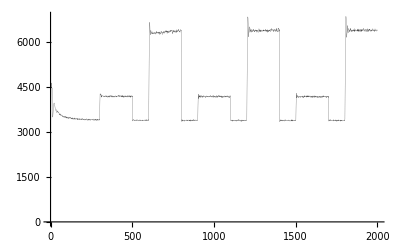

-Graphics-

```mathematica
goptimallm =  ListPlot[Take[optimallm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2031.,3828.05,5271.01,6273.03,6941.86,7148.49,7238.74,7073.9,6974.66,6933.9,6825.52,6753.35,6561.42,6223.33,5873.9,5591.42,5146.65,4859.93,4604.46,4414.93,4397.98,4394.77,4388.68,4323.82,4396.01,4351.74,4378.88,4313.39,4332.6,4365.95,4399.96,4428.77,4435.93,4491.27,4483.51,4523.79,4450.85,4465.16,4429.15,4448.39,4455.89,4365.54,4300.41,4324.84,4345.42,4313.26,4242.05,4225.14,4191.51,4133.46,4163.39,4113.49,4087.64,4010.59,4030.37,3967.61,3897.7,3921.18,3877.77,3859.14,3838.07,3855.22,3853.2,3778.38,3781.57,3765.23,3773.3,3746.63,3761.47,3747.87,3719.97,3661.79,3657.22,3657.82,3643.95,3659.53,3625.73,3654.37,3663.52,3646.47,3599.35,3575.1,3602.38,3642.14,3623.98,3578.48,3578.57,3586.48,3590.75,3574.6,3577.91,3570.87,3559.74,3541.65,3583.08,3560.43,3565.34,3603.29,3589.,3557.4,3530.42,3517.08,3562.09,3530.59,3547.4,3547.44,3529.97,3505.57,3513.33,3521.07,3551.12,3483.91,3535.24,3532.73,3544.82,3527.69,3529.81,3512.9,3502.06,3527.08,3497.77,3507.76,3525.17,3506.73,3520.5,3538.5,3512.17,3502.34,3538.4,3527.01,3495.77,3538.83,3509.67,3521.57,3483.52,3484.47,3487.98,3491.69,3475.88,3506.83,3472.42,3478.7,3519.65,3494.42,3489.6,3512.23,3491.81,3472.64,3492.62,3502.83,3493.84,3474.42,3473.73,3454.24,3497.49,3489.65,3491.34,3498.47,3461.25,3473.07,3496.85,3473.28,3482.03,3473.12,3482.2,3498.82,3462.62,3485.68,3481.08,3494.08,3503.26,3449.61,3519.02,3490.69,3480.47,3491.07,3483.52,3467.19,3478.85,3499.88,3477.23,3459.27,3489.42,3487.75,3502.9,3501.58,3467.49,3496.66,3469.89,3443.59,3484.66,3482.57,3446.99,3458.44,3462.42,3464.87,3465.44,3491.58,3469.,3466.41,3487.48,3429.17,3485.39,3471.93,3509.1,3451.75,3470.34,3507.86,3486.56,3466.86,3440.58,3473.22,3465.35,3464.81,3483.7,3478.11,3433.69,3469.8,3493.53,3421.96,3482.86,3494.87,3488.91,3452.37,3460.09,3467.21,3479.6,3466.79,3469.02,3463.17,3459.33,3458.14,3476.34,3489.98,3481.63,3448.57,3491.57,3497.81,3486.74,3479.9,3465.59,3456.06,3472.32,3495.32,3476.34,3460.44,3460.57,3463.7,3478.65,3458.71,3463.03,4303.54,4720.81,4807.61,4734.98,4639.84,4580.64,4581.73,4535.72,4487.94,4444.88,4424.54,4385.35,4302.08,4286.41,4286.12,4221.91,4192.82,4173.82,4110.95,4067.29,4075.18,4071.8,4044.59,4041.85,4006.68,3950.37,3952.11,3937.96,3920.35,3888.55,3893.07,3886.48,3902.34,3872.5,3847.48,3878.76,3888.49,3888.77,3822.66,3859.77,3845.75,3800.29,3799.25,3794.75,3762.57,3832.16,3811.74,3766.61,3727.47,3774.58,3758.56,3725.65,3752.45,3714.82,3706.62,3746.18,3765.28,3733.09,3711.08,3710.21,3691.1,3696.75,3717.4,3699.53,3692.46,3685.5,3703.37,3728.41,3702.77,3698.55,3698.02,3708.49,3701.24,3672.74,3688.52,3690.06,3681.29,3652.29,3694.58,3673.8,3686.18,3675.29,3677.41,3655.27,3639.43,3705.95,3708.93,3695.86,3674.77,3668.05,3662.26,3639.73,3691.99,3687.79,3633.98,3666.1,3647.19,3661.25,3669.62,3667.97,3677.63,3666.72,3664.76,3648.08,3677.7,3640.43,3645.6,3611.14,3679.81,3642.35,3655.26,3679.92,3686.57,3635.81,3612.4,3663.08,3657.84,3648.62,3663.01,3632.63,3635.26,3665.86,3643.15,3628.88,3663.06,3647.81,3644.35,3653.91,3600.91,3611.66,3647.82,3624.22,3630.94,3648.65,3630.35,3649.31,3652.18,3638.56,3644.98,3639.08,3649.72,3599.24,3645.13,3627.99,3599.73,3622.07,3607.5,3659.91,3651.34,3600.83,3662.38,3641.33,3619.23,3601.64,3642.55,3611.16,3627.44,3606.68,3620.16,3625.03,3635.5,3620.96,3651.17,3632.41,3634.7,3615.13,3636.75,3609.94,3607.52,3592.54,3613.42,3579.85,3604.21,3625.72,3606.23,3609.53,3607.45,3601.4,3590.55,3636.03,3628.86,3634.01,3619.86,3615.74,3640.19,3606.94,3613.,3602.38,3614.28,3621.96,3651.68,3617.42,3603.77,3593.99,3616.85,3622.63,3633.23,3601.19,3597.62,3605.75,3601.94,3619.98,3674.55,3641.19,3634.55,3606.8,3601.4,3614.94,3614.8,3634.95,3605.62,3588.08,3621.84,3618.41,3631.02,3623.83,3606.43,3629.11,3651.33,3620.73,3624.5,3616.76,3614.78,3601.3,3580.32,3594.21,3597.09,3626.64,3585.95,3651.34,3616.75,3607.59,3623.81,3593.46,3568.04,3597.,3575.65,3606.71,3574.61,3605.03,3625.04,3603.05,3597.9,3623.98,3620.52,3591.65,3608.87,3640.35,3601.65,3610.67,4588.62,5498.41,5969.69,5994.7,5745.66,5603.48,5568.35,5486.91,5417.62,5369.57,5247.22,5197.6,5051.71,5009.65,4953.46,4868.03,4812.74,4822.38,4739.02,4644.69,4596.56,4573.18,4573.19,4547.46,4486.04,4445.62,4395.9,4413.86,4328.61,4319.82,4325.78,4329.13,4265.71,4252.29,4257.37,4283.41,4273.39,4214.78,4220.47,4238.67,4202.52,4189.78,4163.94,4166.31,4189.78,4169.1,4088.95,4073.13,4082.17,4076.75,4102.64,4076.9,4041.07,4037.18,4041.9,4084.42,4008.45,3998.6,4003.22,4025.04,4000.74,4025.51,3977.69,3961.87,4004.1,3983.61,3958.24,3951.48,3996.91,3993.94,3970.91,3997.24,3977.49,3970.19,3937.93,3945.46,3938.53,3957.97,3922.56,3919.76,3891.,3942.69,3928.36,3963.91,3908.2,3870.61,3852.05,3875.49,3892.77,3856.3,3885.5,3841.,3874.94,3857.1,3858.29,3863.17,3859.02,3860.17,3858.03,3913.6,3869.97,3844.72,3854.5,3862.46,3852.18,3855.79,3875.03,3846.12,3840.46,3875.25,3837.84,3830.7,3844.32,3832.97,3829.03,3865.44,3867.44,3829.87,3778.85,3811.04,3824.71,3840.6,3848.75,3841.98,3818.71,3795.88,3834.74,3803.85,3773.33,3830.2,3862.52,3843.99,3770.55,3825.39,3789.05,3827.48,3795.05,3803.32,3828.85,3825.29,3825.5,3807.56,3809.03,3791.84,3814.58,3796.74,3793.86,3793.1,3780.03,3765.43,3792.95,3775.29,3773.5,3791.99,3780.69,3806.86,3768.73,3824.41,3802.21,3804.32,3812.77,3816.11,3818.24,3781.95,3801.14,3798.24,3800.58,3811.06,3779.76,3811.66,3798.8,3779.55,3799.05,3798.31,3787.59,3830.79,3771.28,3738.06,3783.22,3776.91,3782.71,3781.31,3772.79,3781.51,3777.56,3792.55,3778.74,3736.51,3789.95,3792.37,3778.06,3730.26,3747.18,3781.2,3746.89,3792.35,3756.98,3748.17,3774.41,3765.33,3774.18,3743.91,3778.79,3756.05,3761.04,3783.45,3775.27,3767.3,3792.92,3778.77,3752.03,3756.15,3750.37,3767.17,3798.98,3742.99,3751.87,3808.97,3764.28,3714.42,3751.19,3779.85,3761.81,3752.82,3740.67,3755.06,3782.37,3766.63,3778.48,3761.78,3750.37,3753.42,3759.03,3760.68,3784.77,3782.83,3780.84,3780.59,3789.96,3781.27,3722.51,3714.06,3750.93,3724.77,3724.75,3782.74,3727.59,3734.69,3738.05,3755.5,4685.21,5604.27,5919.68,5972.14,5708.15,5544.06,5408.93,5492.8,5506.96,5306.85,5263.47,5230.54,5163.01,5073.77,4988.82,4887.43,4825.39,4759.33,4755.81,4708.52,4675.9,4607.99,4584.59,4578.82,4540.85,4458.2,4452.36,4475.08,4424.93,4402.94,4302.55,4376.79,4365.75,4286.54,4297.02,4306.06,4304.01,4276.96,4226.9,4200.49,4254.54,4213.94,4190.26,4216.99,4211.5,4172.55,4207.13,4171.21,4175.44,4199.01,4157.67,4136.7,4124.94,4099.62,4141.44,4118.18,4116.95,4140.55,4087.44,4091.85,4056.31,4083.85,4109.38,4088.41,4071.58,4108.4,4059.04,4067.51,4032.16,4027.83,4026.13,4075.1,4058.6,4014.03,4011.89,3993.91,4031.72,3994.55,4015.18,4037.97,4010.82,3996.73,3976.1,3980.16,4005.69,3999.24,4006.27,3986.37,4002.12,3984.22,3993.21,3991.4,4017.97,3983.97,3997.27,3943.56,3935.73,3957.3,3954.43,3951.42,3964.88,3970.36,3984.2,3960.37,3978.38,3941.43,3945.49,3984.49,3955.98,3967.09,3947.14,3954.93,3980.2,3948.28,3914.02,3960.07,3933.96,3908.51,3964.26,3963.72,3952.08,3935.83,3961.47,3941.56,3946.71,3952.02,3950.25,3949.47,3938.54,3945.3,3922.16,3912.84,3961.12,3930.39,3973.26,3975.18,3926.07,3904.97,3916.58,3950.8,3933.55,3938.44,3898.73,3853.02,3907.24,3921.75,3903.72,3854.24,3898.29,3901.78,3880.55,3927.45,3909.25,3895.66,3929.15,3875.5,3888.6,3893.48,3927.34,3897.28,3869.04,3905.35,3903.85,3893.09,3880.94,3895.96,3934.45,3911.77,3921.2,3912.26,3933.03,3887.32,3901.17,3891.58,3885.35,3898.6,3881.52,3881.71,3855.5,3866.59,3894.81,3851.12,3856.37,3883.34,3887.07,3884.27,3895.76,3823.11,3875.84,3861.59,3867.42,3883.36,3859.3,3862.49,3914.84,3879.14,3877.71,3846.25,3853.43,3864.14,3859.78,3867.88,3875.98,3871.38,3899.73,3896.15,3843.64,3848.12,3855.58,3900.29,3850.41,3835.04,3879.29,3840.21,3854.94,3880.3,3897.81,3870.24,3881.18,3849.95,3852.46,3875.52,3865.97,3918.22,3882.46,3888.14,3867.18,3860.75,3863.42,3874.09,3905.59,3885.78,3853.29,3803.38,3836.71,3881.66,3834.32,3834.08,3858.88,3857.89,3850.17,3867.05,3825.31,3830.18,3847.72,3900.74,3860.87,3838.56,3856.49,3863.54,4753.06,5578.04,5841.03,5932.62,5629.92,5453.28,5376.85,5386.89,5336.97,5333.9,5215.91,5173.22,5174.33,5102.42,5027.68,5011.02,4894.09,4870.3,4891.5,4836.,4842.82,4745.52,4786.98,4712.1,4688.01,4661.88,4623.76,4538.06,4562.81,4561.41,4607.43,4517.07,4500.92,4483.57,4448.9,4413.01,4447.81,4388.36,4371.21,4389.91,4397.17,4361.79,4341.63,4313.62,4282.12,4310.01,4279.77,4275.53,4260.73,4273.78,4288.64,4249.86,4255.31,4219.11,4210.24,4181.11,4213.71,4174.63,4224.05,4180.35,4182.22,4148.02,4199.27,4196.81,4168.39,4140.87,4189.,4158.86,4153.96,4149.79,4191.16,4149.,4131.56,4151.98,4119.59,4106.21,4115.13,4091.59,4072.09,4137.35,4135.84,4135.23,4123.65,4090.5,4119.89,4144.17,4126.78,4071.01,4113.64,4105.81,4064.9,4108.39,4082.67,4081.28,4084.08,4106.27,4109.62,4103.87,4091.61,4071.23,4094.6,4087.29,4108.08,4092.97,4102.28,4098.61,4050.14,4076.23,4100.57,4083.82,4047.72,4073.2,4046.92,4086.53,4077.95,4052.3,4064.02,4047.99,4049.53,4053.04,4090.16,4096.52,4034.02,4085.74,4079.38,4067.84,4045.54,4054.69,4091.55,4072.67,4043.31,4024.52,4046.97,4042.32,4081.01,4074.64,4008.81,4038.33,3999.96,4016.53,4044.83,4047.38,4031.25,4014.36,4050.17,4036.04,3979.48,4037.33,4046.18,4000.83,3999.81,4004.93,4027.92,4064.61,4020.66,3980.,3978.75,4032.35,3995.2,4015.7,4044.06,3975.82,3991.55,4029.2,4018.81,4007.31,4041.6,3967.16,4007.94,4036.94,4028.97,3989.25,4019.56,3985.32,4001.78,3983.27,4009.3,4009.91,4023.51,4030.68,4000.69,4011.51,4016.5,3981.16,3964.58,3982.4,4021.64,3980.97,3986.16,4019.3,3997.45,3980.13,4009.09,3980.97,4009.29,3969.09,3977.78,3942.54,3962.19,3969.37,3971.98,3982.09,3970.2,3995.68,3939.23,4000.61,3992.01,3943.77,4003.5,3985.54,3960.38,4003.59,4003.39,4014.49,4002.44,3985.67,3959.36,3977.8,4001.28,4043.91,3973.26,3968.21,3960.47,3956.47,3964.1,3959.68,3979.65,3949.19,3976.88,3963.77,3992.2,3973.41,3947.96,3962.46,3947.06,4006.04,3974.92,3974.35,3969.31,3967.47,3929.58,3961.96,3980.99,3955.01,3946.62,4007.59,3998.17,3961.72,3944.16,3990.38,4784.41,5549.94,5785.23,5777.66,5553.48,5337.2,5282.23,5284.57,5227.43,5174.48,5144.11,5108.74,5006.22,4956.45,4942.06,4914.1,4873.33,4847.01,4837.06,4783.66,4789.11,4753.91,4713.28,4716.18,4721.5,4624.12,4681.55,4663.63,4587.7,4581.75,4593.79,4572.43,4581.61,4553.59,4529.31,4527.4,4501.59,4504.76,4500.57,4458.69,4449.59,4432.63,4426.33,4427.33,4450.97,4379.54,4378.29,4378.33,4365.58,4338.6,4379.16,4367.91,4337.4,4313.79,4306.48,4283.03,4323.88,4279.04,4280.13,4273.8,4243.65,4282.74,4219.24,4258.46,4233.63,4244.97,4214.32,4186.33,4226.94,4232.39,4201.37,4208.78,4185.93,4175.79,4195.82,4171.16,4169.04,4185.36,4189.78,4190.76,4228.75,4217.98,4175.29,4203.88,4244.21,4157.7,4167.04,4162.51,4157.65,4130.72,4135.82,4149.74,4156.72,4178.58,4141.88,4165.71,4208.86,4119.07,4142.12,4188.06,4101.56,4113.3,4153.09,4120.4,4118.99,4147.15,4133.02,4135.24,4137.42,4135.99,4174.27,4127.47,4115.32,4115.45,4107.97,4098.54,4128.09,4136.44,4093.66,4099.86,4128.61,4096.15,4098.95,4087.98,4092.78,4064.8,4102.78,4071.31,4143.67,4116.69,4113.52,4073.84,4119.58,4094.68,4130.47,4125.86,4121.87,4076.75,4095.21,4115.79,4145.3,4107.67,4116.99,4032.36,4078.7,4074.23,4067.98,4083.41,4063.74,4097.82,4064.68,4106.19,4110.3,4028.24,4056.84,4083.96,4122.86,4057.17,4041.23,4044.06,4068.51,4051.12,4046.82,4102.74,4112.45,4048.79,4063.92,4067.26,4066.28,4103.39,4062.84,4047.13,4060.3,4066.45,4095.33,4034.75,4073.04,4074.61,4114.85,4034.23,4077.58,4091.96,4116.36,4038.82,4058.53,4051.44,4027.41,4038.37,4041.79,4071.72,4049.05,4050.41,4033.34,4070.64,4076.43,4054.95,4049.89,4028.43,4018.78,4070.55,4067.54,4054.03,4033.28,4021.44,4041.48,4073.78,4060.64,4022.35,4063.1,4097.71,4089.4,4000.87,4059.71,4092.64,4080.28,4086.22,4070.77,4071.72,4061.41,4026.98,4033.23,4021.24,4050.82,4060.45,4022.2,4017.73,4003.55,4080.55,4016.53,4055.47,4041.58,4017.97,4013.98,4039.6,4032.92,4096.47,4072.08,4003.11,4040.18,4099.96,4018.2,4012.42,3990.9,4001.51,4001.27,3991.73,4031.8,4048.82,4032.05,4030.96,4807.58,5497.56,5686.52,5697.74,5380.36,5227.04,5181.19,5163.29,5140.11,5063.02,5014.14,5002.,4946.47,4951.5,4923.99,4870.65,4870.97,4810.12,4841.17,4822.22,4756.38,4779.91,4759.09,4750.55,4722.28,4748.38,4681.87,4699.44,4662.28,4663.53,4680.36,4605.26,4620.17,4588.97,4604.17,4594.45,4568.59,4589.26,4582.14,4571.03,4498.19,4548.07,4517.01,4498.84,4487.72,4488.7,4436.85,4453.06,4461.98,4468.91,4432.93,4379.93,4369.19,4403.55,4368.82,4381.44,4362.19,4341.54,4352.78,4329.9,4328.74,4348.76,4355.93,4356.64,4356.1,4330.21,4338.13,4309.7,4329.06,4342.2,4316.03,4277.17,4319.19,4336.84,4285.04,4296.84,4310.34,4309.45,4328.91,4312.33,4286.38,4284.,4252.67,4263.11,4279.66,4293.03,4261.4,4282.46,4288.91,4244.77,4258.97,4237.68,4220.23,4262.9,4249.02,4237.88,4250.13,4242.03,4254.39,4260.55,4302.19,4257.86,4211.66,4230.03,4234.6,4231.63,4236.9,4271.64,4237.93,4230.81,4220.89,4260.08,4253.73,4223.01,4259.44,4221.33,4264.82,4189.95,4239.65,4243.08,4198.16,4224.39,4222.73,4189.5,4219.09,4233.01,4220.69,4213.91,4203.2,4218.7,4204.25,4200.79,4221.97,4206.04,4155.33,4185.22,4188.93,4213.81,4167.12,4193.58,4139.32,4212.88,4203.,4173.56,4232.84,4199.41,4187.49,4170.91,4195.13,4180.82,4177.5,4170.56,4176.86,4182.78,4202.45,4174.7,4181.74,4188.46,4188.08,4186.01,4186.33,4195.28,4143.54,4142.45,4153.49,4163.34,4111.83,4146.18,4145.48,4199.78,4167.42,4173.52,4102.55,4153.56,4197.77,4143.55,4158.5,4155.58,4154.54,4172.95,4155.07,4098.73,4159.73,4171.91,4182.61,4162.58,4166.02,4167.29,4146.16,4167.11,4179.9,4130.54,4145.21,4174.11,4187.55,4157.89,4169.15,4135.3,4140.53,4156.39,4119.53,4170.8,4123.22,4120.64,4115.77,4148.91,4153.91,4165.38,4110.52,4114.11,4136.42,4135.24,4138.75,4089.9,4133.21,4137.,4166.46,4115.72,4135.93,4117.67,4074.3,4087.72,4120.76,4114.83,4102.86,4140.08,4134.61,4115.73,4126.79,4085.45,4122.84,4118.44,4095.27,4062.05,4111.15,4104.08,4135.74,4120.11,4125.86,4097.43,4133.38,4128.05,4125.31,4122.67,4093.,4143.66,4134.61,4118.99,4081.91,4070.74,4833.44,5428.09,5638.85,5550.94,5326.84,5158.75,5061.78,5051.84,4996.63,4966.73,4928.92,4925.73,4898.42,4868.69,4817.22,4797.08,4773.87,4765.34,4824.96,4786.95,4706.1,4722.13,4712.8,4707.54,4695.11,4685.9,4691.34,4647.92,4637.4,4678.32,4643.87,4618.73,4648.95,4633.5,4625.84,4580.24,4591.76,4586.8,4586.64,4599.58,4572.38,4543.23,4528.78,4549.09,4549.44,4516.01,4514.49,4494.15,4479.82,4422.57,4444.21,4418.22,4438.68,4433.95,4461.62,4486.36,4441.42,4415.27,4440.15,4420.95,4378.14,4371.33,4371.54,4407.61,4327.44,4395.75,4355.02,4368.81,4386.8,4365.6,4357.29,4364.92,4383.49,4305.28,4298.71,4294.37,4318.85,4328.86,4332.18,4325.58,4309.68,4304.92,4321.59,4360.98,4324.03,4315.14,4328.89,4312.45,4287.59,4317.38,4260.71,4280.1,4292.44,4311.98,4281.4,4300.02,4290.79,4249.53,4264.12,4294.13,4285.94,4294.67,4244.46,4222.25,4275.05,4245.82,4251.66,4273.33,4247.99,4259.61,4285.85,4273.94,4270.83,4279.33,4295.68,4303.13,4235.51,4279.09,4314.5,4228.61,4249.1,4252.66,4258.22,4259.37,4286.75,4262.99,4287.41,4246.5,4276.3,4266.12,4254.22,4258.82,4231.5,4292.67,4268.56,4263.15,4212.5,4235.84,4199.93,4244.26,4237.63,4250.76,4192.13,4247.59,4244.33,4248.56,4257.99,4248.93,4187.59,4233.7,4226.89,4219.4,4225.43,4267.46,4255.25,4224.73,4230.54,4271.99,4231.47,4225.2,4206.81,4216.35,4230.85,4240.26,4220.89,4189.59,4205.73,4219.35,4250.62,4197.92,4161.85,4167.37,4240.13,4215.12,4191.87,4177.1,4228.48,4211.05,4214.45,4158.01,4209.74,4255.22,4209.29,4242.57,4173.24,4171.32,4198.54,4195.81,4178.29,4153.33,4163.7,4217.26,4172.96,4159.61,4166.22,4197.04,4146.72,4158.95,4217.72,4186.9,4199.56,4200.31,4155.85,4172.65,4176.6,4206.82,4191.74,4172.93,4162.71,4183.52,4136.2,4170.82,4190.01,4182.33,4173.19,4177.94,4188.92,4180.69,4155.58,4201.08,4146.53,4162.73,4200.94,4195.77,4149.28,4193.93,4201.64,4150.99,4206.69,4187.32,4177.93,4194.34,4182.89,4201.44,4167.74,4177.75,4138.63,4184.91,4186.86,4150.49,4129.32,4185.39,4200.31,4143.76,4150.43,4189.27,4192.78,4176.9,4205.31},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gcomplexxPm = ListPlot[Take[complexxPm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Red, Thickness[0.001]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2028.32, 3190.77, 3581.29, 3496.75, 3413.81, 3448.83, 3395.51, 3394.9, 3411.86, 3386.67, 3408.41, 3410.76, 3387.38, 3410.5, 3397.15, 3422.33, « 19 », 3423.27, 3406.52, 3390.43, 3391.18, 3380.05, 3392.98, 3395.68, 3414.26, 3394.49, 3396.72, 3404.7, 3436.82, 3391.02, 3408.65, 3389.99, « 1950 »}, « 2 », PlotStyle → {« 1 »}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2028.32,3190.77,3581.29,3496.75,3413.81,3448.83,3395.51,3394.9,3411.86,3386.67,3408.41,3410.76,3387.38,3410.5,3397.15,3422.33,3401.55,3415.7,3406.32,3400.52,3390.05,3382.42,3392.2,3383.85,3406.65,3381.86,3390.87,3406.54,3405.77,3423.82,3380.35,3424.52,3405.83,3401.91,3401.88,3423.27,3406.52,3390.43,3391.18,3380.05,3392.98,3395.68,3414.26,3394.49,3396.72,3404.7,3436.82,3391.02,3408.65,3389.99,3395.69,3429.65,3414.47,3421.59,3421.49,3432.71,3412.48,3400.36,3406.,3404.16,3401.24,3415.45,3404.3,3411.94,3418.9,3399.55,3404.53,3392.76,3403.82,3392.69,3400.45,3393.07,3401.32,3388.31,3403.52,3399.41,3400.31,3404.75,3405.81,3410.62,3403.32,3424.25,3412.38,3395.53,3382.69,3392.51,3395.06,3429.7,3424.13,3411.44,3408.39,3422.37,3399.17,3398.95,3406.98,3396.83,3432.38,3430.24,3404.72,3400.32,3409.76,3408.98,3396.44,3412.74,3393.76,3399.73,3382.08,3394.37,3398.5,3416.79,3406.89,3382.57,3385.06,3395.26,3414.58,3389.44,3394.9,3399.35,3407.18,3424.72,3420.9,3415.42,3394.86,3415.29,3406.7,3360.95,3380.54,3415.,3420.19,3415.65,3411.23,3412.85,3418.6,3409.68,3405.45,3413.67,3406.3,3409.51,3415.75,3386.89,3392.58,3387.02,3395.28,3382.96,3409.21,3420.39,3388.24,3404.63,3413.55,3417.28,3397.16,3392.18,3426.43,3396.52,3405.53,3411.26,3418.1,3418.91,3407.93,3399.64,3392.01,3415.12,3398.82,3393.55,3385.77,3399.65,3411.88,3418.95,3394.36,3403.62,3430.83,3411.23,3405.82,3404.96,3402.89,3382.19,3403.45,3430.81,3422.04,3370.18,3404.52,3401.42,3424.23,3404.28,3393.18,3400.22,3396.31,3395.78,3398.33,3387.72,3393.21,3366.46,3401.16,3392.38,3400.55,3389.69,3405.03,3400.11,3422.05,3418.58,3409.48,3404.62,3397.9,3423.54,3415.44,3388.67,3397.27,3408.76,3406.56,3414.31,3380.76,3387.08,3433.1,3416.65,3420.66,3381.83,3408.51,3406.46,3391.85,3432.19,3417.54,3410.35,3385.06,3383.33,3389.28,3392.71,3393.05,3409.37,3394.73,3401.37,3395.17,3387.55,3427.48,3416.42,3407.63,3419.06,3413.65,3368.2,3407.14,3373.16,3412.2,3375.11,3405.43,3404.51,3384.23,3384.98,3377.78,3389.34,3402.16,3401.81,3416.6,4183.97,4740.77,4976.11,5009.78,4860.4,4845.75,4864.18,4851.95,4864.72,4790.8,4873.5,4840.35,4879.76,4872.5,4909.23,4880.23,4846.6,4864.,4879.58,4855.9,4894.45,4836.89,4857.76,4884.79,4836.72,4838.96,4789.9,4853.31,4846.19,4905.48,4916.61,4858.18,4858.83,4876.18,4872.68,4853.58,4839.19,4834.07,4871.01,4889.87,4900.95,4868.63,4872.43,4820.06,4829.13,4842.72,4829.4,4847.64,4918.93,4934.14,4857.27,4875.05,4816.07,4832.64,4826.36,4899.47,4853.16,4795.29,4801.18,4773.31,4843.86,4898.12,4869.63,4822.92,4790.55,4862.74,4861.09,4865.32,4833.49,4832.31,4824.72,4819.39,4842.13,4850.82,4883.49,4851.98,4817.43,4839.14,4905.3,4861.14,4812.71,4832.05,4841.07,4819.08,4887.42,4862.69,4851.36,4848.37,4842.46,4902.81,4822.47,4897.25,4782.01,4782.53,4835.48,4838.54,4832.69,4850.76,4846.36,4788.52,4839.87,4822.46,4823.12,4797.47,4800.64,4842.17,4833.97,4843.89,4853.89,4854.12,4865.48,4903.32,4847.46,4855.32,4861.72,4823.06,4818.,4858.18,4859.13,4805.06,4841.01,4814.89,4821.93,4836.1,4853.44,4867.72,4831.99,4864.77,4875.64,4802.68,4820.61,4800.6,4852.68,4910.34,4909.47,4855.82,4895.53,4911.61,4798.82,4866.13,4865.05,4888.79,4844.89,4837.68,4854.83,4808.73,4840.15,4818.,4898.18,4826.21,4832.36,4814.13,4839.64,4884.36,4843.41,4808.52,4824.49,4878.59,4858.09,4849.18,4882.19,4875.15,4861.42,4892.04,4839.98,4802.19,4874.05,4816.15,4809.59,4856.84,4859.55,4916.28,4878.03,4889.64,4829.38,4819.62,4838.78,4872.65,4885.8,4856.24,4855.5,4872.37,4790.14,4837.98,4891.5,4861.06,4872.67,4871.08,4813.31,4862.,4840.39,4844.21,4841.83,4907.34,4902.66,4923.72,4822.72,4878.99,4849.38,4891.55,4858.09,4823.38,4945.24,4847.16,4862.03,4852.4,4882.14,4863.96,4857.43,4820.58,4852.54,4869.32,4854.39,4908.,4856.69,4871.98,4867.57,4822.51,4875.27,4833.97,4892.43,4901.11,4878.96,4850.93,4858.41,4853.01,4836.18,4833.41,4836.74,4886.6,4863.37,4856.69,4845.56,4908.9,4841.12,4827.89,4825.81,4825.01,4872.95,4824.57,4787.75,4793.33,4876.8,4863.15,4856.73,4764.91,4903.17,4883.49,4846.88,4809.33,4817.94,4876.67,4878.14,4853.6,4857.53,4863.6,4847.85,4819.79,4821.94,4824.66,4833.25,4778.78,4844.41,4820.49,4857.16,4780.51,4774.44,4799.96,4821.98,4862.57,4902.28,4863.6,4884.63,4886.3,4872.7,4787.11,4792.34,4845.7,4832.28,4873.64,4850.72,4790.62,4816.52,4827.94,4856.9,4866.01,4864.03,4847.34,4847.49,4803.01,4816.4,4829.83,4789.44,4833.93,4826.26,4897.86,4815.84,4827.05,4868.73,4849.72,4860.97,4832.66,4836.33,4813.16,4835.25,4830.88,4802.98,4872.62,4895.81,4824.03,4852.65,4835.01,4873.08,4826.41,4835.8,4862.58,4874.62,4878.18,4848.73,4838.62,4832.78,4827.89,4846.53,4865.02,4841.59,4856.53,4843.81,4816.,4826.33,4862.09,4821.97,4845.84,4796.45,4814.86,4843.53,4839.03,4844.38,4882.28,4823.86,4846.59,4854.6,4785.7,4803.41,4864.55,4794.09,4784.39,4811.84,4853.02,4866.32,4851.66,4817.69,4836.76,4835.18,4795.81,4776.32,4807.75,4837.55,4860.32,4867.49,4850.5,4869.33,4788.29,4792.34,4783.41,4844.46,4833.65,4811.97,4812.69,4797.27,4835.15,4859.37,4816.44,4840.78,4809.08,4768.16,4790.37,4823.12,4813.48,4861.31,4797.26,4797.07,4805.48,4834.86,4800.73,4848.7,4836.14,4838.23,4822.69,4801.07,4793.46,4830.18,4837.15,4859.64,4861.69,4822.66,4838.32,4792.95,4845.33,4855.56,4882.,4820.21,4824.7,4798.92,4789.99,4811.04,4829.1,4834.97,4785.33,4815.5,4845.19,4797.71,4821.34,4812.49,4847.86,4879.89,4833.71,4850.91,4817.24,4818.39,4851.51,4816.1,4784.71,4843.01,4871.6,4869.52,4811.54,4834.1,4813.55,4818.37,4836.12,4845.33,4876.2,4880.02,4828.06,4848.71,4834.72,4797.76,4815.96,4836.77,4800.8,4794.61,4807.16,4806.72,4866.56,4880.02,4788.19,4834.84,4832.6,4847.69,4837.51,4841.07,4852.72,4831.46,4835.12,4819.97,4806.33,4789.23,4863.05,4819.19,4789.91,4803.09,4796.46,4794.47,4871.01,4805.95,4844.74,4852.02,4886.91,4817.97,4878.89,4783.59,4809.78,4797.88,4806.22,4843.96,4915.91,4843.93,4840.56,4845.1,4878.83,4832.76,4862.21,4820.81,4829.28,4844.44,4819.88,4802.67,4787.94,4834.44,4833.98,4828.43,4834.04,4846.02,4798.8,4831.41,4843.08,4834.26,4855.53,4843.22,4861.52,4909.71,4891.19,4821.09,4855.78,4871.16,4907.72,4856.45,4833.07,4854.33,4878.8,4837.36,4853.98,4854.67,4826.72,4824.36,4877.73,4870.52,4863.16,4841.33,4817.54,4887.41,4907.51,4858.27,4867.12,4830.69,4805.6,4880.32,4850.66,4855.86,4815.04,4912.05,4869.55,4875.57,4836.86,4873.39,4827.83,4856.66,4880.4,4863.61,4844.92,4813.4,4827.64,4830.13,4827.22,4798.74,4786.4,4868.09,4862.6,4832.18,4818.68,4895.63,4877.11,4854.26,4832.71,4836.39,4859.07,4900.96,4892.54,4860.14,4884.52,4828.83,4789.98,4845.49,4838.5,4857.73,4835.92,4851.85,4869.3,4908.47,4831.99,4848.88,4861.38,4863.8,4879.78,4850.16,4840.87,4879.88,4887.21,4862.1,4847.5,4876.37,4882.79,4769.63,4857.3,4827.7,4877.69,4820.9,4849.31,4859.97,4826.15,4831.45,4786.94,4824.53,4801.23,4868.14,4869.48,4840.56,4849.17,4834.23,4868.96,4847.14,4803.26,4829.92,4844.31,4868.06,4883.21,4897.45,4869.44,4819.49,4807.43,4870.91,4881.6,4810.09,4887.8,4877.97,4860.97,4810.15,4897.8,4845.23,4820.25,4881.67,4864.57,4854.15,4852.1,4823.18,4851.75,4831.14,4863.58,4863.64,4884.33,4845.35,4834.86,4877.84,4885.2,4878.75,4847.37,4813.4,4812.53,4903.23,4858.33,4821.32,4853.12,4880.18,4877.36,4842.19,4843.11,4851.32,4863.98,4856.15,4861.95,4824.08,4816.66,4851.02,4884.92,4882.85,4852.12,4859.22,4855.8,4923.69,4895.26,4875.13,4900.74,4847.83,4885.8,4807.52,4855.48,4830.29,4812.77,4801.78,4896.98,4881.51,4840.2,4805.69,4872.47,4842.8,4767.44,4807.65,4824.78,4911.98,4857.92,4852.8,4847.03,4877.84,4826.69,4843.42,4847.49,4903.67,4896.45,4836.79,4849.53,4854.87,4865.03,4865.63,4865.76,4870.,4895.86,4834.41,4834.48,4841.73,4870.87,4834.11,4838.64,4860.92,4873.59,4798.88,4864.33,4837.35,4835.05,4844.78,4929.56,4855.91,4806.69,4790.12,4899.97,4823.75,4849.25,4843.49,4853.85,4801.68,4892.92,4862.72,4883.26,4906.45,4875.34,4863.91,4852.98,4912.7,4869.9,4854.3,4837.37,4849.98,4866.96,4876.9,4812.39,4837.47,4786.45,4832.71,4829.99,4815.13,4874.08,4848.66,4863.26,4797.85,4875.94,4899.68,4861.13,4853.69,4809.83,4890.66,4836.79,4829.17,4884.34,4865.11,4851.8,4812.35,4840.69,4875.2,4868.92,4843.,4842.29,4883.24,4838.41,4830.27,4848.54,4880.39,4895.56,4837.34,4791.18,4790.3,4827.23,4784.95,4833.75,4841.05,4831.41,4815.21,4846.35,4857.26,4831.95,4899.78,4868.77,4825.1,4845.47,4818.81,4817.77,4806.12,4817.72,4787.89,4870.87,4844.92,4883.49,4808.06,4831.31,4812.21,4834.23,4847.32,4891.03,4864.31,4787.01,4791.18,4823.81,4781.38,4856.2,4860.85,4796.07,4816.74,4854.36,4820.82,4811.52,4826.78,4868.7,4862.73,4847.73,4849.24,4834.24,4794.07,4818.69,4835.56,4832.76,4820.88,4830.98,4775.25,4790.,4821.3,4813.19,4827.17,4915.3,4840.02,4799.97,4800.74,4778.07,4826.72,4861.79,4866.6,4889.17,4788.86,4783.37,4765.68,4816.76,4799.41,4816.07,4789.81,4814.22,4878.27,4833.02,4821.61,4829.89,4823.5,4825.12,4832.68,4849.26,4831.2,4768.47,4791.25,4832.79,4831.32,4828.3,4847.85,4809.93,4841.78,4881.26,4846.9,4895.26,4864.39,4823.8,4823.67,4825.6,4856.73,4880.1,4815.09,4786.71,4791.76,4825.47,4806.6,4801.84,4874.18,4890.52,4853.13,4824.91,4821.44,4896.42,4823.11,4829.78,4800.41,4856.62,4847.07,4808.37,4835.14,4790.24,4793.84,4812.07,4849.33,4826.77,4835.51,4815.55,4775.55,4816.76,4829.35,4823.9,4813.07,4793.5,4840.86,4811.73,4851.31,4838.53,4830.78,4847.61,4883.55,4869.01,4808.2,4795.69,4761.11,4845.74,4838.62,4806.61,4809.76,4853.57,4787.42,4849.11,4808.84,4819.43,4873.43,4814.38,4846.51,4825.35,4802.09,4828.54,4825.92,4808.08,4874.38,4823.38,4822.38,4865.38,4830.87,4798.68,4811.8,4909.12,4884.67,4849.72,4824.78,4835.27,4831.36,4842.42,4827.01,4857.91,4817.08,4807.74,4819.47,4827.48,4842.64,4857.42,4865.21,4832.53,4883.34,4788.89,4826.91,4807.76,4881.82,4841.18,4835.88,4831.95,4857.36,4839.08,4826.75,4820.13,4914.01,4823.67,4863.92,4845.93,4860.27,4801.85,4774.91,4756.4,4802.13,4868.99,4820.21,4870.2,4896.22,4842.21,4761.71,4836.59,4816.89,4840.29,4818.73,4854.88,4807.76,4874.63,4832.28,4807.32,4817.35,4817.74,4801.28,4859.9,4862.82,4869.5,4840.22,4874.4,4816.56,4789.83,4816.9,4795.46,4833.73,4822.18,4893.61,4857.,4837.77,4857.03,4870.78,4832.33,4810.47,4788.18,4859.73,4931.28,4864.5,4823.02,4837.71,4803.53,4843.14,4817.39,4868.54,4867.54,4807.55,4891.88,4888.06,4859.88,4849.5,4865.65,4860.69,4829.97,4795.98,4800.88,4861.01,4835.35,4856.66,4873.64,4846.71,4843.91,4823.51,4816.34,4829.15,4831.26,4847.23,4852.24,4821.24,4848.4,4824.66,4891.72,4838.82,4843.62,4910.09,4834.13,4840.4,4842.19,4853.05,4868.42,4899.39,4852.5,4865.5,4813.16,4826.37,4831.88,4860.38,4864.62,4842.55,4840.43,4818.68,4886.81,4897.96,4885.32,4816.11,4881.36,4863.85,4890.07,4912.45,4863.99,4797.95,4850.52,4799.13,4796.88,4849.84,4853.23,4809.34,4847.08,4907.01,4836.16,4844.01,4806.2,4820.31,4819.74,4829.31,4849.53,4862.46,4896.49,4909.82,4947.34,4863.64,4868.99,4864.14,4859.72,4895.58,4875.45,4851.41,4859.83,4840.88,4838.71,4892.98,4808.12,4867.33,4907.95,4897.9,4878.88,4872.47,4829.43,4888.38,4865.35,4884.85,4852.8,4845.,4836.51,4898.91,4792.44,4857.86,4825.79,4841.49,4873.55,4868.55,4862.78,4842.37,4917.48,4834.44,4867.55,4878.86,4852.46,4889.72,4827.94,4825.56,4886.07,4873.84,4838.01,4875.39,4846.52,4834.17,4843.56,4838.71,4869.13,4935.02,4886.93,4866.95,4889.21,4786.38,4844.18,4823.33,4844.22,4848.77,4828.91,4936.34,4886.17,4843.93,4858.04,4894.03,4870.73,4894.89,4893.92,4839.66,4846.84,4851.56,4862.02,4862.43,4870.55,4845.44,4858.71,4841.48,4850.78,4878.94,4845.66,4806.57,4848.61,4846.73,4862.57,4883.,4806.63,4801.99,4821.09,4850.64,4802.8,4798.1,4844.87,4867.93,4881.77,4854.22,4839.7,4895.04,4891.26,4856.37,4829.02,4895.63,4861.62,4878.67,4854.92,4846.95,4838.25,4843.99,4855.02,4883.27,4866.68,4843.76,4845.39,4832.02,4845.84,4865.22,4840.8,4831.25,4873.64,4880.32,4859.03,4839.24,4801.22,4890.22,4899.25,4868.9,4843.3,4874.84,4899.16,4902.74,4909.24,4804.6,4867.22,4840.7,4900.64,4866.12,4862.52,4856.85,4850.11,4847.77,4846.13,4851.42,4864.13,4839.18,4856.57,4875.84,4848.66,4849.98,4821.49,4865.36,4822.54,4916.43,4875.98,4833.41,4821.4,4846.45,4862.41,4867.75,4889.05,4782.8,4841.67,4823.52,4837.61,4834.89,4863.89,4855.54,4792.37,4833.52,4830.44,4812.11,4814.93,4846.57,4873.03,4865.36,4847.72,4883.23,4849.99,4812.1,4791.57,4840.63,4853.34,4780.13,4808.53,4886.34,4908.25,4830.22,4845.19,4848.42,4847.94,4827.6,4796.28,4785.92,4839.13,4827.63,4901.41,4846.82,4791.28,4846.71,4854.09,4844.69,4853.17,4830.75,4890.16,4866.06,4838.27,4846.77,4807.99,4887.14,4879.67,4830.16,4777.45,4850.65,4828.89,4821.22,4868.8,4863.37,4832.,4850.29,4796.64,4821.4,4837.08,4874.85,4840.91,4809.67,4844.81,4844.22,4811.32,4856.17,4832.57,4836.73,4777.22,4827.11,4841.69,4842.69,4864.76,4870.96,4809.3,4873.79,4876.14,4867.79,4842.52,4814.82,4842.08,4817.15,4822.67,4833.87,4836.79,4852.39,4844.51,4894.6,4849.98,4823.07,4850.54,4828.87,4806.29,4821.82,4799.71,4815.35,4856.8,4779.31,4812.33,4833.7,4783.77,4803.19,4887.12,4849.78,4822.47,4855.32,4834.37,4807.41,4784.48,4817.38,4820.54,4861.29,4884.45,4826.67,4835.16,4831.97,4843.21,4807.69,4810.09,4800.97,4840.26,4883.81,4788.15,4768.1,4828.9,4823.87,4904.47,4832.97,4841.02,4823.04,4795.71,4840.31,4816.67,4843.33,4807.27,4801.78,4845.97,4837.81,4867.96,4802.61,4790.64,4829.64,4856.13,4841.43,4816.7,4827.15,4900.41,4819.45,4875.88,4817.11,4861.6,4770.95,4837.62,4831.36,4855.74,4800.,4835.08,4793.82,4812.43,4849.88,4833.59,4802.53,4817.59,4808.66,4828.87,4816.65,4841.09,4779.77,4856.3,4842.65,4872.28,4826.67,4810.61,4843.64,4858.32,4858.26,4881.1,4879.93,4826.19,4847.77,4872.88,4823.52,4839.03,4857.69,4812.19,4856.04,4867.36,4833.71,4845.16,4747.47,4808.4,4865.14,4814.27,4762.83,4815.2,4831.11,4853.44,4797.74,4852.43,4846.23,4792.39,4851.96,4802.13,4826.71,4794.54,4852.7,4825.96,4838.66,4804.46,4845.5,4838.03,4823.11,4841.29,4755.81,4828.87,4790.25,4783.66,4800.,4877.99,4861.63,4832.9,4819.32,4836.17,4839.,4862.56,4865.71,4899.21,4896.91,4848.08,4843.81,4820.15,4833.75,4852.41,4866.92,4849.58,4843.51,4799.12,4813.54,4834.97,4835.51,4823.25,4810.82,4815.36,4842.2,4742.46,4788.82,4821.6,4803.59,4794.21,4869.45,4854.37,4895.17,4914.81,4852.11,4884.58,4844.74,4857.73,4832.11,4855.63,4821.25,4826.88,4791.75,4807.77,4790.08,4898.06,4844.44,4811.89,4840.27,4846.43,4888.19,4871.08,4848.81,4824.46,4804.66,4808.59,4799.51,4861.45,4855.68,4881.56,4893.31,4832.86,4867.07,4897.61,4818.62,4873.84,4868.79,4878.76,4916.49,4855.8,4868.52,4908.36,4865.06,4855.18,4878.13,4805.71,4891.02,4860.48,4817.33,4834.74,4863.48,4852.2,4882.55,4858.38,4858.3,4855.31,4839.58,4894.73,4817.06,4870.31,4895.56,4884.46,4905.7,4874.85,4871.48,4810.26,4883.84,4848.75,4865.99,4856.42,4830.95,4844.99,4855.99,4832.17,4771.91,4879.23,4885.13,4851.2,4864.25,4878.43,4867.64,4746.85,4847.55,4786.76,4817.67,4854.34,4828.27,4864.35,4841.3,4834.69,4844.51,4876.7,4891.3,4844.1,4826.74,4825.97,4845.37,4837.49,4836.61,4846.02,4799.99,4855.15,4817.19,4875.37,4901.73,4876.06,4851.14,4817.06,4853.69,4913.45,4884.3,4852.55,4858.3,4863.83,4857.81,4827.91,4823.92,4829.44,4795.45,4882.56,4868.99,4842.12,4893.67,4911.53,4875.99,4939.82,4861.4,4858.02,4896.47,4781.13,4804.87,4840.68,4827.78,4834.22,4871.41,4818.8,4833.48,4811.86,4856.61,4899.28,4801.89,4882.67,4864.92,4846.52,4832.7,4891.34,4846.78,4793.52,4843.97,4880.35,4858.07,4872.66,4868.63,4860.83,4877.84,4797.47,4807.73,4875.12,4867.49,4886.33,4861.,4842.12,4831.58,4888.07,4886.67,4821.29,4822.3,4858.37,4841.69,4784.26,4830.63,4851.22,4879.35,4843.37,4774.03,4825.53,4878.9,4852.89,4877.52,4849.2,4861.01,4863.66,4898.46,4809.58,4836.38,4841.29,4893.,4856.94,4807.61,4831.56,4842.92,4844.85,4916.18,4868.75,4865.12,4812.76,4867.34,4801.12,4834.03,4863.11,4861.2,4841.55,4840.12,4862.27,4874.22,4806.35,4769.55,4793.85,4786.11,4858.72,4919.86,4915.79,4852.14,4884.19,4892.98,4893.92,4859.23,4848.11,4856.03,4851.12,4872.96,4903.71,4891.39,4846.44,4872.07,4857.74,4878.59,4881.63,4867.74,4849.7,4844.9,4877.12,4843.61,4885.33,4873.07,4892.83,4839.36,4848.22,4816.2,4837.96,4863.08,4883.82,4845.48,4870.35,4891.56},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gcomplexxRm= ListPlot[Take[complexxRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2029.39, 3812.1, 5169.72, 6110., 6536.01, 6036.27, 5144.9, 4663.51, 4356.35, 4186.42, 4155.68, 4025.35, 3961.97, 3954.09, 3879.99, 3909.03, 3879.57, 3831.54, « 15 », 3635.9, 3633.5, 3653.29, 3629.68, 3606.23, 3582.15, 3638.06, 3639.56, 3580.48, 3604.88, 3595.81, 3597.96, 3596.27, 3603.52, 3589.62, 3584.89, 3588.28, « 1950 »}, « 2 », PlotStyle → {« 1 »}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.39,3812.1,5169.72,6110.,6536.01,6036.27,5144.9,4663.51,4356.35,4186.42,4155.68,4025.35,3961.97,3954.09,3879.99,3909.03,3879.57,3831.54,3800.68,3774.91,3761.8,3737.35,3699.59,3665.18,3726.81,3707.53,3669.89,3643.56,3657.47,3611.71,3642.94,3635.31,3604.03,3635.9,3633.5,3653.29,3629.68,3606.23,3582.15,3638.06,3639.56,3580.48,3604.88,3595.81,3597.96,3596.27,3603.52,3589.62,3584.89,3588.28,3564.5,3608.36,3615.57,3608.45,3576.53,3600.96,3607.86,3573.24,3527.21,3557.17,3557.46,3569.06,3550.61,3504.53,3590.67,3583.17,3597.04,3525.01,3567.64,3588.13,3593.26,3571.97,3590.88,3543.74,3490.11,3589.71,3549.27,3551.71,3531.47,3526.27,3554.86,3599.44,3548.46,3635.99,3527.36,3534.33,3548.46,3567.2,3563.41,3607.92,3560.5,3537.21,3547.38,3585.16,3541.05,3536.27,3536.34,3570.36,3560.81,3528.14,3554.86,3542.75,3571.14,3534.89,3545.64,3530.16,3531.14,3565.16,3530.62,3527.48,3513.93,3555.5,3546.32,3541.71,3556.,3548.93,3496.57,3546.28,3540.47,3560.22,3566.43,3572.05,3569.05,3560.12,3540.5,3483.65,3507.75,3522.87,3549.26,3536.12,3550.26,3531.12,3507.04,3553.94,3539.81,3521.44,3477.78,3498.26,3514.22,3531.47,3493.5,3512.61,3511.29,3503.95,3483.78,3508.66,3477.1,3510.74,3535.2,3522.,3554.47,3519.29,3484.91,3477.86,3513.54,3520.73,3548.65,3492.88,3543.58,3514.04,3492.26,3509.21,3503.27,3519.25,3518.25,3491.34,3483.94,3505.51,3519.04,3488.43,3473.31,3479.33,3492.47,3532.1,3517.55,3452.61,3532.38,3523.23,3499.27,3550.17,3561.04,3502.07,3535.44,3524.77,3550.49,3520.85,3527.07,3534.25,3542.48,3556.87,3557.78,3520.95,3477.46,3529.86,3521.73,3553.27,3535.74,3507.01,3485.7,3527.34,3531.35,3492.68,3509.63,3456.57,3507.05,3517.7,3510.39,3529.41,3475.97,3495.56,3546.71,3522.05,3516.94,3509.52,3510.04,3487.97,3499.57,3491.59,3479.26,3492.98,3534.7,3499.11,3519.69,3505.34,3513.07,3534.37,3513.19,3552.54,3554.03,3562.13,3556.76,3529.76,3504.82,3484.04,3525.73,3531.1,3532.76,3514.4,3496.15,3482.95,3534.72,3530.05,3492.15,3528.22,3518.32,3514.84,3513.93,3485.38,3467.23,3515.68,3512.01,4210.58,4674.57,4836.62,4823.13,4774.28,4768.08,4718.62,4685.72,4637.4,4626.68,4637.04,4625.13,4637.95,4630.46,4591.46,4583.09,4592.34,4576.11,4579.91,4503.86,4474.93,4451.83,4493.29,4475.05,4434.65,4394.09,4355.03,4409.6,4385.22,4430.02,4359.12,4395.17,4343.26,4339.33,4299.56,4288.88,4351.08,4306.79,4321.01,4289.07,4235.81,4279.36,4261.48,4275.96,4252.85,4213.01,4211.41,4236.69,4195.53,4212.47,4133.58,4196.08,4147.9,4206.67,4136.15,4092.14,4113.1,4124.43,4097.37,4103.38,4172.18,4078.55,4098.55,4004.24,4076.36,4065.1,4052.47,4103.31,4030.42,4066.59,4002.49,4035.92,4032.76,4026.32,3968.65,4053.63,3964.88,3996.04,3969.22,3996.72,3985.71,3909.46,3920.1,3965.5,3946.47,3939.62,3883.98,3931.92,3910.09,3903.07,3903.96,3900.45,3894.78,3868.19,3844.83,3847.26,3865.06,3875.18,3869.71,3861.28,3849.58,3855.7,3855.35,3854.23,3848.56,3867.76,3853.11,3852.42,3867.69,3877.02,3885.29,3848.34,3795.16,3824.32,3863.28,3840.23,3813.41,3772.96,3806.64,3854.26,3782.27,3829.2,3862.76,3825.45,3800.65,3801.89,3731.44,3780.17,3751.76,3800.05,3714.99,3748.61,3766.07,3759.05,3757.32,3783.57,3726.64,3698.91,3697.32,3715.68,3732.39,3776.58,3780.56,3693.13,3704.5,3752.12,3721.81,3746.39,3692.06,3771.41,3689.35,3711.55,3733.53,3698.07,3640.79,3634.13,3660.25,3702.18,3691.49,3713.87,3682.86,3697.69,3677.68,3668.39,3650.86,3701.05,3704.01,3694.42,3704.48,3722.23,3702.83,3734.6,3723.08,3684.99,3657.26,3634.26,3673.71,3644.21,3652.62,3626.62,3674.22,3711.02,3687.52,3659.39,3633.56,3676.94,3642.27,3627.29,3648.24,3637.95,3617.66,3646.29,3638.83,3593.39,3649.46,3633.1,3660.41,3674.75,3657.93,3679.42,3652.76,3628.78,3590.4,3628.6,3619.77,3603.67,3609.04,3595.04,3590.27,3627.06,3612.75,3648.93,3629.21,3642.89,3625.89,3610.23,3577.04,3628.78,3620.57,3619.79,3596.31,3654.64,3622.94,3627.56,3646.56,3639.85,3644.65,3627.14,3630.64,3619.05,3585.09,3596.38,3590.4,3575.25,3572.44,3577.89,3595.01,3587.71,3587.48,3617.15,3619.2,3608.42,3629.11,3638.03,3615.19,3618.81,3616.32,3617.54,3655.13,3647.,4585.22,5459.01,5914.66,6085.77,6037.37,6005.66,5940.5,5912.37,5833.54,5845.64,5888.8,5816.85,5770.53,5694.71,5668.18,5564.82,5596.51,5539.3,5607.92,5463.22,5427.56,5451.98,5379.24,5354.94,5351.4,5370.79,5340.67,5269.31,5260.97,5203.65,5135.05,5120.57,5092.72,5134.19,5029.79,5060.09,5067.18,5045.71,4937.22,4960.72,4936.28,4895.27,4870.38,4875.82,4764.83,4777.94,4774.27,4672.1,4726.8,4729.08,4670.85,4636.26,4634.38,4629.99,4606.36,4636.52,4539.48,4585.7,4458.13,4552.19,4540.97,4484.39,4433.05,4440.37,4450.6,4459.21,4464.94,4379.91,4407.56,4362.46,4385.44,4303.63,4380.19,4315.78,4279.51,4284.53,4283.38,4238.89,4233.78,4216.45,4240.03,4178.35,4204.52,4154.59,4120.32,4112.65,4091.56,4139.8,4140.09,4080.66,4094.59,4092.51,4022.3,4024.27,4069.08,4080.05,4037.32,4023.74,4072.98,4037.79,4007.06,4014.83,4016.13,4040.84,4006.95,3994.91,3930.16,3998.9,3982.1,4005.12,3990.33,3971.58,3895.94,3958.61,3933.69,3927.15,3898.95,3891.82,3886.54,3922.64,3875.44,3877.17,3885.12,3877.22,3905.31,3903.25,3902.42,3865.08,3863.45,3854.08,3849.27,3867.26,3856.83,3856.7,3806.68,3824.6,3825.61,3792.01,3810.29,3827.82,3785.79,3828.86,3779.01,3741.73,3805.66,3802.32,3750.27,3740.98,3765.84,3791.8,3744.36,3761.16,3759.65,3770.82,3754.28,3723.32,3704.63,3713.84,3756.82,3714.76,3718.55,3723.2,3704.57,3684.62,3686.57,3699.33,3672.65,3688.87,3659.48,3689.13,3722.19,3712.11,3625.98,3701.71,3708.71,3697.58,3713.06,3691.92,3619.81,3684.51,3672.13,3691.3,3632.76,3661.39,3684.87,3710.89,3675.25,3702.64,3625.95,3656.31,3664.36,3661.14,3600.56,3630.62,3597.92,3637.78,3596.23,3602.17,3714.51,3680.91,3625.76,3637.79,3670.41,3649.41,3666.36,3631.74,3635.82,3661.32,3618.12,3630.18,3611.04,3597.82,3601.72,3632.35,3569.46,3588.65,3619.96,3603.52,3570.62,3636.47,3595.13,3572.02,3633.41,3651.37,3611.5,3555.58,3555.4,3565.17,3533.42,3582.61,3615.55,3578.14,3610.14,3618.23,3610.5,3616.44,3597.1,3574.97,3609.72,3560.89,3581.39,3559.38,3553.3,3572.77,3590.44,3603.78,3598.88,3572.37,3567.56,3579.29,4517.99,5423.82,5922.38,6005.46,6020.76,5986.43,6006.07,5910.15,5947.89,5914.58,5823.92,5866.21,5798.83,5772.94,5731.13,5727.77,5729.94,5613.08,5578.96,5596.08,5584.35,5523.43,5543.,5555.89,5446.45,5337.95,5350.44,5275.68,5289.39,5289.71,5288.64,5268.93,5216.11,5159.47,5183.,5181.43,5103.25,5182.77,5077.06,5023.15,5150.07,5029.29,5010.39,4995.56,4906.37,4945.95,4822.71,4820.33,4803.55,4804.85,4814.58,4828.35,4704.53,4770.45,4739.55,4730.1,4657.33,4596.1,4573.22,4559.25,4551.23,4587.94,4526.93,4480.59,4469.72,4462.16,4455.22,4406.45,4407.15,4413.36,4394.55,4445.65,4337.36,4381.38,4323.43,4305.16,4304.74,4320.95,4300.14,4265.25,4250.17,4232.9,4285.54,4287.96,4261.01,4256.82,4233.15,4210.65,4172.45,4241.76,4225.14,4141.14,4161.55,4126.2,4108.63,4085.96,4108.05,4102.8,4046.21,4058.84,4078.85,4060.83,4024.17,4039.53,3972.38,3997.39,4015.9,3970.06,3960.43,3926.78,3924.52,3914.88,3894.8,3912.05,3865.94,3901.78,3891.2,3904.25,3860.72,3880.84,3851.59,3885.97,3853.98,3903.37,3870.29,3878.15,3907.59,3906.57,3872.32,3802.03,3816.04,3841.64,3846.21,3859.6,3805.87,3781.71,3798.05,3754.34,3820.02,3782.22,3753.85,3745.13,3769.58,3724.87,3774.74,3770.46,3780.57,3742.04,3750.03,3780.76,3753.33,3748.31,3705.58,3740.39,3676.6,3707.46,3746.05,3754.66,3710.05,3745.4,3702.48,3718.28,3701.62,3667.54,3659.7,3696.74,3691.33,3675.1,3696.61,3680.55,3684.25,3678.9,3606.18,3657.63,3666.89,3620.56,3667.99,3640.64,3603.74,3653.81,3601.95,3600.68,3604.74,3613.43,3633.68,3645.85,3644.63,3619.17,3599.94,3642.07,3675.02,3667.86,3614.65,3600.64,3640.39,3615.52,3634.68,3644.08,3654.03,3638.9,3596.66,3587.38,3624.13,3621.52,3656.01,3620.03,3610.97,3640.08,3629.46,3645.16,3659.64,3641.04,3642.08,3633.67,3630.8,3611.4,3556.32,3617.92,3599.67,3580.39,3612.83,3595.39,3600.52,3615.21,3562.48,3615.28,3574.82,3619.08,3592.95,3590.85,3558.9,3584.38,3598.23,3617.87,3583.25,3623.44,3626.37,3576.,3559.05,3541.56,3564.1,3568.83,3575.04,3576.04,3563.72,3585.92,3624.93,3587.21,3551.,3562.34,4498.32,5352.,5927.17,6088.42,6093.82,6060.97,5955.48,5888.85,5834.17,5856.05,5775.77,5734.57,5696.19,5743.16,5748.86,5736.19,5696.42,5708.49,5711.15,5614.81,5500.28,5482.71,5480.3,5416.11,5389.06,5385.24,5357.99,5266.28,5294.86,5217.65,5228.88,5224.66,5156.16,5103.88,5082.66,5049.33,5060.8,4953.27,4997.61,4913.98,4980.96,4962.43,4883.91,4875.15,4825.25,4807.48,4741.22,4796.41,4717.95,4748.45,4704.62,4702.51,4713.18,4662.96,4623.06,4550.06,4565.15,4563.12,4511.2,4506.33,4537.55,4554.25,4498.5,4488.23,4447.94,4400.84,4487.85,4426.32,4413.69,4394.46,4393.97,4403.52,4358.41,4303.06,4293.92,4277.41,4302.57,4287.67,4232.83,4267.33,4270.82,4242.9,4216.15,4258.94,4252.94,4172.39,4119.03,4111.49,4162.39,4125.23,4032.39,4097.57,4049.35,4053.22,4054.94,4044.17,4007.74,4071.13,4034.84,4020.35,3961.13,3989.87,3977.73,4004.56,3989.29,3986.93,3949.21,3935.64,3936.27,3945.3,3843.62,3880.09,3909.19,3860.65,3850.7,3877.67,3859.26,3860.03,3883.,3827.8,3803.02,3844.99,3823.69,3821.88,3819.9,3821.3,3846.78,3844.,3805.33,3806.91,3818.26,3794.54,3787.09,3770.17,3758.68,3787.18,3766.64,3728.36,3692.23,3740.62,3740.54,3760.42,3702.77,3673.8,3703.98,3688.56,3756.25,3735.82,3703.5,3645.17,3684.14,3748.79,3677.55,3651.83,3639.03,3647.7,3663.28,3627.74,3650.53,3685.,3650.57,3643.33,3624.21,3591.07,3620.56,3574.01,3647.85,3658.96,3671.29,3629.42,3637.13,3601.07,3661.03,3646.42,3636.46,3602.81,3642.3,3676.09,3645.48,3645.16,3617.47,3592.3,3618.17,3605.28,3614.89,3620.74,3587.89,3613.,3611.78,3599.01,3588.38,3588.5,3574.9,3576.26,3574.43,3594.79,3599.,3592.53,3600.6,3622.68,3615.26,3606.7,3588.28,3630.31,3581.28,3555.48,3556.5,3576.25,3535.91,3529.33,3602.31,3601.77,3603.48,3575.91,3593.58,3576.44,3616.89,3538.32,3573.55,3535.81,3544.41,3587.63,3570.75,3573.68,3582.16,3575.96,3586.7,3600.71,3583.98,3605.85,3596.49,3537.49,3577.59,3551.46,3607.63,3601.39,3605.86,3569.55,3521.19,3553.59,3544.68,3563.6,3555.6,3524.04,3539.5,3580.32,3552.52,3529.3,3553.38,3599.68,4495.31,5402.44,5932.57,6000.5,6025.67,6000.5,5929.3,5926.89,5837.86,5887.74,5825.11,5747.97,5796.04,5709.77,5705.57,5735.03,5612.61,5570.63,5554.54,5528.22,5523.51,5487.57,5495.4,5411.03,5482.5,5408.61,5306.3,5273.54,5278.49,5201.61,5184.83,5216.48,5157.9,5126.33,5034.74,5088.7,5124.64,5061.46,5007.25,5036.01,5019.56,5005.33,5035.81,4938.57,4855.78,4913.97,4840.23,4834.67,4898.05,4853.21,4824.94,4822.89,4781.58,4703.41,4725.7,4646.18,4621.85,4612.13,4618.76,4604.2,4544.42,4597.97,4609.91,4541.26,4568.31,4485.75,4493.65,4409.22,4365.97,4446.73,4428.11,4374.64,4331.06,4364.46,4335.98,4322.14,4288.43,4331.54,4288.35,4269.11,4214.17,4204.6,4191.96,4201.72,4153.06,4148.75,4124.89,4120.16,4135.46,4132.72,4109.19,4097.38,4120.44,4067.7,4078.16,4117.14,4063.64,4070.13,4014.86,4068.98,4040.38,4010.22,4043.6,3987.34,4010.36,3960.07,3977.78,3909.88,3961.16,3905.38,3896.05,3898.52,3940.34,3913.41,3937.08,3861.09,3892.05,3868.53,3887.86,3890.74,3834.73,3851.23,3868.94,3834.8,3815.22,3802.84,3839.89,3885.98,3791.65,3870.19,3859.37,3802.05,3818.23,3752.6,3791.63,3879.24,3832.37,3789.11,3819.57,3783.87,3769.3,3749.39,3735.43,3740.07,3740.59,3689.67,3736.09,3763.03,3752.98,3756.16,3726.98,3706.43,3700.45,3694.94,3679.21,3669.49,3673.03,3639.07,3648.49,3683.29,3652.29,3670.43,3685.5,3700.35,3664.76,3662.4,3635.24,3618.07,3666.1,3642.88,3679.17,3659.58,3662.46,3644.38,3629.05,3611.35,3665.23,3642.88,3603.7,3608.61,3622.97,3645.61,3610.04,3634.59,3631.13,3625.84,3605.76,3634.86,3615.26,3660.16,3625.28,3618.11,3600.24,3605.14,3624.56,3599.54,3607.,3598.01,3608.57,3572.86,3610.28,3619.53,3627.58,3581.88,3571.46,3621.2,3594.14,3574.93,3603.59,3588.01,3609.9,3596.11,3611.42,3585.49,3564.73,3603.82,3655.7,3605.38,3653.57,3630.22,3621.5,3575.47,3619.04,3578.69,3565.85,3524.34,3595.59,3583.35,3554.59,3525.17,3545.67,3526.77,3548.39,3566.35,3592.29,3551.93,3561.67,3553.68,3577.78,3551.96,3606.95,3571.34,3535.03,3535.94,3549.99,3537.9,3577.35,3556.51,3594.72,3594.89,4557.64,5420.16,5955.93,6105.97,6129.51,6116.3,6012.95,5931.31,5876.3,5931.24,5901.9,5810.52,5695.59,5715.89,5830.27,5749.14,5708.62,5701.3,5656.03,5594.77,5502.12,5517.52,5499.68,5509.16,5483.9,5404.39,5381.08,5308.93,5302.27,5257.65,5253.07,5149.88,5193.29,5205.85,5202.94,5088.71,5113.43,5061.81,5062.74,4962.3,4981.35,4972.74,4950.46,4922.42,4906.92,4858.62,4848.15,4809.2,4756.51,4799.37,4794.11,4700.64,4727.1,4768.75,4731.25,4641.86,4638.72,4600.28,4572.72,4663.41,4605.82,4614.15,4610.65,4518.58,4505.75,4459.67,4496.92,4426.13,4438.17,4379.91,4382.65,4474.32,4374.28,4366.34,4311.77,4317.68,4247.69,4256.97,4232.84,4252.22,4253.83,4243.79,4216.13,4212.97,4179.04,4194.17,4219.16,4160.6,4170.49,4174.72,4181.73,4157.16,4130.67,4097.77,4072.29,4112.42,4055.94,4072.1,4064.73,3990.32,4021.,3979.49,3995.19,3961.96,4079.3,3980.93,3950.4,3921.08,3977.95,3928.42,4017.7,3923.12,3976.15,3919.35,3903.93,3978.39,3909.57,3921.54,3905.31,3881.27,3868.65,3885.21,3901.53,3899.4,3853.97,3821.61,3856.35,3838.14,3867.36,3820.2,3831.29,3779.95,3841.31,3840.83,3794.72,3846.2,3800.27,3824.86,3794.92,3763.5,3761.98,3719.5,3746.07,3763.84,3808.67,3774.64,3755.49,3729.,3776.02,3751.39,3752.33,3721.55,3682.03,3647.52,3679.54,3697.99,3669.48,3663.43,3695.16,3692.44,3715.62,3683.59,3705.53,3685.8,3692.55,3642.11,3677.96,3685.84,3673.51,3640.43,3639.88,3663.47,3676.24,3631.08,3675.58,3638.32,3668.12,3622.55,3639.64,3647.05,3636.21,3623.52,3655.85,3649.89,3591.69,3630.65,3636.31,3625.76,3649.69,3643.78,3650.66,3576.08,3644.61,3659.41,3629.59,3636.9,3669.26,3594.87,3603.34,3642.59,3615.45,3597.52,3588.99,3568.26,3564.21,3573.53,3599.67,3619.01,3631.46,3579.17,3557.9,3616.47,3618.86,3604.19,3597.8,3537.3,3617.83,3620.12,3596.75,3588.84,3576.46,3593.09,3564.56,3591.87,3636.29,3560.07,3536.64,3575.4,3572.12,3561.49,3593.97,3585.59,3583.07,3545.01,3544.17,3523.41,3555.5,3573.43,3587.98,3582.53,3610.25,3608.83,3544.73,3543.73,3573.02,3560.56,3540.61,3563.34,3543.21,3549.95,4535.38,5442.47,5929.3,6057.72,6079.63,6020.88,5904.48,5924.,5927.69,5899.77,5967.57,5806.47,5760.39,5713.17,5689.69,5601.42,5572.39,5601.14,5621.96,5525.41,5472.,5443.33,5417.73,5427.22,5383.13,5383.43,5312.34,5325.56,5390.,5292.42,5259.54,5180.7,5193.97,5155.65,5056.19,5096.52,5011.4,5068.98,5021.78,5000.57,4962.79,4962.85,4941.37,4894.29,4861.7,4837.,4821.87,4817.33,4756.53,4744.29,4726.38,4675.35,4669.95,4694.79,4668.55,4708.02,4625.79,4605.62,4557.18,4519.56,4500.22,4479.63,4489.19,4454.36,4405.37,4410.51,4381.82,4377.06,4384.19,4357.59,4273.67,4362.96,4277.3,4294.1,4260.23,4251.02,4228.61,4234.72,4210.03,4206.91,4269.07,4183.6,4159.63,4168.62,4164.35,4119.25,4146.67,4086.75,4104.02,4104.22,4098.86,4078.66,4017.75,4041.27,4041.38,4020.36,3982.84,4003.86,4040.97,3971.24,4023.88,3949.36,3979.7,3961.74,3956.26,3988.2,3955.47,3917.12,3865.76,3902.1,3939.26,3886.58,3913.59,3926.97,3872.91,3893.72,3836.39,3865.47,3855.82,3832.05,3886.01,3828.89,3900.52,3832.69,3787.55,3840.21,3848.77,3836.63,3864.48,3769.18,3787.3,3796.05,3823.1,3805.22,3765.5,3758.1,3749.12,3759.5,3768.66,3763.29,3774.91,3755.66,3756.8,3742.04,3693.86,3712.59,3733.68,3697.23,3711.22,3685.82,3667.73,3694.78,3712.75,3677.58,3694.06,3705.74,3689.25,3691.74,3650.53,3713.46,3673.32,3706.07,3671.48,3686.38,3670.76,3683.37,3689.62,3650.48,3628.05,3648.22,3658.92,3660.34,3633.05,3641.21,3644.87,3642.43,3602.28,3611.5,3621.76,3611.06,3628.32,3603.54,3620.9,3597.21,3613.31,3688.8,3647.22,3627.42,3644.09,3611.5,3619.81,3630.53,3641.67,3676.25,3599.16,3616.57,3611.8,3659.18,3690.68,3648.1,3594.69,3653.34,3644.2,3629.9,3588.6,3620.7,3597.86,3591.27,3580.22,3587.5,3586.61,3549.7,3584.,3591.71,3609.04,3607.81,3614.86,3583.35,3626.41,3587.59,3595.47,3574.55,3568.77,3577.5,3573.47,3574.24,3570.24,3572.46,3577.35,3613.36,3633.98,3582.79,3578.12,3610.17,3584.08,3577.68,3580.33,3581.31,3583.54,3559.91,3618.85,3585.35,3620.84,3577.96,3524.67,3590.2,3540.4,3549.09,3553.48},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}]

```mathematica
gcomplexxm = ListPlot[Take[complexxm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GRAY, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2032.39, 3826.8, 5261.29, 6271.65, 6935.45, 7107.04, 7226.32, 7143.26, 7050.36, 7055.87, 7053.06, 6948.05, 6785.39, 6432.16, 6248.5, 5938.08, 5521.95, 5159.45, 4910.24, « 14 », 4540.93, 4620.02, 4649.2, 4721.77, 4740.36, 4720.86, 4725.7, 4694.47, 4686.91, 4772.19, 4721.58, 4789.19, 4781.79, 4753.61, 4776.03, 4731.96, 4755.52, « 1950 »}, « 2 », « 9 » → « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2032.39,3826.8,5261.29,6271.65,6935.45,7107.04,7226.32,7143.26,7050.36,7055.87,7053.06,6948.05,6785.39,6432.16,6248.5,5938.08,5521.95,5159.45,4910.24,4728.19,4585.21,4462.78,4426.06,4405.99,4343.37,4378.76,4442.61,4447.31,4431.23,4446.62,4479.23,4517.05,4527.71,4540.93,4620.02,4649.2,4721.77,4740.36,4720.86,4725.7,4694.47,4686.91,4772.19,4721.58,4789.19,4781.79,4753.61,4776.03,4731.96,4755.52,4686.35,4666.84,4678.8,4613.56,4648.35,4656.28,4675.97,4590.95,4609.69,4578.21,4491.76,4507.34,4528.84,4500.83,4488.57,4485.28,4405.12,4401.06,4369.1,4379.68,4303.15,4316.01,4294.9,4283.16,4238.98,4177.37,4229.74,4159.62,4154.81,4154.5,4139.15,4164.46,4176.45,4136.85,4081.25,4139.5,4102.73,3998.3,4075.29,4127.77,4094.07,4034.83,4028.25,3977.78,3957.61,3969.27,3974.33,3961.82,3963.34,3955.52,3915.09,3919.01,3918.95,3949.39,3953.87,3947.81,3971.01,3962.9,3932.75,3937.07,3953.15,3875.14,3923.29,3871.34,3909.28,3882.38,3911.89,3838.89,3863.08,3900.24,3870.15,3865.05,3871.65,3919.6,3845.32,3867.57,3921.42,3883.66,3875.55,3836.22,3847.51,3815.71,3803.41,3836.18,3785.2,3829.17,3834.62,3794.56,3820.74,3795.09,3825.52,3822.96,3827.13,3798.4,3777.16,3788.77,3779.89,3824.95,3803.65,3793.19,3793.25,3819.96,3853.44,3845.78,3805.84,3865.22,3811.09,3826.88,3813.06,3819.32,3827.88,3794.99,3797.59,3759.44,3780.28,3814.32,3795.76,3786.17,3758.46,3758.03,3818.37,3757.97,3747.84,3790.16,3755.38,3773.58,3783.51,3784.98,3775.24,3764.03,3746.31,3747.25,3736.41,3757.46,3725.22,3754.06,3732.01,3667.24,3726.23,3688.49,3704.41,3706.22,3722.16,3731.02,3675.01,3688.46,3699.44,3654.27,3730.97,3735.67,3712.52,3733.96,3729.54,3731.,3698.68,3742.2,3724.03,3652.86,3721.5,3744.8,3721.17,3675.16,3722.14,3731.67,3748.87,3693.81,3720.99,3713.03,3750.49,3726.65,3681.82,3677.83,3701.6,3727.82,3742.89,3774.,3709.03,3693.93,3698.46,3691.39,3727.44,3676.14,3684.03,3723.41,3706.31,3697.1,3709.02,3745.15,3726.58,3746.26,3687.48,3732.7,3738.58,3695.41,3688.99,3724.98,3737.65,3711.9,3740.01,3715.05,3673.54,4431.44,4851.67,5019.26,5044.45,4967.88,4992.67,5046.21,5134.32,5040.49,4952.41,4912.43,4824.51,4760.03,4712.16,4650.23,4542.49,4526.55,4493.65,4443.85,4397.79,4326.34,4273.25,4254.83,4225.81,4239.52,4130.21,4124.37,4108.07,4075.74,4085.08,4035.57,3987.98,3946.52,3941.64,3930.58,3957.93,3955.88,3907.21,3894.13,3845.81,3892.25,3906.67,3809.07,3871.25,3894.61,3853.24,3804.55,3807.08,3777.06,3797.,3778.98,3759.18,3789.22,3750.96,3767.83,3756.82,3739.32,3758.91,3745.74,3755.45,3752.13,3702.89,3698.52,3724.48,3686.63,3693.46,3686.71,3664.24,3675.18,3708.09,3677.69,3647.83,3697.92,3676.51,3682.97,3686.41,3690.82,3690.19,3680.38,3689.12,3604.1,3664.05,3713.67,3645.1,3651.29,3625.68,3642.93,3622.65,3649.43,3649.49,3633.61,3656.11,3637.5,3603.2,3615.37,3588.76,3589.62,3629.84,3639.08,3656.56,3640.05,3623.94,3637.73,3627.06,3587.,3602.86,3649.61,3633.27,3613.31,3606.53,3617.7,3638.32,3635.47,3587.55,3588.,3597.91,3651.79,3619.36,3615.14,3636.45,3635.67,3632.88,3652.51,3607.99,3629.57,3600.07,3569.23,3568.55,3598.1,3577.74,3587.46,3588.52,3614.96,3596.31,3587.05,3604.52,3619.76,3593.21,3609.42,3596.65,3619.43,3600.08,3588.65,3568.59,3584.1,3594.92,3617.58,3570.83,3538.82,3562.22,3567.82,3534.32,3527.48,3549.43,3574.19,3552.61,3564.8,3563.87,3555.33,3542.26,3551.87,3535.74,3571.28,3541.48,3587.88,3578.17,3534.57,3558.23,3587.68,3573.73,3547.66,3543.18,3549.32,3588.49,3551.42,3551.86,3562.32,3587.72,3595.22,3544.66,3555.29,3548.63,3539.42,3530.99,3534.02,3568.6,3546.26,3548.6,3540.55,3505.93,3593.45,3555.31,3547.39,3524.02,3535.06,3517.84,3535.27,3575.97,3558.9,3556.4,3532.72,3555.63,3525.08,3546.74,3573.07,3536.01,3570.55,3533.85,3532.22,3568.06,3570.33,3541.75,3523.65,3582.64,3583.27,3557.07,3563.77,3572.48,3529.48,3549.63,3544.21,3543.73,3561.55,3542.18,3510.07,3542.86,3532.56,3554.86,3532.83,3540.25,3555.03,3561.85,3542.79,3540.72,3538.63,3528.04,3550.26,3536.49,3508.36,3496.97,3508.58,3527.81,3527.83,3533.12,3503.11,3510.77,3540.81,3555.68,3533.83,3537.7,4540.81,5494.28,5935.06,5773.03,5636.84,5414.74,5336.31,5178.27,5101.14,5063.78,4910.78,4823.01,4754.35,4620.06,4554.44,4470.96,4462.65,4335.58,4324.55,4262.41,4183.58,4182.71,4168.17,4149.63,4061.9,4050.32,4034.18,3994.33,3904.09,3895.36,3935.19,3928.62,3903.71,3848.36,3855.26,3835.73,3847.67,3836.79,3854.97,3822.88,3809.85,3782.59,3790.23,3813.92,3753.23,3763.74,3759.32,3712.04,3713.85,3700.22,3684.69,3689.85,3713.62,3703.73,3710.32,3690.07,3673.56,3692.89,3690.11,3678.34,3656.36,3669.24,3665.5,3651.96,3704.3,3666.76,3641.04,3651.82,3638.63,3633.84,3602.21,3605.44,3625.06,3605.98,3640.1,3634.27,3619.84,3620.06,3632.03,3621.68,3628.98,3591.74,3579.51,3592.74,3606.4,3569.39,3554.39,3610.81,3554.97,3611.71,3578.18,3584.46,3596.06,3566.61,3584.34,3610.58,3570.42,3561.63,3568.58,3578.92,3546.29,3602.29,3557.25,3575.17,3534.11,3522.11,3591.38,3545.02,3517.05,3536.96,3564.53,3553.52,3527.29,3535.21,3534.32,3525.87,3542.86,3544.97,3528.61,3573.9,3521.74,3538.31,3551.11,3525.21,3529.71,3540.33,3572.9,3524.09,3542.73,3553.16,3501.93,3521.93,3535.86,3541.95,3541.68,3534.34,3547.98,3538.78,3512.31,3544.55,3542.24,3550.93,3526.16,3543.33,3523.12,3530.51,3537.99,3548.21,3529.32,3506.45,3528.8,3535.13,3499.27,3521.19,3521.45,3494.08,3526.07,3531.61,3528.5,3499.25,3519.89,3498.05,3495.54,3525.97,3498.31,3536.25,3511.08,3522.94,3482.45,3530.6,3508.84,3499.92,3494.97,3522.77,3516.18,3518.94,3521.9,3482.05,3497.96,3501.89,3484.25,3525.1,3536.35,3514.95,3550.09,3522.65,3499.08,3513.93,3514.41,3527.,3502.46,3518.92,3537.04,3506.7,3498.97,3488.34,3484.3,3501.87,3472.04,3514.08,3530.95,3506.31,3489.6,3526.49,3500.05,3487.4,3479.7,3516.93,3503.,3456.9,3480.45,3517.36,3486.02,3513.36,3486.31,3498.14,3569.26,3509.65,3496.66,3495.45,3497.49,3492.27,3491.05,3542.43,3522.47,3527.29,3530.15,3532.96,3519.7,3460.15,3521.18,3511.31,3473.83,3511.73,3472.98,3489.8,3492.54,3481.2,3500.99,3562.7,3507.65,3503.51,3511.18,3494.6,3490.34,3493.29,3476.5,3474.48,3517.19,3514.3,4483.47,5484.93,5920.04,5912.86,5797.95,5725.35,5634.97,5583.12,5472.84,5404.42,5229.85,5105.91,5025.95,4935.7,4892.74,4804.09,4693.12,4578.79,4526.63,4479.76,4432.56,4351.7,4282.67,4261.96,4260.21,4111.26,4096.14,4084.53,4031.68,4001.92,4031.14,3992.31,3976.18,3925.13,3941.43,3898.37,3904.31,3884.99,3876.1,3845.79,3813.66,3847.5,3795.38,3822.24,3792.92,3790.2,3773.4,3804.01,3780.04,3787.57,3741.8,3744.5,3738.47,3744.1,3736.67,3690.57,3715.12,3697.16,3706.7,3726.34,3735.93,3716.29,3730.65,3686.48,3696.25,3672.88,3691.5,3686.8,3658.73,3673.,3648.93,3670.97,3689.87,3680.79,3648.38,3695.82,3651.89,3643.84,3659.95,3633.14,3659.98,3624.68,3610.18,3654.48,3647.39,3639.88,3643.19,3632.98,3596.21,3596.32,3595.9,3617.8,3581.51,3579.56,3597.31,3603.28,3629.61,3623.13,3628.11,3598.86,3589.95,3586.62,3610.21,3564.87,3569.9,3545.88,3607.03,3571.12,3575.18,3601.82,3567.97,3568.5,3561.79,3579.67,3566.21,3571.14,3574.94,3526.9,3584.74,3572.07,3554.54,3579.68,3589.21,3520.51,3572.33,3540.74,3552.11,3541.68,3566.14,3535.5,3574.24,3523.97,3547.22,3577.9,3548.25,3553.74,3530.85,3577.25,3525.04,3572.99,3541.61,3538.23,3582.71,3553.14,3541.1,3565.69,3525.73,3537.01,3509.72,3529.39,3525.43,3522.42,3540.74,3540.56,3520.63,3524.69,3533.35,3515.57,3540.71,3546.44,3510.74,3554.43,3501.4,3509.08,3570.73,3552.24,3514.79,3505.59,3518.5,3518.2,3528.71,3515.39,3511.98,3510.64,3503.51,3548.02,3495.24,3510.87,3512.14,3548.3,3518.15,3509.91,3549.02,3533.18,3528.59,3498.28,3549.97,3556.03,3502.54,3494.79,3526.62,3551.47,3542.86,3515.31,3511.29,3511.47,3554.34,3508.91,3483.06,3477.24,3519.2,3513.55,3527.78,3481.4,3490.25,3540.85,3507.07,3527.93,3506.7,3513.25,3533.69,3513.58,3518.66,3522.74,3526.36,3505.95,3491.28,3531.25,3500.36,3498.28,3512.12,3526.53,3491.12,3522.61,3474.65,3487.95,3490.68,3501.03,3500.36,3510.65,3505.01,3484.51,3512.4,3522.42,3536.09,3519.82,3503.92,3521.82,3536.9,3503.62,3506.67,3506.47,3511.08,3508.32,3499.95,3491.56,3508.02,3469.88,3499.82,3517.86,4513.49,5473.72,5878.23,5909.95,5848.71,5731.63,5632.89,5542.75,5474.69,5452.2,5291.61,5148.87,5038.64,4869.22,4877.24,4765.36,4676.9,4636.65,4564.3,4463.44,4413.53,4351.32,4310.16,4272.39,4273.01,4158.73,4139.24,4101.28,4061.68,4058.75,4013.68,3991.13,4001.52,3971.36,3974.19,3974.36,3908.36,3917.83,3898.05,3877.17,3859.13,3865.23,3850.92,3844.56,3874.18,3842.82,3788.3,3795.27,3799.82,3798.57,3775.84,3760.46,3728.89,3757.72,3760.7,3768.21,3725.79,3716.23,3752.74,3771.29,3702.14,3749.8,3716.44,3701.26,3701.41,3716.75,3660.57,3665.67,3670.18,3653.57,3652.12,3671.85,3656.47,3654.78,3640.99,3664.11,3635.59,3635.42,3650.53,3610.79,3672.78,3651.59,3621.77,3640.01,3654.,3588.92,3631.39,3610.02,3637.18,3615.43,3608.65,3587.87,3597.46,3629.29,3629.42,3615.03,3617.49,3569.58,3590.09,3602.55,3586.22,3611.35,3580.94,3591.82,3594.25,3609.51,3610.76,3593.66,3609.46,3605.25,3573.97,3601.36,3601.31,3573.6,3570.85,3582.85,3590.88,3545.68,3574.97,3595.41,3584.41,3571.02,3601.69,3528.56,3552.85,3593.92,3521.16,3548.46,3583.37,3577.83,3572.77,3548.9,3566.03,3579.84,3571.98,3562.09,3550.5,3592.02,3549.94,3579.06,3580.84,3581.1,3553.23,3559.73,3554.34,3565.24,3546.07,3549.81,3548.99,3562.61,3540.83,3562.41,3554.13,3571.79,3542.44,3542.53,3565.52,3558.95,3555.42,3552.61,3549.38,3558.5,3531.,3524.04,3554.59,3544.13,3559.02,3526.25,3545.95,3557.05,3521.12,3529.82,3564.02,3542.98,3532.81,3527.48,3509.17,3547.72,3512.36,3513.25,3539.46,3548.71,3523.21,3528.26,3503.61,3486.58,3540.07,3530.97,3525.8,3527.07,3525.3,3520.09,3517.1,3535.24,3511.9,3534.29,3539.91,3508.94,3509.38,3552.27,3516.24,3525.12,3532.42,3528.83,3535.99,3512.15,3511.72,3529.01,3571.53,3544.35,3517.83,3548.47,3507.15,3557.93,3523.18,3500.22,3518.22,3553.75,3519.26,3519.51,3509.76,3501.68,3499.65,3502.47,3530.82,3495.59,3524.77,3542.6,3543.09,3540.39,3534.71,3510.23,3495.03,3546.55,3485.97,3520.24,3558.15,3517.43,3504.6,3506.1,3505.24,3509.29,3547.84,3515.66,3524.65,3518.28,3488.89,3507.67,3525.61,3523.04,4495.65,5479.24,5892.34,5891.34,5806.01,5681.35,5623.86,5524.1,5463.72,5352.93,5279.79,5165.09,5107.11,4990.69,4926.48,4784.24,4722.04,4631.26,4590.93,4548.18,4465.17,4367.49,4352.27,4335.66,4247.29,4172.32,4103.8,4128.03,4142.83,4082.47,4035.28,4024.21,4016.51,3983.28,3994.91,3975.9,3959.85,3943.19,3890.75,3903.59,3854.64,3858.7,3874.22,3854.38,3864.75,3837.38,3827.1,3813.45,3822.02,3797.79,3800.55,3766.6,3745.65,3789.2,3770.78,3734.95,3727.8,3736.28,3743.23,3760.2,3760.85,3755.61,3723.23,3747.12,3717.14,3687.9,3715.23,3776.03,3737.74,3692.52,3713.41,3688.13,3684.9,3690.51,3674.05,3662.19,3688.58,3677.61,3660.11,3647.48,3654.62,3667.81,3666.73,3647.38,3643.92,3677.69,3628.39,3626.69,3633.97,3630.7,3632.55,3633.79,3632.82,3624.53,3663.07,3626.72,3623.96,3608.93,3611.77,3627.96,3620.36,3622.71,3616.98,3653.48,3635.73,3623.84,3599.18,3648.15,3600.66,3602.32,3622.3,3580.65,3584.26,3599.76,3599.,3592.62,3586.48,3581.72,3600.13,3560.83,3550.71,3602.96,3574.54,3583.51,3584.28,3602.83,3611.94,3593.08,3597.73,3532.8,3587.9,3610.72,3591.85,3567.44,3586.21,3572.74,3586.95,3557.06,3553.48,3580.29,3579.05,3585.41,3572.57,3543.37,3595.63,3564.54,3563.4,3549.57,3586.19,3560.34,3548.17,3583.09,3559.56,3541.94,3572.82,3556.08,3536.36,3538.7,3565.51,3559.41,3585.89,3576.58,3565.13,3527.37,3534.93,3571.54,3598.24,3555.24,3558.92,3573.02,3554.05,3524.78,3542.39,3571.37,3565.25,3560.54,3538.54,3556.34,3528.21,3564.78,3545.31,3533.69,3580.55,3547.7,3554.45,3584.19,3571.89,3542.72,3541.4,3561.87,3517.26,3554.43,3562.75,3541.87,3545.57,3556.44,3519.92,3515.81,3556.42,3523.87,3542.23,3536.62,3531.97,3550.97,3529.31,3555.88,3552.02,3524.83,3545.83,3530.29,3527.21,3545.53,3512.39,3516.88,3526.25,3549.04,3560.55,3531.79,3539.45,3540.64,3528.34,3587.24,3531.9,3549.52,3547.14,3550.69,3530.57,3513.51,3528.03,3537.7,3528.78,3523.13,3510.62,3544.24,3487.57,3496.16,3553.09,3523.25,3515.55,3525.73,3558.21,3542.98,3542.3,3519.36,3507.96,3532.55,3565.05,3506.,3505.86,3517.04,4519.62,5506.48,5905.28,5953.33,5840.98,5700.97,5568.65,5511.62,5378.69,5324.77,5212.6,5116.59,5051.55,4942.23,4893.46,4799.11,4644.77,4624.72,4563.07,4394.62,4384.04,4346.61,4287.36,4253.35,4266.88,4210.2,4186.22,4117.39,4137.25,4140.26,4032.1,4023.01,3997.52,3975.16,3961.35,3953.24,3944.58,3906.03,3869.31,3927.81,3893.28,3860.45,3857.82,3856.9,3856.86,3817.67,3860.21,3800.88,3804.32,3806.09,3795.75,3840.32,3808.,3787.35,3773.95,3759.95,3765.32,3748.47,3741.98,3732.25,3725.68,3720.21,3709.56,3686.85,3694.79,3715.29,3702.85,3701.18,3708.37,3670.98,3673.42,3687.34,3646.51,3630.51,3672.98,3668.44,3617.68,3629.97,3667.84,3637.37,3628.56,3658.9,3665.35,3625.18,3659.13,3636.33,3616.36,3632.62,3640.72,3606.18,3636.73,3628.77,3609.1,3635.5,3606.4,3605.62,3638.55,3634.52,3631.17,3598.46,3629.04,3615.72,3615.1,3637.68,3635.52,3584.86,3636.11,3600.98,3578.12,3597.34,3593.7,3584.23,3577.58,3605.82,3564.24,3611.16,3605.38,3579.65,3592.18,3564.34,3619.07,3588.28,3597.59,3611.39,3584.15,3587.92,3581.78,3554.77,3573.79,3584.74,3591.54,3610.52,3568.89,3593.13,3571.22,3565.84,3575.81,3592.85,3572.01,3537.74,3590.36,3583.99,3570.07,3569.02,3585.87,3602.87,3581.6,3561.88,3579.88,3576.73,3574.04,3565.85,3565.62,3571.94,3546.23,3549.89,3555.46,3553.95,3561.66,3538.88,3576.85,3568.28,3544.54,3551.4,3544.18,3569.03,3541.46,3532.25,3549.07,3589.44,3561.02,3530.46,3577.91,3548.12,3558.57,3540.88,3543.38,3553.6,3552.73,3547.97,3587.86,3543.21,3567.6,3565.42,3560.73,3569.73,3557.83,3566.82,3549.12,3521.93,3557.19,3545.24,3526.27,3544.42,3602.47,3565.95,3560.12,3537.32,3561.95,3539.44,3530.99,3576.72,3554.06,3537.46,3522.77,3549.53,3533.7,3507.95,3556.58,3527.85,3533.14,3556.39,3560.35,3544.37,3545.61,3535.85,3515.98,3532.47,3567.08,3535.41,3534.76,3523.08,3547.74,3561.37,3522.51,3534.73,3531.68,3548.72,3543.88,3524.12,3542.43,3564.29,3526.85,3509.3,3543.14,3546.69,3526.48,3535.91,3513.03,3529.23,3550.1,3560.86,3529.01,3535.02,3519.28,3488.8,3535.2,3512.95,3530.52,3541.01,4511.14,5492.41,5886.76,5958.99,5763.04,5616.74,5601.52,5513.42,5460.95,5259.57,5156.2,5004.72,5031.8,4979.58,4888.84,4774.07,4687.84,4622.57,4508.91,4467.62,4433.68,4341.58,4313.04,4294.47,4207.93,4207.63,4090.33,4081.35,4064.87,4056.86,4045.1,4034.32,4045.69,4011.48,3979.47,3935.95,3994.01,3922.46,3934.75,3942.51,3899.,3853.54,3902.55,3847.46,3824.13,3816.98,3834.64,3819.23,3835.19,3783.63,3787.88,3799.1,3840.84,3774.4,3787.74,3748.7,3719.59,3776.21,3721.17,3751.16,3737.04,3716.25,3711.4,3704.97,3706.91,3696.03,3702.23,3700.77,3657.3,3678.78,3683.29,3692.69,3680.04,3664.72,3659.92,3686.96,3619.75,3634.43,3658.37,3615.51,3667.74,3646.33,3611.71,3654.33,3636.,3640.45,3642.83,3629.1,3633.62,3589.2,3619.39,3656.47,3612.88,3618.59,3640.3,3594.1,3607.35,3631.62,3647.38,3636.05,3611.45,3590.54,3648.12,3599.07,3600.96,3608.62,3602.92,3620.26,3590.9,3613.45,3603.7,3612.6,3604.99,3620.81,3584.9,3623.8,3568.56,3609.68,3577.44,3599.56,3590.46,3621.14,3578.37,3613.01,3593.85,3602.59,3607.92,3563.94,3600.38,3595.23,3582.77,3562.41,3586.55,3576.25,3613.25,3573.86,3615.29,3589.04,3585.83,3592.79,3569.98,3570.4,3559.71,3557.94,3565.5,3553.,3551.36,3568.77,3530.26,3579.32,3566.98,3563.51,3554.28,3561.95,3546.03,3586.25,3574.57,3580.17,3575.88,3545.77,3580.71,3579.47,3571.29,3543.24,3586.89,3556.51,3562.06,3571.03,3507.15,3585.84,3583.92,3587.42,3552.02,3552.87,3564.81,3562.04,3541.31,3539.54,3538.85,3533.69,3552.62,3574.43,3530.82,3569.44,3555.03,3562.2,3552.56,3564.92,3562.89,3559.12,3544.76,3549.9,3539.52,3574.8,3546.32,3539.68,3539.38,3546.9,3527.36,3578.45,3502.34,3557.25,3566.56,3567.56,3537.32,3575.52,3566.62,3555.43,3535.4,3540.28,3540.29,3512.22,3522.49,3548.5,3551.12,3535.73,3538.24,3542.52,3509.27,3574.95,3499.2,3526.72,3548.87,3510.01,3538.08,3554.02,3558.96,3537.07,3541.67,3549.76,3533.67,3536.11,3577.6,3558.88,3528.98,3528.31,3519.01,3519.55,3505.48,3521.31,3535.17,3555.98,3558.11,3502.29,3538.98,3538.64,3537.48,3533.44,3503.38},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}]

```mathematica
gsimpleePm = ListPlot[Take[simpleePm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleePm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleePm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleePm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gsimpleeRm = ListPlot[Take[simpleeRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Thickness[0.002], Dashing->Small}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleeRm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[Take[simpleeRm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {Thickness[0.002], Dashing → Small}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleeRm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{Thickness[0.002],Dashing→Small}]

```mathematica
gsimpleem = ListPlot[Take[simpleem, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001],Dashing->Large}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleem, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleem, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleem,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Large}]

```mathematica
Show[ goptimallm,  gcomplexxRm,gcomplexxm,  PlotRange->{3000,9000},FrameLabel->{"Timesteps (1/100)", "Total Bounty"}, Frame->True]
```

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[« 1 »], « 4 », Frame → True].

Show[ListPlot[{2031.,3828.05,5271.01,6273.03,6941.86,7148.49,7238.74,7073.9,6974.66,6933.9,6825.52,6753.35,6561.42,6223.33,5873.9,5591.42,5146.65,4859.93,4604.46,4414.93,4397.98,4394.77,4388.68,4323.82,4396.01,4351.74,4378.88,4313.39,4332.6,4365.95,4399.96,4428.77,4435.93,4491.27,4483.51,4523.79,4450.85,4465.16,4429.15,4448.39,4455.89,4365.54,4300.41,4324.84,4345.42,4313.26,4242.05,4225.14,4191.51,4133.46,4163.39,4113.49,4087.64,4010.59,4030.37,3967.61,3897.7,3921.18,3877.77,3859.14,3838.07,3855.22,3853.2,3778.38,3781.57,3765.23,3773.3,3746.63,3761.47,3747.87,3719.97,3661.79,3657.22,3657.82,3643.95,3659.53,3625.73,3654.37,3663.52,3646.47,3599.35,3575.1,3602.38,3642.14,3623.98,3578.48,3578.57,3586.48,3590.75,3574.6,3577.91,3570.87,3559.74,3541.65,3583.08,3560.43,3565.34,3603.29,3589.,3557.4,3530.42,3517.08,3562.09,3530.59,3547.4,3547.44,3529.97,3505.57,3513.33,3521.07,3551.12,3483.91,3535.24,3532.73,3544.82,3527.69,3529.81,3512.9,3502.06,3527.08,3497.77,3507.76,3525.17,3506.73,3520.5,3538.5,3512.17,3502.34,3538.4,3527.01,3495.77,3538.83,3509.67,3521.57,3483.52,3484.47,3487.98,3491.69,3475.88,3506.83,3472.42,3478.7,3519.65,3494.42,3489.6,3512.23,3491.81,3472.64,3492.62,3502.83,3493.84,3474.42,3473.73,3454.24,3497.49,3489.65,3491.34,3498.47,3461.25,3473.07,3496.85,3473.28,3482.03,3473.12,3482.2,3498.82,3462.62,3485.68,3481.08,3494.08,3503.26,3449.61,3519.02,3490.69,3480.47,3491.07,3483.52,3467.19,3478.85,3499.88,3477.23,3459.27,3489.42,3487.75,3502.9,3501.58,3467.49,3496.66,3469.89,3443.59,3484.66,3482.57,3446.99,3458.44,3462.42,3464.87,3465.44,3491.58,3469.,3466.41,3487.48,3429.17,3485.39,3471.93,3509.1,3451.75,3470.34,3507.86,3486.56,3466.86,3440.58,3473.22,3465.35,3464.81,3483.7,3478.11,3433.69,3469.8,3493.53,3421.96,3482.86,3494.87,3488.91,3452.37,3460.09,3467.21,3479.6,3466.79,3469.02,3463.17,3459.33,3458.14,3476.34,3489.98,3481.63,3448.57,3491.57,3497.81,3486.74,3479.9,3465.59,3456.06,3472.32,3495.32,3476.34,3460.44,3460.57,3463.7,3478.65,3458.71,3463.03,4303.54,4720.81,4807.61,4734.98,4639.84,4580.64,4581.73,4535.72,4487.94,4444.88,4424.54,4385.35,4302.08,4286.41,4286.12,4221.91,4192.82,4173.82,4110.95,4067.29,4075.18,4071.8,4044.59,4041.85,4006.68,3950.37,3952.11,3937.96,3920.35,3888.55,3893.07,3886.48,3902.34,3872.5,3847.48,3878.76,3888.49,3888.77,3822.66,3859.77,3845.75,3800.29,3799.25,3794.75,3762.57,3832.16,3811.74,3766.61,3727.47,3774.58,3758.56,3725.65,3752.45,3714.82,3706.62,3746.18,3765.28,3733.09,3711.08,3710.21,3691.1,3696.75,3717.4,3699.53,3692.46,3685.5,3703.37,3728.41,3702.77,3698.55,3698.02,3708.49,3701.24,3672.74,3688.52,3690.06,3681.29,3652.29,3694.58,3673.8,3686.18,3675.29,3677.41,3655.27,3639.43,3705.95,3708.93,3695.86,3674.77,3668.05,3662.26,3639.73,3691.99,3687.79,3633.98,3666.1,3647.19,3661.25,3669.62,3667.97,3677.63,3666.72,3664.76,3648.08,3677.7,3640.43,3645.6,3611.14,3679.81,3642.35,3655.26,3679.92,3686.57,3635.81,3612.4,3663.08,3657.84,3648.62,3663.01,3632.63,3635.26,3665.86,3643.15,3628.88,3663.06,3647.81,3644.35,3653.91,3600.91,3611.66,3647.82,3624.22,3630.94,3648.65,3630.35,3649.31,3652.18,3638.56,3644.98,3639.08,3649.72,3599.24,3645.13,3627.99,3599.73,3622.07,3607.5,3659.91,3651.34,3600.83,3662.38,3641.33,3619.23,3601.64,3642.55,3611.16,3627.44,3606.68,3620.16,3625.03,3635.5,3620.96,3651.17,3632.41,3634.7,3615.13,3636.75,3609.94,3607.52,3592.54,3613.42,3579.85,3604.21,3625.72,3606.23,3609.53,3607.45,3601.4,3590.55,3636.03,3628.86,3634.01,3619.86,3615.74,3640.19,3606.94,3613.,3602.38,3614.28,3621.96,3651.68,3617.42,3603.77,3593.99,3616.85,3622.63,3633.23,3601.19,3597.62,3605.75,3601.94,3619.98,3674.55,3641.19,3634.55,3606.8,3601.4,3614.94,3614.8,3634.95,3605.62,3588.08,3621.84,3618.41,3631.02,3623.83,3606.43,3629.11,3651.33,3620.73,3624.5,3616.76,3614.78,3601.3,3580.32,3594.21,3597.09,3626.64,3585.95,3651.34,3616.75,3607.59,3623.81,3593.46,3568.04,3597.,3575.65,3606.71,3574.61,3605.03,3625.04,3603.05,3597.9,3623.98,3620.52,3591.65,3608.87,3640.35,3601.65,3610.67,4588.62,5498.41,5969.69,5994.7,5745.66,5603.48,5568.35,5486.91,5417.62,5369.57,5247.22,5197.6,5051.71,5009.65,4953.46,4868.03,4812.74,4822.38,4739.02,4644.69,4596.56,4573.18,4573.19,4547.46,4486.04,4445.62,4395.9,4413.86,4328.61,4319.82,4325.78,4329.13,4265.71,4252.29,4257.37,4283.41,4273.39,4214.78,4220.47,4238.67,4202.52,4189.78,4163.94,4166.31,4189.78,4169.1,4088.95,4073.13,4082.17,4076.75,4102.64,4076.9,4041.07,4037.18,4041.9,4084.42,4008.45,3998.6,4003.22,4025.04,4000.74,4025.51,3977.69,3961.87,4004.1,3983.61,3958.24,3951.48,3996.91,3993.94,3970.91,3997.24,3977.49,3970.19,3937.93,3945.46,3938.53,3957.97,3922.56,3919.76,3891.,3942.69,3928.36,3963.91,3908.2,3870.61,3852.05,3875.49,3892.77,3856.3,3885.5,3841.,3874.94,3857.1,3858.29,3863.17,3859.02,3860.17,3858.03,3913.6,3869.97,3844.72,3854.5,3862.46,3852.18,3855.79,3875.03,3846.12,3840.46,3875.25,3837.84,3830.7,3844.32,3832.97,3829.03,3865.44,3867.44,3829.87,3778.85,3811.04,3824.71,3840.6,3848.75,3841.98,3818.71,3795.88,3834.74,3803.85,3773.33,3830.2,3862.52,3843.99,3770.55,3825.39,3789.05,3827.48,3795.05,3803.32,3828.85,3825.29,3825.5,3807.56,3809.03,3791.84,3814.58,3796.74,3793.86,3793.1,3780.03,3765.43,3792.95,3775.29,3773.5,3791.99,3780.69,3806.86,3768.73,3824.41,3802.21,3804.32,3812.77,3816.11,3818.24,3781.95,3801.14,3798.24,3800.58,3811.06,3779.76,3811.66,3798.8,3779.55,3799.05,3798.31,3787.59,3830.79,3771.28,3738.06,3783.22,3776.91,3782.71,3781.31,3772.79,3781.51,3777.56,3792.55,3778.74,3736.51,3789.95,3792.37,3778.06,3730.26,3747.18,3781.2,3746.89,3792.35,3756.98,3748.17,3774.41,3765.33,3774.18,3743.91,3778.79,3756.05,3761.04,3783.45,3775.27,3767.3,3792.92,3778.77,3752.03,3756.15,3750.37,3767.17,3798.98,3742.99,3751.87,3808.97,3764.28,3714.42,3751.19,3779.85,3761.81,3752.82,3740.67,3755.06,3782.37,3766.63,3778.48,3761.78,3750.37,3753.42,3759.03,3760.68,3784.77,3782.83,3780.84,3780.59,3789.96,3781.27,3722.51,3714.06,3750.93,3724.77,3724.75,3782.74,3727.59,3734.69,3738.05,3755.5,4685.21,5604.27,5919.68,5972.14,5708.15,5544.06,5408.93,5492.8,5506.96,5306.85,5263.47,5230.54,5163.01,5073.77,4988.82,4887.43,4825.39,4759.33,4755.81,4708.52,4675.9,4607.99,4584.59,4578.82,4540.85,4458.2,4452.36,4475.08,4424.93,4402.94,4302.55,4376.79,4365.75,4286.54,4297.02,4306.06,4304.01,4276.96,4226.9,4200.49,4254.54,4213.94,4190.26,4216.99,4211.5,4172.55,4207.13,4171.21,4175.44,4199.01,4157.67,4136.7,4124.94,4099.62,4141.44,4118.18,4116.95,4140.55,4087.44,4091.85,4056.31,4083.85,4109.38,4088.41,4071.58,4108.4,4059.04,4067.51,4032.16,4027.83,4026.13,4075.1,4058.6,4014.03,4011.89,3993.91,4031.72,3994.55,4015.18,4037.97,4010.82,3996.73,3976.1,3980.16,4005.69,3999.24,4006.27,3986.37,4002.12,3984.22,3993.21,3991.4,4017.97,3983.97,3997.27,3943.56,3935.73,3957.3,3954.43,3951.42,3964.88,3970.36,3984.2,3960.37,3978.38,3941.43,3945.49,3984.49,3955.98,3967.09,3947.14,3954.93,3980.2,3948.28,3914.02,3960.07,3933.96,3908.51,3964.26,3963.72,3952.08,3935.83,3961.47,3941.56,3946.71,3952.02,3950.25,3949.47,3938.54,3945.3,3922.16,3912.84,3961.12,3930.39,3973.26,3975.18,3926.07,3904.97,3916.58,3950.8,3933.55,3938.44,3898.73,3853.02,3907.24,3921.75,3903.72,3854.24,3898.29,3901.78,3880.55,3927.45,3909.25,3895.66,3929.15,3875.5,3888.6,3893.48,3927.34,3897.28,3869.04,3905.35,3903.85,3893.09,3880.94,3895.96,3934.45,3911.77,3921.2,3912.26,3933.03,3887.32,3901.17,3891.58,3885.35,3898.6,3881.52,3881.71,3855.5,3866.59,3894.81,3851.12,3856.37,3883.34,3887.07,3884.27,3895.76,3823.11,3875.84,3861.59,3867.42,3883.36,3859.3,3862.49,3914.84,3879.14,3877.71,3846.25,3853.43,3864.14,3859.78,3867.88,3875.98,3871.38,3899.73,3896.15,3843.64,3848.12,3855.58,3900.29,3850.41,3835.04,3879.29,3840.21,3854.94,3880.3,3897.81,3870.24,3881.18,3849.95,3852.46,3875.52,3865.97,3918.22,3882.46,3888.14,3867.18,3860.75,3863.42,3874.09,3905.59,3885.78,3853.29,3803.38,3836.71,3881.66,3834.32,3834.08,3858.88,3857.89,3850.17,3867.05,3825.31,3830.18,3847.72,3900.74,3860.87,3838.56,3856.49,3863.54,4753.06,5578.04,5841.03,5932.62,5629.92,5453.28,5376.85,5386.89,5336.97,5333.9,5215.91,5173.22,5174.33,5102.42,5027.68,5011.02,4894.09,4870.3,4891.5,4836.,4842.82,4745.52,4786.98,4712.1,4688.01,4661.88,4623.76,4538.06,4562.81,4561.41,4607.43,4517.07,4500.92,4483.57,4448.9,4413.01,4447.81,4388.36,4371.21,4389.91,4397.17,4361.79,4341.63,4313.62,4282.12,4310.01,4279.77,4275.53,4260.73,4273.78,4288.64,4249.86,4255.31,4219.11,4210.24,4181.11,4213.71,4174.63,4224.05,4180.35,4182.22,4148.02,4199.27,4196.81,4168.39,4140.87,4189.,4158.86,4153.96,4149.79,4191.16,4149.,4131.56,4151.98,4119.59,4106.21,4115.13,4091.59,4072.09,4137.35,4135.84,4135.23,4123.65,4090.5,4119.89,4144.17,4126.78,4071.01,4113.64,4105.81,4064.9,4108.39,4082.67,4081.28,4084.08,4106.27,4109.62,4103.87,4091.61,4071.23,4094.6,4087.29,4108.08,4092.97,4102.28,4098.61,4050.14,4076.23,4100.57,4083.82,4047.72,4073.2,4046.92,4086.53,4077.95,4052.3,4064.02,4047.99,4049.53,4053.04,4090.16,4096.52,4034.02,4085.74,4079.38,4067.84,4045.54,4054.69,4091.55,4072.67,4043.31,4024.52,4046.97,4042.32,4081.01,4074.64,4008.81,4038.33,3999.96,4016.53,4044.83,4047.38,4031.25,4014.36,4050.17,4036.04,3979.48,4037.33,4046.18,4000.83,3999.81,4004.93,4027.92,4064.61,4020.66,3980.,3978.75,4032.35,3995.2,4015.7,4044.06,3975.82,3991.55,4029.2,4018.81,4007.31,4041.6,3967.16,4007.94,4036.94,4028.97,3989.25,4019.56,3985.32,4001.78,3983.27,4009.3,4009.91,4023.51,4030.68,4000.69,4011.51,4016.5,3981.16,3964.58,3982.4,4021.64,3980.97,3986.16,4019.3,3997.45,3980.13,4009.09,3980.97,4009.29,3969.09,3977.78,3942.54,3962.19,3969.37,3971.98,3982.09,3970.2,3995.68,3939.23,4000.61,3992.01,3943.77,4003.5,3985.54,3960.38,4003.59,4003.39,4014.49,4002.44,3985.67,3959.36,3977.8,4001.28,4043.91,3973.26,3968.21,3960.47,3956.47,3964.1,3959.68,3979.65,3949.19,3976.88,3963.77,3992.2,3973.41,3947.96,3962.46,3947.06,4006.04,3974.92,3974.35,3969.31,3967.47,3929.58,3961.96,3980.99,3955.01,3946.62,4007.59,3998.17,3961.72,3944.16,3990.38,4784.41,5549.94,5785.23,5777.66,5553.48,5337.2,5282.23,5284.57,5227.43,5174.48,5144.11,5108.74,5006.22,4956.45,4942.06,4914.1,4873.33,4847.01,4837.06,4783.66,4789.11,4753.91,4713.28,4716.18,4721.5,4624.12,4681.55,4663.63,4587.7,4581.75,4593.79,4572.43,4581.61,4553.59,4529.31,4527.4,4501.59,4504.76,4500.57,4458.69,4449.59,4432.63,4426.33,4427.33,4450.97,4379.54,4378.29,4378.33,4365.58,4338.6,4379.16,4367.91,4337.4,4313.79,4306.48,4283.03,4323.88,4279.04,4280.13,4273.8,4243.65,4282.74,4219.24,4258.46,4233.63,4244.97,4214.32,4186.33,4226.94,4232.39,4201.37,4208.78,4185.93,4175.79,4195.82,4171.16,4169.04,4185.36,4189.78,4190.76,4228.75,4217.98,4175.29,4203.88,4244.21,4157.7,4167.04,4162.51,4157.65,4130.72,4135.82,4149.74,4156.72,4178.58,4141.88,4165.71,4208.86,4119.07,4142.12,4188.06,4101.56,4113.3,4153.09,4120.4,4118.99,4147.15,4133.02,4135.24,4137.42,4135.99,4174.27,4127.47,4115.32,4115.45,4107.97,4098.54,4128.09,4136.44,4093.66,4099.86,4128.61,4096.15,4098.95,4087.98,4092.78,4064.8,4102.78,4071.31,4143.67,4116.69,4113.52,4073.84,4119.58,4094.68,4130.47,4125.86,4121.87,4076.75,4095.21,4115.79,4145.3,4107.67,4116.99,4032.36,4078.7,4074.23,4067.98,4083.41,4063.74,4097.82,4064.68,4106.19,4110.3,4028.24,4056.84,4083.96,4122.86,4057.17,4041.23,4044.06,4068.51,4051.12,4046.82,4102.74,4112.45,4048.79,4063.92,4067.26,4066.28,4103.39,4062.84,4047.13,4060.3,4066.45,4095.33,4034.75,4073.04,4074.61,4114.85,4034.23,4077.58,4091.96,4116.36,4038.82,4058.53,4051.44,4027.41,4038.37,4041.79,4071.72,4049.05,4050.41,4033.34,4070.64,4076.43,4054.95,4049.89,4028.43,4018.78,4070.55,4067.54,4054.03,4033.28,4021.44,4041.48,4073.78,4060.64,4022.35,4063.1,4097.71,4089.4,4000.87,4059.71,4092.64,4080.28,4086.22,4070.77,4071.72,4061.41,4026.98,4033.23,4021.24,4050.82,4060.45,4022.2,4017.73,4003.55,4080.55,4016.53,4055.47,4041.58,4017.97,4013.98,4039.6,4032.92,4096.47,4072.08,4003.11,4040.18,4099.96,4018.2,4012.42,3990.9,4001.51,4001.27,3991.73,4031.8,4048.82,4032.05,4030.96,4807.58,5497.56,5686.52,5697.74,5380.36,5227.04,5181.19,5163.29,5140.11,5063.02,5014.14,5002.,4946.47,4951.5,4923.99,4870.65,4870.97,4810.12,4841.17,4822.22,4756.38,4779.91,4759.09,4750.55,4722.28,4748.38,4681.87,4699.44,4662.28,4663.53,4680.36,4605.26,4620.17,4588.97,4604.17,4594.45,4568.59,4589.26,4582.14,4571.03,4498.19,4548.07,4517.01,4498.84,4487.72,4488.7,4436.85,4453.06,4461.98,4468.91,4432.93,4379.93,4369.19,4403.55,4368.82,4381.44,4362.19,4341.54,4352.78,4329.9,4328.74,4348.76,4355.93,4356.64,4356.1,4330.21,4338.13,4309.7,4329.06,4342.2,4316.03,4277.17,4319.19,4336.84,4285.04,4296.84,4310.34,4309.45,4328.91,4312.33,4286.38,4284.,4252.67,4263.11,4279.66,4293.03,4261.4,4282.46,4288.91,4244.77,4258.97,4237.68,4220.23,4262.9,4249.02,4237.88,4250.13,4242.03,4254.39,4260.55,4302.19,4257.86,4211.66,4230.03,4234.6,4231.63,4236.9,4271.64,4237.93,4230.81,4220.89,4260.08,4253.73,4223.01,4259.44,4221.33,4264.82,4189.95,4239.65,4243.08,4198.16,4224.39,4222.73,4189.5,4219.09,4233.01,4220.69,4213.91,4203.2,4218.7,4204.25,4200.79,4221.97,4206.04,4155.33,4185.22,4188.93,4213.81,4167.12,4193.58,4139.32,4212.88,4203.,4173.56,4232.84,4199.41,4187.49,4170.91,4195.13,4180.82,4177.5,4170.56,4176.86,4182.78,4202.45,4174.7,4181.74,4188.46,4188.08,4186.01,4186.33,4195.28,4143.54,4142.45,4153.49,4163.34,4111.83,4146.18,4145.48,4199.78,4167.42,4173.52,4102.55,4153.56,4197.77,4143.55,4158.5,4155.58,4154.54,4172.95,4155.07,4098.73,4159.73,4171.91,4182.61,4162.58,4166.02,4167.29,4146.16,4167.11,4179.9,4130.54,4145.21,4174.11,4187.55,4157.89,4169.15,4135.3,4140.53,4156.39,4119.53,4170.8,4123.22,4120.64,4115.77,4148.91,4153.91,4165.38,4110.52,4114.11,4136.42,4135.24,4138.75,4089.9,4133.21,4137.,4166.46,4115.72,4135.93,4117.67,4074.3,4087.72,4120.76,4114.83,4102.86,4140.08,4134.61,4115.73,4126.79,4085.45,4122.84,4118.44,4095.27,4062.05,4111.15,4104.08,4135.74,4120.11,4125.86,4097.43,4133.38,4128.05,4125.31,4122.67,4093.,4143.66,4134.61,4118.99,4081.91,4070.74,4833.44,5428.09,5638.85,5550.94,5326.84,5158.75,5061.78,5051.84,4996.63,4966.73,4928.92,4925.73,4898.42,4868.69,4817.22,4797.08,4773.87,4765.34,4824.96,4786.95,4706.1,4722.13,4712.8,4707.54,4695.11,4685.9,4691.34,4647.92,4637.4,4678.32,4643.87,4618.73,4648.95,4633.5,4625.84,4580.24,4591.76,4586.8,4586.64,4599.58,4572.38,4543.23,4528.78,4549.09,4549.44,4516.01,4514.49,4494.15,4479.82,4422.57,4444.21,4418.22,4438.68,4433.95,4461.62,4486.36,4441.42,4415.27,4440.15,4420.95,4378.14,4371.33,4371.54,4407.61,4327.44,4395.75,4355.02,4368.81,4386.8,4365.6,4357.29,4364.92,4383.49,4305.28,4298.71,4294.37,4318.85,4328.86,4332.18,4325.58,4309.68,4304.92,4321.59,4360.98,4324.03,4315.14,4328.89,4312.45,4287.59,4317.38,4260.71,4280.1,4292.44,4311.98,4281.4,4300.02,4290.79,4249.53,4264.12,4294.13,4285.94,4294.67,4244.46,4222.25,4275.05,4245.82,4251.66,4273.33,4247.99,4259.61,4285.85,4273.94,4270.83,4279.33,4295.68,4303.13,4235.51,4279.09,4314.5,4228.61,4249.1,4252.66,4258.22,4259.37,4286.75,4262.99,4287.41,4246.5,4276.3,4266.12,4254.22,4258.82,4231.5,4292.67,4268.56,4263.15,4212.5,4235.84,4199.93,4244.26,4237.63,4250.76,4192.13,4247.59,4244.33,4248.56,4257.99,4248.93,4187.59,4233.7,4226.89,4219.4,4225.43,4267.46,4255.25,4224.73,4230.54,4271.99,4231.47,4225.2,4206.81,4216.35,4230.85,4240.26,4220.89,4189.59,4205.73,4219.35,4250.62,4197.92,4161.85,4167.37,4240.13,4215.12,4191.87,4177.1,4228.48,4211.05,4214.45,4158.01,4209.74,4255.22,4209.29,4242.57,4173.24,4171.32,4198.54,4195.81,4178.29,4153.33,4163.7,4217.26,4172.96,4159.61,4166.22,4197.04,4146.72,4158.95,4217.72,4186.9,4199.56,4200.31,4155.85,4172.65,4176.6,4206.82,4191.74,4172.93,4162.71,4183.52,4136.2,4170.82,4190.01,4182.33,4173.19,4177.94,4188.92,4180.69,4155.58,4201.08,4146.53,4162.73,4200.94,4195.77,4149.28,4193.93,4201.64,4150.99,4206.69,4187.32,4177.93,4194.34,4182.89,4201.44,4167.74,4177.75,4138.63,4184.91,4186.86,4150.49,4129.32,4185.39,4200.31,4143.76,4150.43,4189.27,4192.78,4176.9,4205.31},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}],ListPlot[{2029.39,3812.1,5169.72,6110.,6536.01,6036.27,5144.9,4663.51,4356.35,4186.42,4155.68,4025.35,3961.97,3954.09,3879.99,3909.03,3879.57,3831.54,3800.68,3774.91,3761.8,3737.35,3699.59,3665.18,3726.81,3707.53,3669.89,3643.56,3657.47,3611.71,3642.94,3635.31,3604.03,3635.9,3633.5,3653.29,3629.68,3606.23,3582.15,3638.06,3639.56,3580.48,3604.88,3595.81,3597.96,3596.27,3603.52,3589.62,3584.89,3588.28,3564.5,3608.36,3615.57,3608.45,3576.53,3600.96,3607.86,3573.24,3527.21,3557.17,3557.46,3569.06,3550.61,3504.53,3590.67,3583.17,3597.04,3525.01,3567.64,3588.13,3593.26,3571.97,3590.88,3543.74,3490.11,3589.71,3549.27,3551.71,3531.47,3526.27,3554.86,3599.44,3548.46,3635.99,3527.36,3534.33,3548.46,3567.2,3563.41,3607.92,3560.5,3537.21,3547.38,3585.16,3541.05,3536.27,3536.34,3570.36,3560.81,3528.14,3554.86,3542.75,3571.14,3534.89,3545.64,3530.16,3531.14,3565.16,3530.62,3527.48,3513.93,3555.5,3546.32,3541.71,3556.,3548.93,3496.57,3546.28,3540.47,3560.22,3566.43,3572.05,3569.05,3560.12,3540.5,3483.65,3507.75,3522.87,3549.26,3536.12,3550.26,3531.12,3507.04,3553.94,3539.81,3521.44,3477.78,3498.26,3514.22,3531.47,3493.5,3512.61,3511.29,3503.95,3483.78,3508.66,3477.1,3510.74,3535.2,3522.,3554.47,3519.29,3484.91,3477.86,3513.54,3520.73,3548.65,3492.88,3543.58,3514.04,3492.26,3509.21,3503.27,3519.25,3518.25,3491.34,3483.94,3505.51,3519.04,3488.43,3473.31,3479.33,3492.47,3532.1,3517.55,3452.61,3532.38,3523.23,3499.27,3550.17,3561.04,3502.07,3535.44,3524.77,3550.49,3520.85,3527.07,3534.25,3542.48,3556.87,3557.78,3520.95,3477.46,3529.86,3521.73,3553.27,3535.74,3507.01,3485.7,3527.34,3531.35,3492.68,3509.63,3456.57,3507.05,3517.7,3510.39,3529.41,3475.97,3495.56,3546.71,3522.05,3516.94,3509.52,3510.04,3487.97,3499.57,3491.59,3479.26,3492.98,3534.7,3499.11,3519.69,3505.34,3513.07,3534.37,3513.19,3552.54,3554.03,3562.13,3556.76,3529.76,3504.82,3484.04,3525.73,3531.1,3532.76,3514.4,3496.15,3482.95,3534.72,3530.05,3492.15,3528.22,3518.32,3514.84,3513.93,3485.38,3467.23,3515.68,3512.01,4210.58,4674.57,4836.62,4823.13,4774.28,4768.08,4718.62,4685.72,4637.4,4626.68,4637.04,4625.13,4637.95,4630.46,4591.46,4583.09,4592.34,4576.11,4579.91,4503.86,4474.93,4451.83,4493.29,4475.05,4434.65,4394.09,4355.03,4409.6,4385.22,4430.02,4359.12,4395.17,4343.26,4339.33,4299.56,4288.88,4351.08,4306.79,4321.01,4289.07,4235.81,4279.36,4261.48,4275.96,4252.85,4213.01,4211.41,4236.69,4195.53,4212.47,4133.58,4196.08,4147.9,4206.67,4136.15,4092.14,4113.1,4124.43,4097.37,4103.38,4172.18,4078.55,4098.55,4004.24,4076.36,4065.1,4052.47,4103.31,4030.42,4066.59,4002.49,4035.92,4032.76,4026.32,3968.65,4053.63,3964.88,3996.04,3969.22,3996.72,3985.71,3909.46,3920.1,3965.5,3946.47,3939.62,3883.98,3931.92,3910.09,3903.07,3903.96,3900.45,3894.78,3868.19,3844.83,3847.26,3865.06,3875.18,3869.71,3861.28,3849.58,3855.7,3855.35,3854.23,3848.56,3867.76,3853.11,3852.42,3867.69,3877.02,3885.29,3848.34,3795.16,3824.32,3863.28,3840.23,3813.41,3772.96,3806.64,3854.26,3782.27,3829.2,3862.76,3825.45,3800.65,3801.89,3731.44,3780.17,3751.76,3800.05,3714.99,3748.61,3766.07,3759.05,3757.32,3783.57,3726.64,3698.91,3697.32,3715.68,3732.39,3776.58,3780.56,3693.13,3704.5,3752.12,3721.81,3746.39,3692.06,3771.41,3689.35,3711.55,3733.53,3698.07,3640.79,3634.13,3660.25,3702.18,3691.49,3713.87,3682.86,3697.69,3677.68,3668.39,3650.86,3701.05,3704.01,3694.42,3704.48,3722.23,3702.83,3734.6,3723.08,3684.99,3657.26,3634.26,3673.71,3644.21,3652.62,3626.62,3674.22,3711.02,3687.52,3659.39,3633.56,3676.94,3642.27,3627.29,3648.24,3637.95,3617.66,3646.29,3638.83,3593.39,3649.46,3633.1,3660.41,3674.75,3657.93,3679.42,3652.76,3628.78,3590.4,3628.6,3619.77,3603.67,3609.04,3595.04,3590.27,3627.06,3612.75,3648.93,3629.21,3642.89,3625.89,3610.23,3577.04,3628.78,3620.57,3619.79,3596.31,3654.64,3622.94,3627.56,3646.56,3639.85,3644.65,3627.14,3630.64,3619.05,3585.09,3596.38,3590.4,3575.25,3572.44,3577.89,3595.01,3587.71,3587.48,3617.15,3619.2,3608.42,3629.11,3638.03,3615.19,3618.81,3616.32,3617.54,3655.13,3647.,4585.22,5459.01,5914.66,6085.77,6037.37,6005.66,5940.5,5912.37,5833.54,5845.64,5888.8,5816.85,5770.53,5694.71,5668.18,5564.82,5596.51,5539.3,5607.92,5463.22,5427.56,5451.98,5379.24,5354.94,5351.4,5370.79,5340.67,5269.31,5260.97,5203.65,5135.05,5120.57,5092.72,5134.19,5029.79,5060.09,5067.18,5045.71,4937.22,4960.72,4936.28,4895.27,4870.38,4875.82,4764.83,4777.94,4774.27,4672.1,4726.8,4729.08,4670.85,4636.26,4634.38,4629.99,4606.36,4636.52,4539.48,4585.7,4458.13,4552.19,4540.97,4484.39,4433.05,4440.37,4450.6,4459.21,4464.94,4379.91,4407.56,4362.46,4385.44,4303.63,4380.19,4315.78,4279.51,4284.53,4283.38,4238.89,4233.78,4216.45,4240.03,4178.35,4204.52,4154.59,4120.32,4112.65,4091.56,4139.8,4140.09,4080.66,4094.59,4092.51,4022.3,4024.27,4069.08,4080.05,4037.32,4023.74,4072.98,4037.79,4007.06,4014.83,4016.13,4040.84,4006.95,3994.91,3930.16,3998.9,3982.1,4005.12,3990.33,3971.58,3895.94,3958.61,3933.69,3927.15,3898.95,3891.82,3886.54,3922.64,3875.44,3877.17,3885.12,3877.22,3905.31,3903.25,3902.42,3865.08,3863.45,3854.08,3849.27,3867.26,3856.83,3856.7,3806.68,3824.6,3825.61,3792.01,3810.29,3827.82,3785.79,3828.86,3779.01,3741.73,3805.66,3802.32,3750.27,3740.98,3765.84,3791.8,3744.36,3761.16,3759.65,3770.82,3754.28,3723.32,3704.63,3713.84,3756.82,3714.76,3718.55,3723.2,3704.57,3684.62,3686.57,3699.33,3672.65,3688.87,3659.48,3689.13,3722.19,3712.11,3625.98,3701.71,3708.71,3697.58,3713.06,3691.92,3619.81,3684.51,3672.13,3691.3,3632.76,3661.39,3684.87,3710.89,3675.25,3702.64,3625.95,3656.31,3664.36,3661.14,3600.56,3630.62,3597.92,3637.78,3596.23,3602.17,3714.51,3680.91,3625.76,3637.79,3670.41,3649.41,3666.36,3631.74,3635.82,3661.32,3618.12,3630.18,3611.04,3597.82,3601.72,3632.35,3569.46,3588.65,3619.96,3603.52,3570.62,3636.47,3595.13,3572.02,3633.41,3651.37,3611.5,3555.58,3555.4,3565.17,3533.42,3582.61,3615.55,3578.14,3610.14,3618.23,3610.5,3616.44,3597.1,3574.97,3609.72,3560.89,3581.39,3559.38,3553.3,3572.77,3590.44,3603.78,3598.88,3572.37,3567.56,3579.29,4517.99,5423.82,5922.38,6005.46,6020.76,5986.43,6006.07,5910.15,5947.89,5914.58,5823.92,5866.21,5798.83,5772.94,5731.13,5727.77,5729.94,5613.08,5578.96,5596.08,5584.35,5523.43,5543.,5555.89,5446.45,5337.95,5350.44,5275.68,5289.39,5289.71,5288.64,5268.93,5216.11,5159.47,5183.,5181.43,5103.25,5182.77,5077.06,5023.15,5150.07,5029.29,5010.39,4995.56,4906.37,4945.95,4822.71,4820.33,4803.55,4804.85,4814.58,4828.35,4704.53,4770.45,4739.55,4730.1,4657.33,4596.1,4573.22,4559.25,4551.23,4587.94,4526.93,4480.59,4469.72,4462.16,4455.22,4406.45,4407.15,4413.36,4394.55,4445.65,4337.36,4381.38,4323.43,4305.16,4304.74,4320.95,4300.14,4265.25,4250.17,4232.9,4285.54,4287.96,4261.01,4256.82,4233.15,4210.65,4172.45,4241.76,4225.14,4141.14,4161.55,4126.2,4108.63,4085.96,4108.05,4102.8,4046.21,4058.84,4078.85,4060.83,4024.17,4039.53,3972.38,3997.39,4015.9,3970.06,3960.43,3926.78,3924.52,3914.88,3894.8,3912.05,3865.94,3901.78,3891.2,3904.25,3860.72,3880.84,3851.59,3885.97,3853.98,3903.37,3870.29,3878.15,3907.59,3906.57,3872.32,3802.03,3816.04,3841.64,3846.21,3859.6,3805.87,3781.71,3798.05,3754.34,3820.02,3782.22,3753.85,3745.13,3769.58,3724.87,3774.74,3770.46,3780.57,3742.04,3750.03,3780.76,3753.33,3748.31,3705.58,3740.39,3676.6,3707.46,3746.05,3754.66,3710.05,3745.4,3702.48,3718.28,3701.62,3667.54,3659.7,3696.74,3691.33,3675.1,3696.61,3680.55,3684.25,3678.9,3606.18,3657.63,3666.89,3620.56,3667.99,3640.64,3603.74,3653.81,3601.95,3600.68,3604.74,3613.43,3633.68,3645.85,3644.63,3619.17,3599.94,3642.07,3675.02,3667.86,3614.65,3600.64,3640.39,3615.52,3634.68,3644.08,3654.03,3638.9,3596.66,3587.38,3624.13,3621.52,3656.01,3620.03,3610.97,3640.08,3629.46,3645.16,3659.64,3641.04,3642.08,3633.67,3630.8,3611.4,3556.32,3617.92,3599.67,3580.39,3612.83,3595.39,3600.52,3615.21,3562.48,3615.28,3574.82,3619.08,3592.95,3590.85,3558.9,3584.38,3598.23,3617.87,3583.25,3623.44,3626.37,3576.,3559.05,3541.56,3564.1,3568.83,3575.04,3576.04,3563.72,3585.92,3624.93,3587.21,3551.,3562.34,4498.32,5352.,5927.17,6088.42,6093.82,6060.97,5955.48,5888.85,5834.17,5856.05,5775.77,5734.57,5696.19,5743.16,5748.86,5736.19,5696.42,5708.49,5711.15,5614.81,5500.28,5482.71,5480.3,5416.11,5389.06,5385.24,5357.99,5266.28,5294.86,5217.65,5228.88,5224.66,5156.16,5103.88,5082.66,5049.33,5060.8,4953.27,4997.61,4913.98,4980.96,4962.43,4883.91,4875.15,4825.25,4807.48,4741.22,4796.41,4717.95,4748.45,4704.62,4702.51,4713.18,4662.96,4623.06,4550.06,4565.15,4563.12,4511.2,4506.33,4537.55,4554.25,4498.5,4488.23,4447.94,4400.84,4487.85,4426.32,4413.69,4394.46,4393.97,4403.52,4358.41,4303.06,4293.92,4277.41,4302.57,4287.67,4232.83,4267.33,4270.82,4242.9,4216.15,4258.94,4252.94,4172.39,4119.03,4111.49,4162.39,4125.23,4032.39,4097.57,4049.35,4053.22,4054.94,4044.17,4007.74,4071.13,4034.84,4020.35,3961.13,3989.87,3977.73,4004.56,3989.29,3986.93,3949.21,3935.64,3936.27,3945.3,3843.62,3880.09,3909.19,3860.65,3850.7,3877.67,3859.26,3860.03,3883.,3827.8,3803.02,3844.99,3823.69,3821.88,3819.9,3821.3,3846.78,3844.,3805.33,3806.91,3818.26,3794.54,3787.09,3770.17,3758.68,3787.18,3766.64,3728.36,3692.23,3740.62,3740.54,3760.42,3702.77,3673.8,3703.98,3688.56,3756.25,3735.82,3703.5,3645.17,3684.14,3748.79,3677.55,3651.83,3639.03,3647.7,3663.28,3627.74,3650.53,3685.,3650.57,3643.33,3624.21,3591.07,3620.56,3574.01,3647.85,3658.96,3671.29,3629.42,3637.13,3601.07,3661.03,3646.42,3636.46,3602.81,3642.3,3676.09,3645.48,3645.16,3617.47,3592.3,3618.17,3605.28,3614.89,3620.74,3587.89,3613.,3611.78,3599.01,3588.38,3588.5,3574.9,3576.26,3574.43,3594.79,3599.,3592.53,3600.6,3622.68,3615.26,3606.7,3588.28,3630.31,3581.28,3555.48,3556.5,3576.25,3535.91,3529.33,3602.31,3601.77,3603.48,3575.91,3593.58,3576.44,3616.89,3538.32,3573.55,3535.81,3544.41,3587.63,3570.75,3573.68,3582.16,3575.96,3586.7,3600.71,3583.98,3605.85,3596.49,3537.49,3577.59,3551.46,3607.63,3601.39,3605.86,3569.55,3521.19,3553.59,3544.68,3563.6,3555.6,3524.04,3539.5,3580.32,3552.52,3529.3,3553.38,3599.68,4495.31,5402.44,5932.57,6000.5,6025.67,6000.5,5929.3,5926.89,5837.86,5887.74,5825.11,5747.97,5796.04,5709.77,5705.57,5735.03,5612.61,5570.63,5554.54,5528.22,5523.51,5487.57,5495.4,5411.03,5482.5,5408.61,5306.3,5273.54,5278.49,5201.61,5184.83,5216.48,5157.9,5126.33,5034.74,5088.7,5124.64,5061.46,5007.25,5036.01,5019.56,5005.33,5035.81,4938.57,4855.78,4913.97,4840.23,4834.67,4898.05,4853.21,4824.94,4822.89,4781.58,4703.41,4725.7,4646.18,4621.85,4612.13,4618.76,4604.2,4544.42,4597.97,4609.91,4541.26,4568.31,4485.75,4493.65,4409.22,4365.97,4446.73,4428.11,4374.64,4331.06,4364.46,4335.98,4322.14,4288.43,4331.54,4288.35,4269.11,4214.17,4204.6,4191.96,4201.72,4153.06,4148.75,4124.89,4120.16,4135.46,4132.72,4109.19,4097.38,4120.44,4067.7,4078.16,4117.14,4063.64,4070.13,4014.86,4068.98,4040.38,4010.22,4043.6,3987.34,4010.36,3960.07,3977.78,3909.88,3961.16,3905.38,3896.05,3898.52,3940.34,3913.41,3937.08,3861.09,3892.05,3868.53,3887.86,3890.74,3834.73,3851.23,3868.94,3834.8,3815.22,3802.84,3839.89,3885.98,3791.65,3870.19,3859.37,3802.05,3818.23,3752.6,3791.63,3879.24,3832.37,3789.11,3819.57,3783.87,3769.3,3749.39,3735.43,3740.07,3740.59,3689.67,3736.09,3763.03,3752.98,3756.16,3726.98,3706.43,3700.45,3694.94,3679.21,3669.49,3673.03,3639.07,3648.49,3683.29,3652.29,3670.43,3685.5,3700.35,3664.76,3662.4,3635.24,3618.07,3666.1,3642.88,3679.17,3659.58,3662.46,3644.38,3629.05,3611.35,3665.23,3642.88,3603.7,3608.61,3622.97,3645.61,3610.04,3634.59,3631.13,3625.84,3605.76,3634.86,3615.26,3660.16,3625.28,3618.11,3600.24,3605.14,3624.56,3599.54,3607.,3598.01,3608.57,3572.86,3610.28,3619.53,3627.58,3581.88,3571.46,3621.2,3594.14,3574.93,3603.59,3588.01,3609.9,3596.11,3611.42,3585.49,3564.73,3603.82,3655.7,3605.38,3653.57,3630.22,3621.5,3575.47,3619.04,3578.69,3565.85,3524.34,3595.59,3583.35,3554.59,3525.17,3545.67,3526.77,3548.39,3566.35,3592.29,3551.93,3561.67,3553.68,3577.78,3551.96,3606.95,3571.34,3535.03,3535.94,3549.99,3537.9,3577.35,3556.51,3594.72,3594.89,4557.64,5420.16,5955.93,6105.97,6129.51,6116.3,6012.95,5931.31,5876.3,5931.24,5901.9,5810.52,5695.59,5715.89,5830.27,5749.14,5708.62,5701.3,5656.03,5594.77,5502.12,5517.52,5499.68,5509.16,5483.9,5404.39,5381.08,5308.93,5302.27,5257.65,5253.07,5149.88,5193.29,5205.85,5202.94,5088.71,5113.43,5061.81,5062.74,4962.3,4981.35,4972.74,4950.46,4922.42,4906.92,4858.62,4848.15,4809.2,4756.51,4799.37,4794.11,4700.64,4727.1,4768.75,4731.25,4641.86,4638.72,4600.28,4572.72,4663.41,4605.82,4614.15,4610.65,4518.58,4505.75,4459.67,4496.92,4426.13,4438.17,4379.91,4382.65,4474.32,4374.28,4366.34,4311.77,4317.68,4247.69,4256.97,4232.84,4252.22,4253.83,4243.79,4216.13,4212.97,4179.04,4194.17,4219.16,4160.6,4170.49,4174.72,4181.73,4157.16,4130.67,4097.77,4072.29,4112.42,4055.94,4072.1,4064.73,3990.32,4021.,3979.49,3995.19,3961.96,4079.3,3980.93,3950.4,3921.08,3977.95,3928.42,4017.7,3923.12,3976.15,3919.35,3903.93,3978.39,3909.57,3921.54,3905.31,3881.27,3868.65,3885.21,3901.53,3899.4,3853.97,3821.61,3856.35,3838.14,3867.36,3820.2,3831.29,3779.95,3841.31,3840.83,3794.72,3846.2,3800.27,3824.86,3794.92,3763.5,3761.98,3719.5,3746.07,3763.84,3808.67,3774.64,3755.49,3729.,3776.02,3751.39,3752.33,3721.55,3682.03,3647.52,3679.54,3697.99,3669.48,3663.43,3695.16,3692.44,3715.62,3683.59,3705.53,3685.8,3692.55,3642.11,3677.96,3685.84,3673.51,3640.43,3639.88,3663.47,3676.24,3631.08,3675.58,3638.32,3668.12,3622.55,3639.64,3647.05,3636.21,3623.52,3655.85,3649.89,3591.69,3630.65,3636.31,3625.76,3649.69,3643.78,3650.66,3576.08,3644.61,3659.41,3629.59,3636.9,3669.26,3594.87,3603.34,3642.59,3615.45,3597.52,3588.99,3568.26,3564.21,3573.53,3599.67,3619.01,3631.46,3579.17,3557.9,3616.47,3618.86,3604.19,3597.8,3537.3,3617.83,3620.12,3596.75,3588.84,3576.46,3593.09,3564.56,3591.87,3636.29,3560.07,3536.64,3575.4,3572.12,3561.49,3593.97,3585.59,3583.07,3545.01,3544.17,3523.41,3555.5,3573.43,3587.98,3582.53,3610.25,3608.83,3544.73,3543.73,3573.02,3560.56,3540.61,3563.34,3543.21,3549.95,4535.38,5442.47,5929.3,6057.72,6079.63,6020.88,5904.48,5924.,5927.69,5899.77,5967.57,5806.47,5760.39,5713.17,5689.69,5601.42,5572.39,5601.14,5621.96,5525.41,5472.,5443.33,5417.73,5427.22,5383.13,5383.43,5312.34,5325.56,5390.,5292.42,5259.54,5180.7,5193.97,5155.65,5056.19,5096.52,5011.4,5068.98,5021.78,5000.57,4962.79,4962.85,4941.37,4894.29,4861.7,4837.,4821.87,4817.33,4756.53,4744.29,4726.38,4675.35,4669.95,4694.79,4668.55,4708.02,4625.79,4605.62,4557.18,4519.56,4500.22,4479.63,4489.19,4454.36,4405.37,4410.51,4381.82,4377.06,4384.19,4357.59,4273.67,4362.96,4277.3,4294.1,4260.23,4251.02,4228.61,4234.72,4210.03,4206.91,4269.07,4183.6,4159.63,4168.62,4164.35,4119.25,4146.67,4086.75,4104.02,4104.22,4098.86,4078.66,4017.75,4041.27,4041.38,4020.36,3982.84,4003.86,4040.97,3971.24,4023.88,3949.36,3979.7,3961.74,3956.26,3988.2,3955.47,3917.12,3865.76,3902.1,3939.26,3886.58,3913.59,3926.97,3872.91,3893.72,3836.39,3865.47,3855.82,3832.05,3886.01,3828.89,3900.52,3832.69,3787.55,3840.21,3848.77,3836.63,3864.48,3769.18,3787.3,3796.05,3823.1,3805.22,3765.5,3758.1,3749.12,3759.5,3768.66,3763.29,3774.91,3755.66,3756.8,3742.04,3693.86,3712.59,3733.68,3697.23,3711.22,3685.82,3667.73,3694.78,3712.75,3677.58,3694.06,3705.74,3689.25,3691.74,3650.53,3713.46,3673.32,3706.07,3671.48,3686.38,3670.76,3683.37,3689.62,3650.48,3628.05,3648.22,3658.92,3660.34,3633.05,3641.21,3644.87,3642.43,3602.28,3611.5,3621.76,3611.06,3628.32,3603.54,3620.9,3597.21,3613.31,3688.8,3647.22,3627.42,3644.09,3611.5,3619.81,3630.53,3641.67,3676.25,3599.16,3616.57,3611.8,3659.18,3690.68,3648.1,3594.69,3653.34,3644.2,3629.9,3588.6,3620.7,3597.86,3591.27,3580.22,3587.5,3586.61,3549.7,3584.,3591.71,3609.04,3607.81,3614.86,3583.35,3626.41,3587.59,3595.47,3574.55,3568.77,3577.5,3573.47,3574.24,3570.24,3572.46,3577.35,3613.36,3633.98,3582.79,3578.12,3610.17,3584.08,3577.68,3580.33,3581.31,3583.54,3559.91,3618.85,3585.35,3620.84,3577.96,3524.67,3590.2,3540.4,3549.09,3553.48},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}],ListPlot[{2032.39,3826.8,5261.29,6271.65,6935.45,7107.04,7226.32,7143.26,7050.36,7055.87,7053.06,6948.05,6785.39,6432.16,6248.5,5938.08,5521.95,5159.45,4910.24,4728.19,4585.21,4462.78,4426.06,4405.99,4343.37,4378.76,4442.61,4447.31,4431.23,4446.62,4479.23,4517.05,4527.71,4540.93,4620.02,4649.2,4721.77,4740.36,4720.86,4725.7,4694.47,4686.91,4772.19,4721.58,4789.19,4781.79,4753.61,4776.03,4731.96,4755.52,4686.35,4666.84,4678.8,4613.56,4648.35,4656.28,4675.97,4590.95,4609.69,4578.21,4491.76,4507.34,4528.84,4500.83,4488.57,4485.28,4405.12,4401.06,4369.1,4379.68,4303.15,4316.01,4294.9,4283.16,4238.98,4177.37,4229.74,4159.62,4154.81,4154.5,4139.15,4164.46,4176.45,4136.85,4081.25,4139.5,4102.73,3998.3,4075.29,4127.77,4094.07,4034.83,4028.25,3977.78,3957.61,3969.27,3974.33,3961.82,3963.34,3955.52,3915.09,3919.01,3918.95,3949.39,3953.87,3947.81,3971.01,3962.9,3932.75,3937.07,3953.15,3875.14,3923.29,3871.34,3909.28,3882.38,3911.89,3838.89,3863.08,3900.24,3870.15,3865.05,3871.65,3919.6,3845.32,3867.57,3921.42,3883.66,3875.55,3836.22,3847.51,3815.71,3803.41,3836.18,3785.2,3829.17,3834.62,3794.56,3820.74,3795.09,3825.52,3822.96,3827.13,3798.4,3777.16,3788.77,3779.89,3824.95,3803.65,3793.19,3793.25,3819.96,3853.44,3845.78,3805.84,3865.22,3811.09,3826.88,3813.06,3819.32,3827.88,3794.99,3797.59,3759.44,3780.28,3814.32,3795.76,3786.17,3758.46,3758.03,3818.37,3757.97,3747.84,3790.16,3755.38,3773.58,3783.51,3784.98,3775.24,3764.03,3746.31,3747.25,3736.41,3757.46,3725.22,3754.06,3732.01,3667.24,3726.23,3688.49,3704.41,3706.22,3722.16,3731.02,3675.01,3688.46,3699.44,3654.27,3730.97,3735.67,3712.52,3733.96,3729.54,3731.,3698.68,3742.2,3724.03,3652.86,3721.5,3744.8,3721.17,3675.16,3722.14,3731.67,3748.87,3693.81,3720.99,3713.03,3750.49,3726.65,3681.82,3677.83,3701.6,3727.82,3742.89,3774.,3709.03,3693.93,3698.46,3691.39,3727.44,3676.14,3684.03,3723.41,3706.31,3697.1,3709.02,3745.15,3726.58,3746.26,3687.48,3732.7,3738.58,3695.41,3688.99,3724.98,3737.65,3711.9,3740.01,3715.05,3673.54,4431.44,4851.67,5019.26,5044.45,4967.88,4992.67,5046.21,5134.32,5040.49,4952.41,4912.43,4824.51,4760.03,4712.16,4650.23,4542.49,4526.55,4493.65,4443.85,4397.79,4326.34,4273.25,4254.83,4225.81,4239.52,4130.21,4124.37,4108.07,4075.74,4085.08,4035.57,3987.98,3946.52,3941.64,3930.58,3957.93,3955.88,3907.21,3894.13,3845.81,3892.25,3906.67,3809.07,3871.25,3894.61,3853.24,3804.55,3807.08,3777.06,3797.,3778.98,3759.18,3789.22,3750.96,3767.83,3756.82,3739.32,3758.91,3745.74,3755.45,3752.13,3702.89,3698.52,3724.48,3686.63,3693.46,3686.71,3664.24,3675.18,3708.09,3677.69,3647.83,3697.92,3676.51,3682.97,3686.41,3690.82,3690.19,3680.38,3689.12,3604.1,3664.05,3713.67,3645.1,3651.29,3625.68,3642.93,3622.65,3649.43,3649.49,3633.61,3656.11,3637.5,3603.2,3615.37,3588.76,3589.62,3629.84,3639.08,3656.56,3640.05,3623.94,3637.73,3627.06,3587.,3602.86,3649.61,3633.27,3613.31,3606.53,3617.7,3638.32,3635.47,3587.55,3588.,3597.91,3651.79,3619.36,3615.14,3636.45,3635.67,3632.88,3652.51,3607.99,3629.57,3600.07,3569.23,3568.55,3598.1,3577.74,3587.46,3588.52,3614.96,3596.31,3587.05,3604.52,3619.76,3593.21,3609.42,3596.65,3619.43,3600.08,3588.65,3568.59,3584.1,3594.92,3617.58,3570.83,3538.82,3562.22,3567.82,3534.32,3527.48,3549.43,3574.19,3552.61,3564.8,3563.87,3555.33,3542.26,3551.87,3535.74,3571.28,3541.48,3587.88,3578.17,3534.57,3558.23,3587.68,3573.73,3547.66,3543.18,3549.32,3588.49,3551.42,3551.86,3562.32,3587.72,3595.22,3544.66,3555.29,3548.63,3539.42,3530.99,3534.02,3568.6,3546.26,3548.6,3540.55,3505.93,3593.45,3555.31,3547.39,3524.02,3535.06,3517.84,3535.27,3575.97,3558.9,3556.4,3532.72,3555.63,3525.08,3546.74,3573.07,3536.01,3570.55,3533.85,3532.22,3568.06,3570.33,3541.75,3523.65,3582.64,3583.27,3557.07,3563.77,3572.48,3529.48,3549.63,3544.21,3543.73,3561.55,3542.18,3510.07,3542.86,3532.56,3554.86,3532.83,3540.25,3555.03,3561.85,3542.79,3540.72,3538.63,3528.04,3550.26,3536.49,3508.36,3496.97,3508.58,3527.81,3527.83,3533.12,3503.11,3510.77,3540.81,3555.68,3533.83,3537.7,4540.81,5494.28,5935.06,5773.03,5636.84,5414.74,5336.31,5178.27,5101.14,5063.78,4910.78,4823.01,4754.35,4620.06,4554.44,4470.96,4462.65,4335.58,4324.55,4262.41,4183.58,4182.71,4168.17,4149.63,4061.9,4050.32,4034.18,3994.33,3904.09,3895.36,3935.19,3928.62,3903.71,3848.36,3855.26,3835.73,3847.67,3836.79,3854.97,3822.88,3809.85,3782.59,3790.23,3813.92,3753.23,3763.74,3759.32,3712.04,3713.85,3700.22,3684.69,3689.85,3713.62,3703.73,3710.32,3690.07,3673.56,3692.89,3690.11,3678.34,3656.36,3669.24,3665.5,3651.96,3704.3,3666.76,3641.04,3651.82,3638.63,3633.84,3602.21,3605.44,3625.06,3605.98,3640.1,3634.27,3619.84,3620.06,3632.03,3621.68,3628.98,3591.74,3579.51,3592.74,3606.4,3569.39,3554.39,3610.81,3554.97,3611.71,3578.18,3584.46,3596.06,3566.61,3584.34,3610.58,3570.42,3561.63,3568.58,3578.92,3546.29,3602.29,3557.25,3575.17,3534.11,3522.11,3591.38,3545.02,3517.05,3536.96,3564.53,3553.52,3527.29,3535.21,3534.32,3525.87,3542.86,3544.97,3528.61,3573.9,3521.74,3538.31,3551.11,3525.21,3529.71,3540.33,3572.9,3524.09,3542.73,3553.16,3501.93,3521.93,3535.86,3541.95,3541.68,3534.34,3547.98,3538.78,3512.31,3544.55,3542.24,3550.93,3526.16,3543.33,3523.12,3530.51,3537.99,3548.21,3529.32,3506.45,3528.8,3535.13,3499.27,3521.19,3521.45,3494.08,3526.07,3531.61,3528.5,3499.25,3519.89,3498.05,3495.54,3525.97,3498.31,3536.25,3511.08,3522.94,3482.45,3530.6,3508.84,3499.92,3494.97,3522.77,3516.18,3518.94,3521.9,3482.05,3497.96,3501.89,3484.25,3525.1,3536.35,3514.95,3550.09,3522.65,3499.08,3513.93,3514.41,3527.,3502.46,3518.92,3537.04,3506.7,3498.97,3488.34,3484.3,3501.87,3472.04,3514.08,3530.95,3506.31,3489.6,3526.49,3500.05,3487.4,3479.7,3516.93,3503.,3456.9,3480.45,3517.36,3486.02,3513.36,3486.31,3498.14,3569.26,3509.65,3496.66,3495.45,3497.49,3492.27,3491.05,3542.43,3522.47,3527.29,3530.15,3532.96,3519.7,3460.15,3521.18,3511.31,3473.83,3511.73,3472.98,3489.8,3492.54,3481.2,3500.99,3562.7,3507.65,3503.51,3511.18,3494.6,3490.34,3493.29,3476.5,3474.48,3517.19,3514.3,4483.47,5484.93,5920.04,5912.86,5797.95,5725.35,5634.97,5583.12,5472.84,5404.42,5229.85,5105.91,5025.95,4935.7,4892.74,4804.09,4693.12,4578.79,4526.63,4479.76,4432.56,4351.7,4282.67,4261.96,4260.21,4111.26,4096.14,4084.53,4031.68,4001.92,4031.14,3992.31,3976.18,3925.13,3941.43,3898.37,3904.31,3884.99,3876.1,3845.79,3813.66,3847.5,3795.38,3822.24,3792.92,3790.2,3773.4,3804.01,3780.04,3787.57,3741.8,3744.5,3738.47,3744.1,3736.67,3690.57,3715.12,3697.16,3706.7,3726.34,3735.93,3716.29,3730.65,3686.48,3696.25,3672.88,3691.5,3686.8,3658.73,3673.,3648.93,3670.97,3689.87,3680.79,3648.38,3695.82,3651.89,3643.84,3659.95,3633.14,3659.98,3624.68,3610.18,3654.48,3647.39,3639.88,3643.19,3632.98,3596.21,3596.32,3595.9,3617.8,3581.51,3579.56,3597.31,3603.28,3629.61,3623.13,3628.11,3598.86,3589.95,3586.62,3610.21,3564.87,3569.9,3545.88,3607.03,3571.12,3575.18,3601.82,3567.97,3568.5,3561.79,3579.67,3566.21,3571.14,3574.94,3526.9,3584.74,3572.07,3554.54,3579.68,3589.21,3520.51,3572.33,3540.74,3552.11,3541.68,3566.14,3535.5,3574.24,3523.97,3547.22,3577.9,3548.25,3553.74,3530.85,3577.25,3525.04,3572.99,3541.61,3538.23,3582.71,3553.14,3541.1,3565.69,3525.73,3537.01,3509.72,3529.39,3525.43,3522.42,3540.74,3540.56,3520.63,3524.69,3533.35,3515.57,3540.71,3546.44,3510.74,3554.43,3501.4,3509.08,3570.73,3552.24,3514.79,3505.59,3518.5,3518.2,3528.71,3515.39,3511.98,3510.64,3503.51,3548.02,3495.24,3510.87,3512.14,3548.3,3518.15,3509.91,3549.02,3533.18,3528.59,3498.28,3549.97,3556.03,3502.54,3494.79,3526.62,3551.47,3542.86,3515.31,3511.29,3511.47,3554.34,3508.91,3483.06,3477.24,3519.2,3513.55,3527.78,3481.4,3490.25,3540.85,3507.07,3527.93,3506.7,3513.25,3533.69,3513.58,3518.66,3522.74,3526.36,3505.95,3491.28,3531.25,3500.36,3498.28,3512.12,3526.53,3491.12,3522.61,3474.65,3487.95,3490.68,3501.03,3500.36,3510.65,3505.01,3484.51,3512.4,3522.42,3536.09,3519.82,3503.92,3521.82,3536.9,3503.62,3506.67,3506.47,3511.08,3508.32,3499.95,3491.56,3508.02,3469.88,3499.82,3517.86,4513.49,5473.72,5878.23,5909.95,5848.71,5731.63,5632.89,5542.75,5474.69,5452.2,5291.61,5148.87,5038.64,4869.22,4877.24,4765.36,4676.9,4636.65,4564.3,4463.44,4413.53,4351.32,4310.16,4272.39,4273.01,4158.73,4139.24,4101.28,4061.68,4058.75,4013.68,3991.13,4001.52,3971.36,3974.19,3974.36,3908.36,3917.83,3898.05,3877.17,3859.13,3865.23,3850.92,3844.56,3874.18,3842.82,3788.3,3795.27,3799.82,3798.57,3775.84,3760.46,3728.89,3757.72,3760.7,3768.21,3725.79,3716.23,3752.74,3771.29,3702.14,3749.8,3716.44,3701.26,3701.41,3716.75,3660.57,3665.67,3670.18,3653.57,3652.12,3671.85,3656.47,3654.78,3640.99,3664.11,3635.59,3635.42,3650.53,3610.79,3672.78,3651.59,3621.77,3640.01,3654.,3588.92,3631.39,3610.02,3637.18,3615.43,3608.65,3587.87,3597.46,3629.29,3629.42,3615.03,3617.49,3569.58,3590.09,3602.55,3586.22,3611.35,3580.94,3591.82,3594.25,3609.51,3610.76,3593.66,3609.46,3605.25,3573.97,3601.36,3601.31,3573.6,3570.85,3582.85,3590.88,3545.68,3574.97,3595.41,3584.41,3571.02,3601.69,3528.56,3552.85,3593.92,3521.16,3548.46,3583.37,3577.83,3572.77,3548.9,3566.03,3579.84,3571.98,3562.09,3550.5,3592.02,3549.94,3579.06,3580.84,3581.1,3553.23,3559.73,3554.34,3565.24,3546.07,3549.81,3548.99,3562.61,3540.83,3562.41,3554.13,3571.79,3542.44,3542.53,3565.52,3558.95,3555.42,3552.61,3549.38,3558.5,3531.,3524.04,3554.59,3544.13,3559.02,3526.25,3545.95,3557.05,3521.12,3529.82,3564.02,3542.98,3532.81,3527.48,3509.17,3547.72,3512.36,3513.25,3539.46,3548.71,3523.21,3528.26,3503.61,3486.58,3540.07,3530.97,3525.8,3527.07,3525.3,3520.09,3517.1,3535.24,3511.9,3534.29,3539.91,3508.94,3509.38,3552.27,3516.24,3525.12,3532.42,3528.83,3535.99,3512.15,3511.72,3529.01,3571.53,3544.35,3517.83,3548.47,3507.15,3557.93,3523.18,3500.22,3518.22,3553.75,3519.26,3519.51,3509.76,3501.68,3499.65,3502.47,3530.82,3495.59,3524.77,3542.6,3543.09,3540.39,3534.71,3510.23,3495.03,3546.55,3485.97,3520.24,3558.15,3517.43,3504.6,3506.1,3505.24,3509.29,3547.84,3515.66,3524.65,3518.28,3488.89,3507.67,3525.61,3523.04,4495.65,5479.24,5892.34,5891.34,5806.01,5681.35,5623.86,5524.1,5463.72,5352.93,5279.79,5165.09,5107.11,4990.69,4926.48,4784.24,4722.04,4631.26,4590.93,4548.18,4465.17,4367.49,4352.27,4335.66,4247.29,4172.32,4103.8,4128.03,4142.83,4082.47,4035.28,4024.21,4016.51,3983.28,3994.91,3975.9,3959.85,3943.19,3890.75,3903.59,3854.64,3858.7,3874.22,3854.38,3864.75,3837.38,3827.1,3813.45,3822.02,3797.79,3800.55,3766.6,3745.65,3789.2,3770.78,3734.95,3727.8,3736.28,3743.23,3760.2,3760.85,3755.61,3723.23,3747.12,3717.14,3687.9,3715.23,3776.03,3737.74,3692.52,3713.41,3688.13,3684.9,3690.51,3674.05,3662.19,3688.58,3677.61,3660.11,3647.48,3654.62,3667.81,3666.73,3647.38,3643.92,3677.69,3628.39,3626.69,3633.97,3630.7,3632.55,3633.79,3632.82,3624.53,3663.07,3626.72,3623.96,3608.93,3611.77,3627.96,3620.36,3622.71,3616.98,3653.48,3635.73,3623.84,3599.18,3648.15,3600.66,3602.32,3622.3,3580.65,3584.26,3599.76,3599.,3592.62,3586.48,3581.72,3600.13,3560.83,3550.71,3602.96,3574.54,3583.51,3584.28,3602.83,3611.94,3593.08,3597.73,3532.8,3587.9,3610.72,3591.85,3567.44,3586.21,3572.74,3586.95,3557.06,3553.48,3580.29,3579.05,3585.41,3572.57,3543.37,3595.63,3564.54,3563.4,3549.57,3586.19,3560.34,3548.17,3583.09,3559.56,3541.94,3572.82,3556.08,3536.36,3538.7,3565.51,3559.41,3585.89,3576.58,3565.13,3527.37,3534.93,3571.54,3598.24,3555.24,3558.92,3573.02,3554.05,3524.78,3542.39,3571.37,3565.25,3560.54,3538.54,3556.34,3528.21,3564.78,3545.31,3533.69,3580.55,3547.7,3554.45,3584.19,3571.89,3542.72,3541.4,3561.87,3517.26,3554.43,3562.75,3541.87,3545.57,3556.44,3519.92,3515.81,3556.42,3523.87,3542.23,3536.62,3531.97,3550.97,3529.31,3555.88,3552.02,3524.83,3545.83,3530.29,3527.21,3545.53,3512.39,3516.88,3526.25,3549.04,3560.55,3531.79,3539.45,3540.64,3528.34,3587.24,3531.9,3549.52,3547.14,3550.69,3530.57,3513.51,3528.03,3537.7,3528.78,3523.13,3510.62,3544.24,3487.57,3496.16,3553.09,3523.25,3515.55,3525.73,3558.21,3542.98,3542.3,3519.36,3507.96,3532.55,3565.05,3506.,3505.86,3517.04,4519.62,5506.48,5905.28,5953.33,5840.98,5700.97,5568.65,5511.62,5378.69,5324.77,5212.6,5116.59,5051.55,4942.23,4893.46,4799.11,4644.77,4624.72,4563.07,4394.62,4384.04,4346.61,4287.36,4253.35,4266.88,4210.2,4186.22,4117.39,4137.25,4140.26,4032.1,4023.01,3997.52,3975.16,3961.35,3953.24,3944.58,3906.03,3869.31,3927.81,3893.28,3860.45,3857.82,3856.9,3856.86,3817.67,3860.21,3800.88,3804.32,3806.09,3795.75,3840.32,3808.,3787.35,3773.95,3759.95,3765.32,3748.47,3741.98,3732.25,3725.68,3720.21,3709.56,3686.85,3694.79,3715.29,3702.85,3701.18,3708.37,3670.98,3673.42,3687.34,3646.51,3630.51,3672.98,3668.44,3617.68,3629.97,3667.84,3637.37,3628.56,3658.9,3665.35,3625.18,3659.13,3636.33,3616.36,3632.62,3640.72,3606.18,3636.73,3628.77,3609.1,3635.5,3606.4,3605.62,3638.55,3634.52,3631.17,3598.46,3629.04,3615.72,3615.1,3637.68,3635.52,3584.86,3636.11,3600.98,3578.12,3597.34,3593.7,3584.23,3577.58,3605.82,3564.24,3611.16,3605.38,3579.65,3592.18,3564.34,3619.07,3588.28,3597.59,3611.39,3584.15,3587.92,3581.78,3554.77,3573.79,3584.74,3591.54,3610.52,3568.89,3593.13,3571.22,3565.84,3575.81,3592.85,3572.01,3537.74,3590.36,3583.99,3570.07,3569.02,3585.87,3602.87,3581.6,3561.88,3579.88,3576.73,3574.04,3565.85,3565.62,3571.94,3546.23,3549.89,3555.46,3553.95,3561.66,3538.88,3576.85,3568.28,3544.54,3551.4,3544.18,3569.03,3541.46,3532.25,3549.07,3589.44,3561.02,3530.46,3577.91,3548.12,3558.57,3540.88,3543.38,3553.6,3552.73,3547.97,3587.86,3543.21,3567.6,3565.42,3560.73,3569.73,3557.83,3566.82,3549.12,3521.93,3557.19,3545.24,3526.27,3544.42,3602.47,3565.95,3560.12,3537.32,3561.95,3539.44,3530.99,3576.72,3554.06,3537.46,3522.77,3549.53,3533.7,3507.95,3556.58,3527.85,3533.14,3556.39,3560.35,3544.37,3545.61,3535.85,3515.98,3532.47,3567.08,3535.41,3534.76,3523.08,3547.74,3561.37,3522.51,3534.73,3531.68,3548.72,3543.88,3524.12,3542.43,3564.29,3526.85,3509.3,3543.14,3546.69,3526.48,3535.91,3513.03,3529.23,3550.1,3560.86,3529.01,3535.02,3519.28,3488.8,3535.2,3512.95,3530.52,3541.01,4511.14,5492.41,5886.76,5958.99,5763.04,5616.74,5601.52,5513.42,5460.95,5259.57,5156.2,5004.72,5031.8,4979.58,4888.84,4774.07,4687.84,4622.57,4508.91,4467.62,4433.68,4341.58,4313.04,4294.47,4207.93,4207.63,4090.33,4081.35,4064.87,4056.86,4045.1,4034.32,4045.69,4011.48,3979.47,3935.95,3994.01,3922.46,3934.75,3942.51,3899.,3853.54,3902.55,3847.46,3824.13,3816.98,3834.64,3819.23,3835.19,3783.63,3787.88,3799.1,3840.84,3774.4,3787.74,3748.7,3719.59,3776.21,3721.17,3751.16,3737.04,3716.25,3711.4,3704.97,3706.91,3696.03,3702.23,3700.77,3657.3,3678.78,3683.29,3692.69,3680.04,3664.72,3659.92,3686.96,3619.75,3634.43,3658.37,3615.51,3667.74,3646.33,3611.71,3654.33,3636.,3640.45,3642.83,3629.1,3633.62,3589.2,3619.39,3656.47,3612.88,3618.59,3640.3,3594.1,3607.35,3631.62,3647.38,3636.05,3611.45,3590.54,3648.12,3599.07,3600.96,3608.62,3602.92,3620.26,3590.9,3613.45,3603.7,3612.6,3604.99,3620.81,3584.9,3623.8,3568.56,3609.68,3577.44,3599.56,3590.46,3621.14,3578.37,3613.01,3593.85,3602.59,3607.92,3563.94,3600.38,3595.23,3582.77,3562.41,3586.55,3576.25,3613.25,3573.86,3615.29,3589.04,3585.83,3592.79,3569.98,3570.4,3559.71,3557.94,3565.5,3553.,3551.36,3568.77,3530.26,3579.32,3566.98,3563.51,3554.28,3561.95,3546.03,3586.25,3574.57,3580.17,3575.88,3545.77,3580.71,3579.47,3571.29,3543.24,3586.89,3556.51,3562.06,3571.03,3507.15,3585.84,3583.92,3587.42,3552.02,3552.87,3564.81,3562.04,3541.31,3539.54,3538.85,3533.69,3552.62,3574.43,3530.82,3569.44,3555.03,3562.2,3552.56,3564.92,3562.89,3559.12,3544.76,3549.9,3539.52,3574.8,3546.32,3539.68,3539.38,3546.9,3527.36,3578.45,3502.34,3557.25,3566.56,3567.56,3537.32,3575.52,3566.62,3555.43,3535.4,3540.28,3540.29,3512.22,3522.49,3548.5,3551.12,3535.73,3538.24,3542.52,3509.27,3574.95,3499.2,3526.72,3548.87,3510.01,3538.08,3554.02,3558.96,3537.07,3541.67,3549.76,3533.67,3536.11,3577.6,3558.88,3528.98,3528.31,3519.01,3519.55,3505.48,3521.31,3535.17,3555.98,3558.11,3502.29,3538.98,3538.64,3537.48,3533.44,3503.38},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}],PlotRange→{3000,9000},FrameLabel→{Timesteps (1/100),Total Bounty},Frame→True]

```mathematica
Export["c:\dfreelan\exp2.pdf", Out[141]]
```

c:\dfreelan\exp2.pdf

```mathematica
Mean[rlrandommm]
```

3551.95